## Sistema de ecuaciones asociado a L = L_EH + ξ L_YM +α/m_p^2 L4_1 + κ/m_p^2 L4_2 + θ_4/m_p^2 L4^_Curv+ λ/m_p^2 L4_3 + χ_1 L_(A^4)^(1) + χ_2 L_(A^4)^(2) + χ_3/m_p^2 L_(G^2 A^2)^(1) + χ_4/m_p^2L_(G^2 A^2)^(2) + χ_5/m_p^2 L_(G^4)^(3) + θ_1 L1^_Curv [ P≡ψ^(••)/(m_p H^2) , X≡ψ^•/(√2 m_p H) , Y≡ψ/(√2 m_p) , Z≡ψ/√(2 m_p H)) ] S1=S2=S3=+1 . [ L_(A^4)^(1)=(A_μ^a A_a^μ)(A_ν^b A_b^ν) ]. χ_(2,3,4,5)=θ_1=0. ξ =1. L_(A^4)^(2)=(A_μ^a A_b^μ)(A_ν^b A_a^ν) , L_(G^2 A^2)^(1)=(A_μ^a A_νa^)(G_b^μρ G_ρ^(ν b)) , L_(G^2 A^2)^(2)=(A_μ^a A_νb^)(G_^μρb G_ρa^ν) , L_(G^4)^(3)=(G_(αβ a)G^(αβ a))(G_(ρσ b)G^(ρσ b)) , L4^_Curv=L_μνρσ (A^μa A^νb)(A_ρa^A_σb^) .

## 1. Inicialización / Variables globales

```mathematica
ClearAll["Global`*"]
Needs["Notation`"]
Symbolize[ParsedBoxWrapper[SubscriptBox["_","_"]]]
x=X; y=Y/X; z=Z/X;
```

```mathematica
fried=Collect[(-188*x^4*y^3-32*x^4*y^4+10*x^4*y^2)*α+(-12*x^4*y^4-20*x^4*y^3+2*x^4*y^2)*κ+(-32*x^4*y^4-64*x^4*y^3)*Subscript[θ, 4]+(-12*z^4*x^4)*(Subscript[χ, 1]+Subscript[χ, 2])+(-8*x^4*y^3-4*x^4*y^4-4*x^4*y^2)*(Subscript[χ, 3]+Subscript[χ, 4])+(6*x^2*y^2+8*x^2*y)*Subscript[θ, 1]+(2*g^2*x^4*z^4+2*y*x^2+x^2*y^2+x^2)*ξ+Subscript[Ω, m]+Subscript[Ω, r] -1//Simplify,{ξ,α,κ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 4],Subscript[χ, 5],Subscript[θ, 1]}];
fried=%+Simplify[(-432-1728*y-2592* y^2-1728*y^3-432*y^4)*((x*y/z)^4)*Subscript[χ, 5]]
```

-1+(10 X^2 Y^2-188 X Y^3-32 Y^4) α+(8 X Y+6 Y^2) θ_1+(-64 X Y^3-32 Y^4) θ_4+(2 X^2 Y^2-20 X Y^3-12 Y^4) κ+(X^2+2 X Y+Y^2+2 g^2 Z^4) ξ-12 Z^4 χ_1-12 Z^4 χ_2+(-4 X^2 Y^2-8 X Y^3-4 Y^4) χ_3+(-4 X^2 Y^2-8 X Y^3-4 Y^4) χ_4-(432 Y^4 (X+Y)^4 χ_5)/Z^4+Ω_m+Ω_r

```mathematica
eq1=Collect[(104*x^3*y^3*P*Sqrt[2]-340*x^4*y^4+124*x^4*y^4*ϵ+316*x^4*y^3+614*x^4*y^2)*α+(12*x^3*y^3*P*Sqrt[2]-4*x^4*y^4*ϵ+108*x^4*y^3+70*x^4*y^2+24*x^4*y^4)*κ+(256*x^4*y^3+32*x^4*y^4+192*x^4*y^2+32*x^3*y^3*P*Sqrt[2])*Subscript[θ, 4]+(-12*z^4*x^4)*(Subscript[χ, 1]+Subscript[χ, 2])+(4*x^4*y^4+4*x^4*y^2+8*x^4*y^3)*(Subscript[χ, 3]+Subscript[χ, 4])+(-24*y*x^2-8*x^2-6*x^2*y^2+4* x^2*y^2*ϵ-4*Sqrt[2]*x*y*P)*Subscript[θ, 1]+(2*g^2*x^4*z^4+2*y*x^2+x^2*y^2+x^2)*ξ-2*ϵ+3+Subscript[Ω, r]//Simplify,{ξ,α,κ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 4],Subscript[χ, 5],Subscript[θ, 1]}];
eq1=% +Simplify[(528*y^4+2112*y^3+3168* y^2+2112*y+528)*((x*y/z)^4)*Subscript[χ, 5]]
```

3-2 ϵ+2 Y^2 α (307 X^2+158 X Y+2 Y (26 √2 P+Y (-85+31 ϵ)))-2 (4 X^2+12 X Y+Y (2 √2 P+Y (3-2 ϵ))) θ_1+32 Y^2 (6 X^2+8 X Y+Y (√2 P+Y)) θ_4+2 Y^2 (35 X^2+54 X Y+2 Y (3 √2 P-Y (-6+ϵ))) κ+(X^2+2 X Y+Y^2+2 g^2 Z^4) ξ-12 Z^4 χ_1-12 Z^4 χ_2+4 Y^2 (X+Y)^2 χ_3+4 Y^2 (X+Y)^2 χ_4+(528 Y^4 (X+Y)^4 χ_5)/Z^4+Ω_r

```mathematica
eq2=Collect[Expand[
((188*x^4*y^4*ϵ+10*x^3*y^3*P*Sqrt[2]+20*x^4*y^2+60*x^4*y^3-436*x^4*y^4)*α+(2*x^3*y^3*P*Sqrt[2]+12*x^4*y^3+4*x^4*y^2+20*x^4*y^4*ϵ-12*x^4*y^4)*κ+(64*x^4*y^4*ϵ-64*x^4*y^4)*Subscript[θ, 4]+(-16z^4*x^4)*(3*Subscript[χ, 1]+Subscript[χ, 2])+(-24*x^4*y^4-64*x^4*y^3-24*x^4*y^2+16*x^4*y^4*ϵ-8*x^3*y^3*P*Sqrt[2])*(Subscript[χ, 3]+Subscript[χ, 4])+(12*x^2*y^2-8*x^2*y^2*ϵ)*Subscript[θ, 1]+(8*g^2*x^4*z^4+4*x^2*y^2-2*x^2*y^2*ϵ+6*y*x^2+Sqrt[2]*y*x*P)*ξ)/(2*Y) ],{ξ,α,κ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 4],Subscript[χ, 5],Subscript[θ, 1]}];
eq2=%+Simplify[(-576*ϵ*y^2+1728*y^3+288*(y/x)*P*Sqrt[2]+960*y+2304*y^2+576*((y^2)/x)*P*Sqrt[2]+384*y^4-1152*ϵ*y^3-576*ϵ*y^4+288*((y^3)/x)*P*Sqrt[2])*((x*y/z)^4)*Subscript[χ, 5]]
```

α (10 X^2 Y+5 √2 P Y^2+30 X Y^2-218 Y^3+94 Y^3 ϵ)+(6 Y-4 Y ϵ) θ_1+(-32 Y^3+32 Y^3 ϵ) θ_4+(2 X^2 Y+√2 P Y^2+6 X Y^2-6 Y^3+10 Y^3 ϵ) κ+(P/(√2)+3 X+2 Y+(4 g^2 Z^4)/Y-Y ϵ) ξ-(24 Z^4 χ_1)/Y-(8 Z^4 χ_2)/Y+(-12 X^2 Y-4 √2 P Y^2-32 X Y^2-12 Y^3+8 Y^3 ϵ) χ_3+(-12 X^2 Y-4 √2 P Y^2-32 X Y^2-12 Y^3+8 Y^3 ϵ) χ_4+(96 Y^5 (X+Y)^2 (3 √2 P+10 X+4 Y-6 Y ϵ) χ_5)/Z^4

```mathematica
PyE=Solve[eq1==0&&eq2==0,{P,ϵ}];

P=PyE[[1,1,2]]; (* Asigna el respectivo valor a P *)
ϵ=PyE[[1,2,2]];(* Asigna el respectivo valor a ϵ *)
```

```mathematica
Xp=Simplify[P/Sqrt[2]+X ϵ ]
```

(8 Z^12 (-g^2 ξ+6 χ_1+2 χ_2)-2 Y^6 Z^8 (α (462 θ_1+93 ξ)+ξ (-3 κ+2 (χ_3+χ_4))-2 θ_1 (48 θ_4+27 κ+4 (χ_3+χ_4)))+8 Y^8 Z^8 (616 α^2-128 θ_4^2-27 κ^2-23 κ χ_3-4 χ_3^2-23 κ χ_4-8 χ_3 χ_4-4 χ_4^2-24 θ_4 (5 κ+2 (χ_3+χ_4))+α (488 θ_4+159 κ+107 (χ_3+χ_4)))-192 Y^11 Z^4 (10 θ_1-3 ξ) χ_5+528 Y^10 Z^4 (4 θ_1+ξ) χ_5-768 Y^13 Z^4 (193 α-24 θ_4-16 κ-3 χ_3-3 χ_4) χ_5-1056 Y^12 Z^4 (47 α+16 θ_4+5 κ+4 χ_3+4 χ_4) χ_5+304128 X^7 Y^10 χ_5^2+2128896 X^6 Y^11 χ_5^2+304128 Y^17 χ_5^2+48 X^5 Y^5 χ_5 (11 Z^4 ξ+12 Y Z^4 (-8 θ_1+ξ)+24 Y^3 Z^4 (307 α+96 θ_4+35 κ+2 χ_3+2 χ_4)+22 Y^2 Z^4 (5 α+κ-4 (χ_3+χ_4))+133056 Y^7 χ_5)+48 X^4 Y^6 χ_5 (11 Z^4 (4 θ_1+5 ξ)+4 Y Z^4 (-104 θ_1+15 ξ)-22 Y^2 Z^4 (27 α+16 θ_4+κ+20 χ_3+20 χ_4)+8 Y^3 Z^4 (2717 α+1088 θ_4+417 κ+30 χ_3+30 χ_4)+221760 Y^7 χ_5)+192 Y^9 Z^4 χ_5 (5+6 g^2 Z^4 ξ-36 Z^4 (χ_1+χ_2)+3 Ω_r)+Y^4 Z^8 (-18 κ+6 θ_1 ξ-36 g^2 Z^4 κ ξ+ξ^2+216 Z^4 κ χ_1+152 Z^4 κ χ_2-16 g^2 Z^4 ξ χ_3+96 Z^4 χ_1 χ_3+96 Z^4 χ_2 χ_3-16 g^2 Z^4 ξ χ_4+96 Z^4 χ_1 χ_4+96 Z^4 χ_2 χ_4+2 α (77+154 g^2 Z^4 ξ+Z^4 (-924 χ_1+68 χ_2)-47 Ω_r)-10 κ Ω_r-8 χ_3 Ω_r-8 χ_4 Ω_r-32 θ_4 (1+2 g^2 Z^4 ξ-12 Z^4 (χ_1+χ_2)+Ω_r))+Y^2 Z^8 (2 g^2 Z^4 ξ^2+ξ (-1+24 g^2 Z^4 θ_1-12 Z^4 (χ_1+χ_2)+Ω_r)+4 θ_1 (-4 Z^4 (9 χ_1+5 χ_2)+Ω_r))+X^3 Y (Z^8 ξ (-8 θ_1+ξ)+4 Y^2 Z^8 (156 α ξ+48 θ_4 ξ+18 κ ξ-8 θ_1 χ_3-ξ χ_3-8 θ_1 χ_4-ξ χ_4)+4 Y^4 Z^8 (1015 α^2+23 κ^2-66 κ χ_3-8 χ_3^2-66 κ χ_4-16 χ_3 χ_4-8 χ_4^2+64 θ_4 (κ-3 (χ_3+χ_4))+α (320 θ_4+6 (53 κ-99 (χ_3+χ_4))))-1920 Y^7 Z^4 (19 θ_1-3 ξ) χ_5+1056 Y^6 Z^4 (8 θ_1+5 ξ) χ_5-2112 Y^8 Z^4 (79 α+32 θ_4+7 κ+20 χ_3+20 χ_4) χ_5+384 Y^9 Z^4 (2737 α+1680 θ_4+683 κ+60 χ_3+60 χ_4) χ_5+10644480 Y^13 χ_5^2+192 Y^5 Z^4 χ_5 (-1+6 g^2 Z^4 ξ-36 Z^4 (χ_1+χ_2)+3 Ω_r))+X^2 Y^2 (6386688 Y^13 χ_5^2-Z^8 (59556 Y^4 α^2+32 θ_1^2+6144 Y^4 θ_4^2+4 κ+4032 Y^4 θ_4 κ+636 Y^4 κ^2-224 Y^2 θ_4 ξ-100 Y^2 κ ξ-3 ξ^2-24 χ_3+1664 Y^4 θ_4 χ_3+632 Y^4 κ χ_3+12 Y^2 ξ χ_3+96 Y^4 χ_3^2-24 χ_4+1664 Y^4 θ_4 χ_4+632 Y^4 κ χ_4+12 Y^2 ξ χ_4+192 Y^4 χ_3 χ_4+96 Y^4 χ_4^2-4 θ_1 (-ξ+4 Y^2 (64 θ_4+23 κ-2 (χ_3+χ_4)))+4 α (5-58 Y^2 (14 θ_1+ξ)+6 Y^4 (1544 θ_4+532 κ+107 (χ_3+χ_4)))-3456 g^2 Y^5 ξ χ_5+20736 Y^5 χ_1 χ_5+20736 Y^5 χ_2 χ_5)+96 Y^5 Z^4 χ_5 (6+11 Y (12 θ_1+5 ξ)+Y^2 (-348 θ_1+60 ξ)-22 Y^3 (131 α+48 θ_4+13 κ+20 χ_3+20 χ_4)+12 Y^4 (207 α+432 θ_4+189 κ+20 χ_3+20 χ_4)+18 Ω_r))+X Y (6 Y^4 Z^8 (α (98 θ_1-41 ξ)+ξ (16 θ_4+9 κ-2 (χ_3+χ_4))+2 θ_1 (96 θ_4+41 κ+4 (χ_3+χ_4)))+8 Y^6 Z^8 (1995 α^2-768 θ_4^2-114 κ^2-89 κ χ_3-12 χ_3^2-89 κ χ_4-24 χ_3 χ_4-12 χ_4^2-8 θ_4 (75 κ+28 (χ_3+χ_4))-3 α (552 θ_4+277 κ+83 (χ_3+χ_4)))-192 Y^9 Z^4 (74 θ_1-15 ξ) χ_5+528 Y^8 Z^4 (16 θ_1+5 ξ) χ_5-1056 Y^10 Z^4 (183 α+64 θ_4+19 κ+20 χ_3+20 χ_4) χ_5-768 Y^11 Z^4 (353 α-232 θ_4-3 (38 κ+5 (χ_3+χ_4))) χ_5+2128896 Y^15 χ_5^2+1728 Y^7 Z^4 χ_5 (1+2 g^2 Z^4 ξ-12 Z^4 (χ_1+χ_2)+Ω_r)+Y^2 Z^8 (-48 θ_1^2-6 κ+6 θ_1 ξ-256 g^2 Z^4 θ_4 ξ-92 g^2 Z^4 κ ξ+3 ξ^2+1536 Z^4 θ_4 χ_1+552 Z^4 κ χ_1+512 Z^4 θ_4 χ_2+168 Z^4 κ χ_2+40 χ_3-16 g^2 Z^4 ξ χ_3+96 Z^4 χ_1 χ_3+96 Z^4 χ_2 χ_3+40 χ_4-16 g^2 Z^4 ξ χ_4+96 Z^4 χ_1 χ_4+96 Z^4 χ_2 χ_4+2 α (-406 g^2 Z^4 ξ+4 Z^4 (609 χ_1+193 χ_2)+5 (-3+Ω_r))+2 κ Ω_r-8 χ_3 Ω_r-8 χ_4 Ω_r)+Z^8 (2 g^2 Z^4 ξ^2-64 Z^4 θ_1 (3 χ_1+χ_2)+ξ (-3+32 g^2 Z^4 θ_1-12 Z^4 (χ_1+χ_2)+Ω_r))))/(2 Y Z^4 (Z^4 ξ+2 Y^2 Z^4 (5 α+8 θ_1^2+κ+θ_1 ξ-4 χ_3-4 χ_4)-2 Y^4 Z^4 (406 α θ_1+128 θ_1 θ_4+46 θ_1 κ+83 α ξ+16 θ_4 ξ+5 κ ξ+8 θ_1 χ_3+8 θ_1 χ_4)+576 X^2 Y^5 χ_5+2304 X Y^8 θ_1 χ_5-2304 X Y^10 (83 α+16 θ_4+5 κ) χ_5-1152 Y^11 (83 α+16 θ_4+5 κ) χ_5-1152 Y^9 (-θ_1+X^2 (83 α+16 θ_4+5 κ)) χ_5+4 Y^6 (Z^4 (2289 α^2+256 θ_4^2+16 θ_4 (11 κ+4 (χ_3+χ_4))+κ (31 κ+20 (χ_3+χ_4))+4 α (396 θ_4+129 κ+83 (χ_3+χ_4)))+288 X χ_5)+576 Y^7 (χ_5+2 X^2 θ_1 χ_5)))

```mathematica
Yp = X
```

X

```mathematica
Zp = Simplify[Z(X/Y + ϵ/2)]
```

-((-304128 X^6 Y^10 χ_5^2-1824768 X^5 Y^11 χ_5^2-48 X^4 Y^5 χ_5 (11 Z^4 ξ+12 Y Z^4 (-8 θ_1+ξ)+24 Y^3 Z^4 (307 α+96 θ_4+35 κ+2 χ_3+2 χ_4)+22 Y^2 Z^4 (5 α+κ-4 (χ_3+χ_4))+95040 Y^7 χ_5)-192 X^3 Y^5 χ_5 (Z^4 (12+11 Y ξ+Y^2 (-56 θ_1+12 ξ)+8 Y^4 (200 α+152 θ_4+63 κ+6 χ_3+6 χ_4)+22 Y^3 (5 α+κ-4 (χ_3+χ_4)))+31680 Y^8 χ_5)-2 X (2 Z^8 ξ+Y^2 Z^8 (20 α+32 θ_1^2+4 κ+4 θ_1 ξ+ξ^2-16 χ_3-16 χ_4)-4 Y^4 Z^8 (7 α (58 θ_1+17 ξ)+ξ (8 θ_4+χ_3+χ_4)+2 θ_1 (64 θ_4+23 κ+8 (χ_3+χ_4)))+4 Y^6 Z^8 (4193 α^2+512 θ_4^2+71 κ^2+30 κ χ_3-8 χ_3^2+30 κ χ_4-16 χ_3 χ_4-8 χ_4^2+16 θ_4 (23 κ+8 (χ_3+χ_4))+2 α (1624 θ_4+500 κ+595 (χ_3+χ_4)))-1152 Y^9 Z^4 (θ_1-ξ) χ_5+1056 Y^8 Z^4 ξ χ_5-1152 Y^11 Z^4 (413 α-11 κ-4 (χ_3+χ_4)) χ_5+2112 Y^10 Z^4 (5 α+κ-4 (χ_3+χ_4)) χ_5+912384 Y^15 χ_5^2+576 Y^7 Z^4 χ_5 (5+2 g^2 Z^4 ξ-12 Z^4 (χ_1+χ_2)+Ω_r))-X^2 Y (Z^8 ξ (-8 θ_1+ξ)+4 Y^2 Z^8 (156 α ξ+48 θ_4 ξ+18 κ ξ-8 θ_1 χ_3-ξ χ_3-8 θ_1 χ_4-ξ χ_4)+4 Y^4 Z^8 (1015 α^2+23 κ^2-66 κ χ_3-8 χ_3^2-66 κ χ_4-16 χ_3 χ_4-8 χ_4^2+64 θ_4 (κ-3 (χ_3+χ_4))+α (320 θ_4+6 (53 κ-99 (χ_3+χ_4))))-1152 Y^7 Z^4 (7 θ_1-3 ξ) χ_5+3168 Y^6 Z^4 ξ χ_5-1152 Y^9 Z^4 (627 α-112 θ_4-67 κ-12 χ_3-12 χ_4) χ_5+6336 Y^8 Z^4 (5 α+κ-4 (χ_3+χ_4)) χ_5+4561920 Y^13 χ_5^2+576 Y^5 Z^4 χ_5 (11+2 g^2 Z^4 ξ-12 Z^4 (χ_1+χ_2)+Ω_r))-Y (8 Y^6 Z^8 (5243 α^2+256 θ_4^2+24 κ^2+13 κ χ_3-4 χ_3^2+13 κ χ_4-8 χ_3 χ_4-4 χ_4^2+8 θ_4 (19 κ+8 (χ_3+χ_4))+α (2616 θ_4+755 κ+657 (χ_3+χ_4)))-2 Y^4 Z^8 (α (1526 θ_1+373 ξ)+ξ (48 θ_4+11 κ+2 (χ_3+χ_4))+2 θ_1 (160 θ_4+3 (17 κ+4 (χ_3+χ_4))))-192 Y^9 Z^4 (2 θ_1-3 ξ) χ_5+528 Y^8 Z^4 ξ χ_5+1056 Y^10 Z^4 (5 α+κ-4 (χ_3+χ_4)) χ_5-768 Y^11 Z^4 (359 α+8 θ_4-3 (2 κ+χ_3+χ_4)) χ_5+304128 Y^15 χ_5^2+576 Y^7 Z^4 χ_5 (3+2 g^2 Z^4 ξ-12 Z^4 (χ_1+χ_2)+Ω_r)+Z^8 (2 g^2 Z^4 ξ^2-64 Z^4 θ_1 (3 χ_1+χ_2)+ξ (3+32 g^2 Z^4 θ_1-12 Z^4 (χ_1+χ_2)+Ω_r))+Y^2 Z^8 (48 θ_1^2+6 κ+10 θ_1 ξ-256 g^2 Z^4 θ_4 ξ-92 g^2 Z^4 κ ξ+ξ^2+1536 Z^4 θ_4 χ_1+552 Z^4 κ χ_1+512 Z^4 θ_4 χ_2+168 Z^4 κ χ_2-24 χ_3-16 g^2 Z^4 ξ χ_3+96 Z^4 χ_1 χ_3+96 Z^4 χ_2 χ_3-24 χ_4-16 g^2 Z^4 ξ χ_4+96 Z^4 χ_1 χ_4+96 Z^4 χ_2 χ_4+2 κ Ω_r-8 χ_3 Ω_r-8 χ_4 Ω_r+2 α (-406 g^2 Z^4 ξ+4 Z^4 (609 χ_1+193 χ_2)+5 (3+Ω_r)))))/(4 Y Z^3 (Z^4 ξ+2 Y^2 Z^4 (5 α+8 θ_1^2+κ+θ_1 ξ-4 χ_3-4 χ_4)-2 Y^4 Z^4 (406 α θ_1+128 θ_1 θ_4+46 θ_1 κ+83 α ξ+16 θ_4 ξ+5 κ ξ+8 θ_1 χ_3+8 θ_1 χ_4)+576 X^2 Y^5 χ_5+2304 X Y^8 θ_1 χ_5-2304 X Y^10 (83 α+16 θ_4+5 κ) χ_5-1152 Y^11 (83 α+16 θ_4+5 κ) χ_5-1152 Y^9 (-θ_1+X^2 (83 α+16 θ_4+5 κ)) χ_5+4 Y^6 (Z^4 (2289 α^2+256 θ_4^2+16 θ_4 (11 κ+4 (χ_3+χ_4))+κ (31 κ+20 (χ_3+χ_4))+4 α (396 θ_4+129 κ+83 (χ_3+χ_4)))+288 X χ_5)+576 Y^7 (χ_5+2 X^2 θ_1 χ_5))))

```mathematica
Ωym =Coefficient[fried,ξ]ξ;
Ωalpha = Coefficient[fried,α]α;
Ωkappa = Coefficient[fried,κ]κ;
Ωtheta4= Coefficient[fried,Subscript[θ, 4]] Subscript[θ, 4];
Ωchi1= Coefficient[fried,Subscript[χ, 1]] Subscript[χ, 1];
Ωchi2= Coefficient[fried,Subscript[χ, 2]] Subscript[χ, 2];
Ωchi3=Coefficient[fried,Subscript[χ, 3]] Subscript[χ, 3];
Ωchi4= Coefficient[fried,Subscript[χ, 4]] Subscript[χ, 4];
Ωchi5=Coefficient[fried,Subscript[χ, 5]] Subscript[χ, 5];
Ωtheta1=Coefficient[fried,Subscript[θ, 1]] Subscript[θ, 1];
```

```mathematica
Pym = Ωym/3;
Palpha = Simplify[(104*x^3*y^3*P*Sqrt[2]-340*x^4*y^4+124*x^4*y^4*ϵ+316*x^4*y^3+614*x^4*y^2)(α/3)];
Pkappa = Simplify[(12*x^3*y^3*P*Sqrt[2]-4*x^4*y^4*ϵ+108*x^4*y^3+70*x^4*y^2+24*x^4*y^4)(κ/3)];
Ptheta4 = Simplify[(256*x^4*y^3+32*x^4*y^4+192*x^4*y^2+32*x^3*y^3*P*Sqrt[2])(Subscript[θ, 4]/3)];
Pchi1= Simplify[(-12*z^4*x^4)(Subscript[χ, 1]/3)];
Pchi2= Simplify[(-12*z^4*x^4)(Subscript[χ, 2]/3)];
Pchi3= Simplify[(4*x^4*y^4+4*x^4*y^2+8*x^4*y^3)(Subscript[χ, 3]/3)];
Pchi4= Simplify[(4*x^4*y^4+4*x^4*y^2+8*x^4*y^3)(Subscript[χ, 4]/3)];
Pchi5= Simplify[(528*y^4+2112*y^3+3168* y^2+2112*y+528)*((x*y/z)^4)(Subscript[χ, 5]/3)];
Ptheta1 = Simplify[(-24*y*x^2-8*x^2-6*x^2*y^2+4* x^2*y^2*ϵ-4*Sqrt[2]*x*y*P)(Subscript[θ, 1]/3)];
```

```mathematica
ΩGal=Ωalpha+Ωkappa+Ωtheta4+Ωchi1+Ωchi2+Ωchi3+Ωchi4+Ωchi5+Ωtheta1;
PGal=Palpha+Pkappa+Ptheta4+Pchi1+Pchi2+Pchi3+Pchi4+Pchi5+Ptheta1;
```

```mathematica
(*
x=.;y=.;z=.;
ϵ/.X->x[t]/.Y->y[t]/.Z->z[t]/.Subscript[Ω, r]->Ωr[t] //Simplify;
ΩGal/.X->x[t]/.Y->y[t]/.Z->z[t]/.Subscript[Ω, r]->Ωr[t] ;
PGal/.X->x[t]/.Y->y[t]/.Z->z[t]/.Subscript[Ω, r]->Ωr[t] //Simplify;
*)
```

## 1.1 Cálculo de puntos críticos ( caso κ = α )

CÁLCULO DE PUNTOS CRÍTICOS
 
(3 tandas de filtrado garantizan que se cumplan todas las condiciones físicas, de signos y de realidad necesarias)

```mathematica
Clear[Subscript[Ω, r]];
κ=Subscript[Q, κ]*α; Subscript[θ, 4]=Subscript[Q, 4]*α; λ=Subscript[Q, λ]*α;
Subscript[Q, κ]=1; Subscript[Q, 4]=0; Subscript[Q, λ]=2; ξ=1; 
Subscript[χ, 1]=0; Subscript[χ, 2]=0; Subscript[χ, 3]=0; Subscript[χ, 4]=0; Subscript[χ, 5]=0; Subscript[θ, 1]=0;
Print["fried= ",fried//Factor//Simplify];
Print["X'= ",Xp//Factor//Simplify];
Print["Y'= ",Yp//Factor//Simplify];
Print["Z'= ",Zp//Factor//Simplify];
Ωrp=2 Subscript[Ω, r](ϵ-2)//Factor//Simplify; Print["Ω_r'= ",Ωrp];
Ωmp=Subscript[Ω, m](2ϵ-3)//Factor//Simplify; Print["Ω_m'= ",Ωmp];
Print[];
```

fried= -1+X^2+2 X Y+Y^2+2 g^2 Z^4+12 X^2 Y^2 α-208 X Y^3 α-44 Y^4 α+Ω_m+Ω_r

X'= 1/(2 (Y+12 Y^3 α-176 Y^5 α+11344 Y^7 α^2))(-8 g^2 Z^4-180 Y^6 α+5984 Y^8 α^2+X^2 Y^2 (3+4 (-6+83 Y^2) α-72960 Y^4 α^2)+X^3 (Y+696 Y^3 α+5424 Y^5 α^2)+Y^4 (1+8 α (17+34 g^2 Z^4-13 Ω_r))+Y^2 (-1+2 g^2 Z^4+Ω_r)+X Y (-3+2 g^2 Z^4-192 Y^4 α+8400 Y^6 α^2+Y^2 (3-4 α (9+226 g^2 Z^4-3 Ω_r))+Ω_r))

Y'= X

Z'= (Z (X^2 (Y+696 Y^3 α+5424 Y^5 α^2)+2 X (2-476 Y^4 α+21056 Y^6 α^2+Y^2 (1+24 α))+Y (3+2 g^2 Z^4-768 Y^4 α+48176 Y^6 α^2+Ω_r+Y^2 (1+α (36-904 g^2 Z^4+12 Ω_r)))))/(4 (Y+12 Y^3 α-176 Y^5 α+11344 Y^7 α^2))

Ω_r'= (Ω_r (-1+2 g^2 Z^4-64 Y^4 α+2800 Y^6 α^2+X^2 (1+696 Y^2 α+5424 Y^4 α^2)+X (2 Y-248 Y^3 α-3264 Y^5 α^2)+Y^2 (1-4 α (3+226 g^2 Z^4-3 Ω_r))+Ω_r))/(1+12 Y^2 α-176 Y^4 α+11344 Y^6 α^2)

Ω_m'= (Ω_m (2 g^2 Z^4-240 Y^4 α+14144 Y^6 α^2+X^2 (1+696 Y^2 α+5424 Y^4 α^2)+X (2 Y-248 Y^3 α-3264 Y^5 α^2)+Ω_r+Y^2 (1-904 g^2 Z^4 α+12 α Ω_r)))/(1+12 Y^2 α-176 Y^4 α+11344 Y^6 α^2)

```mathematica
X=0; ANS1=Reduce[Xp==0&& Zp == 0 &&Ωrp==0&&Ωmp==0&& fried == 0,{Subscript[Ω, r],Subscript[Ω, m],Y,Z}]//Factor;  Print[" 1. PRIMER FILTRO DE PUNTOS CRÍTICOS → OK"];
ANS2=Reduce[ANS1&&α>0&&g∈Reals&&Subscript[Ω, r]≥0&&Subscript[Ω, m]≥0&&Y∈Reals]//Factor; Print[" 2. SEGUNDO FILTRO DE PUNTOS CRÍTICOS → OK"]; 
Print[" 3. TERCER FILTRO EN PROCESO → Espere unos minutos ..."]; Print[];
PuntosCriticos=Reduce[ANS2&&Z∈Reals&&Z≠0]//Factor;
Print[" Se encontraron los siguientes ",Length[PuntosCriticos]," puntos críticos:"]; Print[]; Print[PuntosCriticos]; Print[];
```

1. PRIMER FILTRO DE PUNTOS CRÍTICOS → OK

2. SEGUNDO FILTRO DE PUNTOS CRÍTICOS → OK

3. TERCER FILTRO EN PROCESO → Espere unos minutos ...

Se encontraron los siguientes 10 puntos críticos:

(α==17/3136&&Ω_m==0&&Y==-2 √(7/17)&&Ω_r==0&&g==0&&(Z<0||Z>0))||(α==17/3136&&Ω_m==0&&Y==2 √(7/17)&&Ω_r==0&&g==0&&(Z<0||Z>0))||(Ω_m==0&&Ω_r==0&&g>0&&α>17/3136&&Z==-((-√17+56 √α)/(√α))^(1/4)/(√2 17^(1/4) √g)&&Y==-1/(√2 17^(1/4) α^(1/4)))||(Ω_m==0&&Ω_r==0&&g>0&&α>17/3136&&Z==-((-√17+56 √α)/(√α))^(1/4)/(√2 17^(1/4) √g)&&Y==1/(√2 17^(1/4) α^(1/4)))||(Ω_m==0&&Ω_r==0&&g>0&&α>17/3136&&Z==((-√17+56 √α)/(√α))^(1/4)/(√2 17^(1/4) √g)&&Y==-1/(√2 17^(1/4) α^(1/4)))||(Ω_m==0&&Ω_r==0&&g>0&&α>17/3136&&Z==((-√17+56 √α)/(√α))^(1/4)/(√2 17^(1/4) √g)&&Y==1/(√2 17^(1/4) α^(1/4)))||(Ω_m==0&&Ω_r==0&&g<0&&α>17/3136&&Z==-(ⅈ ((-√17+56 √α)/(√α))^(1/4))/(√2 17^(1/4) √g)&&Y==-1/(√2 17^(1/4) α^(1/4)))||(Ω_m==0&&Ω_r==0&&g<0&&α>17/3136&&Z==(ⅈ ((-√17+56 √α)/(√α))^(1/4))/(√2 17^(1/4) √g)&&Y==-1/(√2 17^(1/4) α^(1/4)))||(Ω_m==0&&Ω_r==0&&g<0&&α>17/3136&&Z==-(ⅈ ((-√17+56 √α)/(√α))^(1/4))/(√2 17^(1/4) √g)&&Y==1/(√2 17^(1/4) α^(1/4)))||(Ω_m==0&&Ω_r==0&&g<0&&α>17/3136&&Z==(ⅈ ((-√17+56 √α)/(√α))^(1/4))/(√2 17^(1/4) √g)&&Y==1/(√2 17^(1/4) α^(1/4)))

LISTADO  DE   PUNTOS  CRÍTICOS  ( AÑADIENDO  EL  CÁLCULO  DE  ϵ  )

```mathematica
For[i=1,i≤Length[PuntosCriticos],i++,
soli=PuntosCriticos[[i]];
soliparts=Cases[soli,_];
gvalue=g; Yvalue=Y; Zvalue=Z; αvalue=α;

For[ii=1,ii≤Length[soliparts],ii++,
If[Cases[soliparts[[ii]],g]≠{},If[Head[soliparts[[ii]]]==Equal,gvalue=soliparts[[ii,2]]]]; 
If[Cases[soliparts[[ii]],Y]≠{},Yvalue=soliparts[[ii,2]]]; 
If[Cases[soliparts[[ii]],Z]≠ {},Zvalue=soliparts[[ii,2]]];
If[Cases[soliparts[[ii]],α]≠ {},If[Head[soliparts[[ii]]]==Equal,αvalue=soliparts[[ii,2]]]];
ϵvalue=(ϵ/.Subscript[Ω, m]->0/.Subscript[Ω, r]->0/.{g->gvalue,Y->Yvalue,Z->Zvalue,α->αvalue}//Factor);
]; Print[StringForm[" ``    ",i],PuntosCriticos[[i]]," && ϵ == ",ϵvalue] ]; 
Print[];
```

α==17/3136&&Ω_m==0&&Y==-2 √(7/17)&&Ω_r==0&&g==0&&(Z<0||Z>0) && ϵ == 0

α==17/3136&&Ω_m==0&&Y==2 √(7/17)&&Ω_r==0&&g==0&&(Z<0||Z>0) && ϵ == 0

Ω_m==0&&Ω_r==0&&g>0&&α>17/3136&&Z==-((-√17+56 √α)/(√α))^(1/4)/(√2 17^(1/4) √g)&&Y==-1/(√2 17^(1/4) α^(1/4)) && ϵ == 0

Ω_m==0&&Ω_r==0&&g>0&&α>17/3136&&Z==-((-√17+56 √α)/(√α))^(1/4)/(√2 17^(1/4) √g)&&Y==1/(√2 17^(1/4) α^(1/4)) && ϵ == 0

Ω_m==0&&Ω_r==0&&g>0&&α>17/3136&&Z==((-√17+56 √α)/(√α))^(1/4)/(√2 17^(1/4) √g)&&Y==-1/(√2 17^(1/4) α^(1/4)) && ϵ == 0

Ω_m==0&&Ω_r==0&&g>0&&α>17/3136&&Z==((-√17+56 √α)/(√α))^(1/4)/(√2 17^(1/4) √g)&&Y==1/(√2 17^(1/4) α^(1/4)) && ϵ == 0

Ω_m==0&&Ω_r==0&&g<0&&α>17/3136&&Z==-(ⅈ ((-√17+56 √α)/(√α))^(1/4))/(√2 17^(1/4) √g)&&Y==-1/(√2 17^(1/4) α^(1/4)) && ϵ == 0

Ω_m==0&&Ω_r==0&&g<0&&α>17/3136&&Z==(ⅈ ((-√17+56 √α)/(√α))^(1/4))/(√2 17^(1/4) √g)&&Y==-1/(√2 17^(1/4) α^(1/4)) && ϵ == 0

Ω_m==0&&Ω_r==0&&g<0&&α>17/3136&&Z==-(ⅈ ((-√17+56 √α)/(√α))^(1/4))/(√2 17^(1/4) √g)&&Y==1/(√2 17^(1/4) α^(1/4)) && ϵ == 0

Ω_m==0&&Ω_r==0&&g<0&&α>17/3136&&Z==(ⅈ ((-√17+56 √α)/(√α))^(1/4))/(√2 17^(1/4) √g)&&Y==1/(√2 17^(1/4) α^(1/4)) && ϵ == 0

RESUMEN  DE  LOS  PUNTOS  CRÍTICOS:

Los puntos críticos 1-2 se pueden resumir en: [  Ω_m==0&&Ω_r==0&&g==0&&α==17/3136&& Y== ± 2 √(7/17)&& Z≠0 &&ϵ==0 ].

Los puntos críticos 1-10se pueden resumir en:  [  Ω_m==0&&Ω_r==0&&g≠0&&α>17/3136 && Y== ±1/(√2 17^(1/4) α^(1/4)) && Z== ±((-√17+56 √α)/(√α))^(1/4)/(√2 17^(1/4) √Abs[g]) &&ϵ==0  ].


FALTA  CLASIFICARLOS  SEGÚN  SU  ESTABILIDAD  Y  VERIFICAR  SI  GENERAN  UN  NÚMERO  DE  E-FOLDINGS  ADECUADO  PARA  INFLACIÓN.

```mathematica
(* EN LO QUE SIGUE NO INCORPORO "Y" PORQUE SE SABE QUE EN X=0 LA VARIABLE "Y" MANTIENE UN VALOR CONSTANTE YA CONOCIDO EN LOS DOS PUNTOS *)


Clear[X];
J1=D[{Xp,Zp,Ωmp,Ωrp},{{X,Z,Subscript[Ω, m],Subscript[Ω, r]}}]/.{Subscript[Ω, m]->0,Subscript[Ω, r]->0,α->17/3136,g->0,X-> 0,Y->2 √(7/17),Z-> Subscript[Z, 0]}//Factor; 

Print["J1 = ",MatrixForm[J1]]; {EV11,EV12,EV13,EV14}=Eigenvalues[J1]; Print[];
J2=D[{Xp,Zp,Ωmp,Ωrp},{{X,Z,Subscript[Ω, m],Subscript[Ω, r]}}]/.{Subscript[Ω, m]->0,Subscript[Ω, r]->0,X-> 0,Y->1/(√2 17^(1/4) α^(1/4)),Z-> ((-√17+56 √α)/(√α))^(1/4)/(√2 17^(1/4) √g)}//Factor;  (* Asumo g>0 *)
Print["J2 = ",MatrixForm[Simplify[J2,α>17/3136]]];{EV21,EV22,EV23,EV24}=(Eigenvalues[J2]//ToRadicals); Print[];

If[DiagonalizableMatrixQ[J1]==True,Print[" La matriz [J1] es diagonalizable."],Print[" La matriz [J1] NO es diagonalizable."]];

If[DiagonalizableMatrixQ[J2]==True,Print[" La matriz [J2] es diagonalizable."],Print[" La matriz [J2] NO es diagonalizable."]];

Print[];
```

J1 = (-6 | 0 | 0 | (√119)/2
-89/8 √(17/7) Z_0 | 0 | 0 | (527 Z_0)/16
0 | 0 | -3 | 0
0 | 0 | 0 | -4)

J2 = ((17 √17+714 √α-5584 √17 α)/(-918 √α+3040 √17 α) | -(√17 √g (√17-68 √α) (√17-56 √α))/((56-(√17)/(√α))^(1/4) (-459+1520 √17 √α) α^(3/4)) | 0 | (17 17^(1/4) (√17-52 √α))/(-918 √2 α^(1/4)+3040 √34 α^(3/4))
(-289+3842 √17 √α-258264 α+317632 √17 α^(3/2))/(4 √g (-459+1520 √17 √α) (-√17 √α+56 α)^(3/4)) | (-17 √17+4794 √α-12656 √17 α)/(-918 √α+3040 √17 α) | 0 | (17 17^(1/4) (-17+50 √17 √α+336 α))/(4 √2 (56-(√17)/(√α))^(3/4) (-459+1520 √17 √α) √(g α))
0 | 0 | -3 | 0
0 | 0 | 0 | -4)

La matriz [J1] es diagonalizable.

La matriz [J2] es diagonalizable.

PUNTO CRÍTICO 1
[  Punto de silla con  ϵ = 0 , g = 0  ]

```mathematica
Print["
[ Eigenvalues[J1]=",Eigenvalues[J1], 
" ] ⇒  Hay un valor propio que es nulo pero la linealización del sistema autónomo muestra más información del punto crítico:

OverVector[δr]^• = e^(J1 * N) OverVector[δr_0] = ",MatrixExp[J1*N,{Subscript[δ, Subscript[X, 0]],Subscript[δ, Subscript[Y, 0]],Subscript[δ, Subscript[Z, 0]],Subscript[δ, Subscript[Ωm, 0]],Subscript[δ, Subscript[Ωr, 0]]}]//MatrixForm ,"
OverVector[δr]^•( N → ∞ ) = ",Limit[MatrixExp[J1*N,{Subscript[δ, Subscript[X, 0]],Subscript[δ, Subscript[Y, 0]],Subscript[δ, Subscript[Z, 0]],Subscript[δ, Subscript[Ωm, 0]],Subscript[δ, Subscript[Ωr, 0]]}],N->Infinity]//MatrixForm," en donde δ_i representa un desplazamiento infinitesimal(≃0) arbitrario en torno al punto crítico.
 
Pero... Como los δ_i son arbitrarios, las perturbaciones en torno a Z_crit, en general divergen cuando N → ∞.
Por lo anterior, el punto crítico correspondería a un PUNTO DE SILLA con [  Ω_m==Ω_r==g==0 ] [ α==17/3136 ] [ Y==±2√(7/17) ] [ Z≠0 ] [ ϵ==0 ] . "];
```

[ Eigenvalues[J1]={-4,-3,-3,-3,0} ] ⇒  Hay un valor propio que es nulo pero la linealización del sistema autónomo muestra más información del punto crítico:

OverVector[δr]^• = e^(J1 * N) OverVector[δr_0] = (-ⅇ^(-3 N) (-1+3 N) δ_X_0-9 ⅇ^(-3 N) N δ_Y_0-1/2 √119 ⅇ^(-4 N) (4-4 ⅇ^N+3 ⅇ^N N) δ_Ωr_0
ⅇ^(-3 N) N δ_X_0+ⅇ^(-3 N) (1+3 N) δ_Y_0+1/2 √119 ⅇ^(-4 N) (1-ⅇ^N+ⅇ^N N) δ_Ωr_0
-1/72 √(17/7) ⅇ^(-3 N) (-391+391 ⅇ^(3 N)-372 N) Z_0 δ_X_0-1/24 √(17/7) ⅇ^(-3 N) (-515+515 ⅇ^(3 N)-372 N) Z_0 δ_Y_0+δ_Z_0-17/144 ⅇ^(-4 N) (-9-19 ⅇ^N+28 ⅇ^(4 N)-372 ⅇ^N N) Z_0 δ_Ωr_0
ⅇ^(-3 N) δ_Ωm_0
ⅇ^(-4 N) δ_Ωr_0)
OverVector[δr]^•( N → ∞ ) = (0
0
δ_Z_0-1/504 Z_0 (391 √119 δ_X_0+1545 √119 δ_Y_0+1666 δ_Ωr_0)
0
0) en donde δ_i representa un desplazamiento infinitesimal(≃0) arbitrario en torno al punto crítico.
 
Pero... Como los δ_i son arbitrarios, las perturbaciones en torno a Z_crit, en general divergen cuando N → ∞.
Por lo anterior, el punto crítico correspondería a un PUNTO DE SILLA con [  Ω_m==Ω_r==g==0 ] [ α==17/3136 ] [ Y==±2√(7/17) ] [ Z≠0 ] [ ϵ==0 ] .

PUNTO CRÍTICO 2
[  Atractor con  ϵ = 0 , g ≠ 0 ]

```mathematica
Print["EV2_1= ",EV21]; Print["EV2_2= ",EV22]; Print["EV2_3= ",EV23//Factor//Simplify]; Print["EV2_4= ",EV24//Factor//Simplify]; Print[];
```

EV2_1= -4

EV2_2= -3

EV2_3= -(2754 √17-309264 √α+510720 √17 α+(√34 √(g √(56-(√17)/(√α)) α (7803 √17-2187152 √α+14358608 √17 α-797512704 α^(3/2)+1296569344 √17 α^2-14262026240 α^(5/2))))/(√g (56-(√17)/(√α))^(1/4) α^(3/4)))/(918 √17-103088 √α+170240 √17 α)

EV2_4= -(2754 √17-309264 √α+510720 √17 α-(√34 √(g √(56-(√17)/(√α)) α (7803 √17-2187152 √α+14358608 √17 α-797512704 α^(3/2)+1296569344 √17 α^2-14262026240 α^(5/2))))/(√g (56-(√17)/(√α))^(1/4) α^(3/4)))/(918 √17-103088 √α+170240 √17 α)

```mathematica
AA=((2754 √17-309264 √α+510720 √17 α)/(918 √17-103088 √α+170240 √17 α))//Factor;

BB=Simplify[(√34 √(g √(56-(√17)/(√α)) α (7803 √17-2187152 √α+14358608 √17 α-797512704 α^(3/2)+1296569344 √17 α^2-14262026240 α^(5/2))))/(√g (56-(√17)/(√α))^(1/4) α^(3/4)(918 √17-103088 √α+170240 √17 α)),{α>17/3136,g>0}]; 
EV23=-AA-BB;  EV24=-AA+BB;
Print["Los autovalores 3 y 4 tienen la forma [ -3 ∓ BB ]. Se sabe que BB ∈ Reals si [ 17/3136 < α ≤ 17/1936 ] y BB ∈ Imag si [ α > 17/1936 ].

El caso en que BB es real requiere para analizar su aporte al -3. La tabla de información para los autovalores en dicho rango es la siguiente:   

",
Grid[{
{"i","EV_(2, i)<0","EV_(2, i)=0","EV_(2, i)>0"},
{"1",Reduce[EV21∈Reals&&EV21<0&&α>17/3136],Reduce[EV21∈Reals&&EV21==0&&α>17/3136],Reduce[EV21∈Reals&&EV21>0&&α>17/3136]},
{"2",Reduce[EV22∈Reals&&EV22<0&&α>17/3136],Reduce[EV22∈Reals&&EV22==0&&α>17/3136],Reduce[EV22∈Reals&&EV22>0&&α>17/3136]},
{"3",Reduce[EV23∈Reals&&EV23<0&&α>17/3136],Reduce[EV23∈Reals&&EV23==0&&α>17/3136],Reduce[EV23∈Reals&&EV23>0&&α>17/3136]},
{"4",Reduce[EV24∈Reals&&EV24<0&&α>17/3136],Reduce[EV24∈Reals&&EV24==0&&α>17/3136],Reduce[EV24∈Reals&&EV24>0&&α>17/3136]}
}]//TableForm,
"
Por otro lado, si BB ∈ Imag, los autovalores [ -3 ∓ |BB|ⅈ ] también tendrán parte real negativa. ⇒ con [ α > 17/1936 ] también existe un atractor.

En resumen, el punto crítico es un ATRACTOR con:
[  Ω_m==Ω_r==0 ] [ g≠0 ] [ Y==(±1)/(√2) ] [ Z== (±SuperscriptBox[(FractionBox[-SqrtBox[17] + 56 SqrtBox[α], SqrtBox[α]]), 1/4])/(√2) ] [ ϵ==0 ] [ α > 17/3136 ≈ 0.00540 ] , y la solución oscilará si [ α > 17/1936 ≈ 0.00878 ]. 

Y como esto ocurre en una época tardía con densidades de energía nulas para materia y radiación, este punto correspondería a ENERGÍA OSCURA.

PERO ADICIONALMENTE: Este es un nuevo feature de la teoría porque X=0 implica que esto jamás habría podido obtenerse a partir de las asíntotas.
"];
```

Los autovalores 3 y 4 tienen la forma [ -3 ∓ BB ]. Se sabe que BB ∈ Reals si [ 17/3136 < α ≤ 17/1936 ] y BB ∈ Imag si [ α > 17/1936 ].

El caso en que BB es real requiere para analizar su aporte al -3. La tabla de información para los autovalores en dicho rango es la siguiente:   

i | EV_(2, i)<0 | EV_(2, i)=0 | EV_(2, i)>0
1 | α>17/3136 | False | False
2 | α>17/3136 | False | False
3 | 17/3136<α≤17/1936 | False | False
4 | 17/3136<α≤17/1936 | False | False
Por otro lado, si BB ∈ Imag, los autovalores [ -3 ∓ |BB|ⅈ ] también tendrán parte real negativa. ⇒ con [ α > 17/1936 ] también existe un atractor.

En resumen, el punto crítico es un ATRACTOR con:
[  Ω_m==Ω_r==0 ] [ g≠0 ] [ Y==(±1)/(√2) ] [ Z== (±SuperscriptBox[(FractionBox[-SqrtBox[17] + 56 SqrtBox[α], SqrtBox[α]]), 1/4])/(√2) ] [ ϵ==0 ] [ α > 17/3136 ≈ 0.00540 ] , y la solución oscilará si [ α > 17/1936 ≈ 0.00878 ]. 

Y como esto ocurre en una época tardía con densidades de energía nulas para materia y radiación, este punto correspondería a ENERGÍA OSCURA.

PERO ADICIONALMENTE: Este es un nuevo feature de la teoría porque X=0 implica que esto jamás habría podido obtenerse a partir de las asíntotas.

## 2. Viabilidad del comportamiento asintótico ( y = βx , z = γx )

```mathematica
Clear@@DeleteCases[Names@"`*","fried"|"eq1"|"eq2"];

Y=β*X;
Z=γ*X;
Xp=P/Sqrt[2]+X ϵ ;
Yp=x;
Zp=Z(X/Y + ϵ/2);

κ=Subscript[Q, κ]*α;
Subscript[θ, 4]=Subscript[Q, 4]*α;
Subscript[χ, 2]=0*Subscript[χ, 1];
Subscript[χ, 3]=0;
Subscript[χ, 4]=0*Subscript[χ, 3];
Subscript[χ, 5]=0;
Subscript[θ, 1]=0*α;
```

```mathematica
Clear[P,ϵ];
Solve[eq1==0,{P}] //Simplify;
P=%[[1,1,2]];
eq3=((1/β)-Limit[Xp/X,X->-Infinity]) //FullSimplify;
(* y'=Bx' && y'=x ==> (1/B - X'/X)X=0 *)
```

```mathematica
Clear[P,ϵ];
Solve[eq2==0,{P}] ;
P=%[[1,1,2]];
eq4=(1/β)-Limit[Xp/X,X->-Infinity]+(ϵ/2)  //FullSimplify;
(* Z'=Gx' && Z'=Z(X/Y+E/2) ==> 1/B - X'/X + E/2 =0 *)
```

```mathematica
Clear[P,ϵ];
Solve[eq1==0&&eq2==0,{P,ϵ}];
eps=%[[1,2,2]];
eq5=ϵ-Limit[eps,X-> -Infinity];
```

```mathematica
eq6=Limit[fried/(X^4),X->-Infinity];
```

Se puede mostrar que las fórmulas para  β  y  γ  son las mismas si X→ ± ∞ . Esto es viable porque { y'= X'→ β X' } implica   X[N]=X_0 e^(N/β) , X[∞]→Piecewise[{{Sgn(X_0)∞, si β>0}, {0, si β<0}}]   
evidenciando que el signo del límite en el infinito puede ser (+) o (-) según lo indique Sgn(X_0). 

El hecho de que la teoría prediga aquello es muy curioso además de beneficioso (porque amplía el número de escenarios con energía oscura) y puede entenderse fácilmente al ver que al tomar el límite en el infinito para X  los términos que sobreviven siempre tienen potencias pares en todas las ecuaciones que se deben satisfacer.

```mathematica
Clear[β,γ,g,ξ,α,κ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 4],Subscript[χ, 5],Subscript[θ, 1]]
asintotas=Solve[eq3==0&&eq4==0 &&eq5==0 && eq6==0,{β,γ,ϵ}]//Simplify
β=asintotas[[1,1,2]];
For[i=1,i≤Length[asintotas],i++,solγ[i]=asintotas[[i,2,2]]/.Subscript[χ, 1]-> (ξ*g^2-η)/6 //Simplify;]
```

{{β→(203+64 Q_4+23 Q_κ)/(77-16 Q_4-9 Q_κ),γ→-((-1)^(1/4) √(203+64 Q_4+23 Q_κ) (2099013+32768 Q_4^3+548709 Q_κ+45455 Q_κ^2+1023 Q_κ^3+256 Q_4^2 (1709+121 Q_κ)+16 Q_4 (109095+17482 Q_κ+611 Q_κ^2))^(1/4) α^(1/4))/((-(-77+16 Q_4+9 Q_κ)^4 (g^2 ξ-6 χ_1))^(1/4)),ϵ→0},{β→(203+64 Q_4+23 Q_κ)/(77-16 Q_4-9 Q_κ),γ→((-1)^(1/4) √(203+64 Q_4+23 Q_κ) (2099013+32768 Q_4^3+548709 Q_κ+45455 Q_κ^2+1023 Q_κ^3+256 Q_4^2 (1709+121 Q_κ)+16 Q_4 (109095+17482 Q_κ+611 Q_κ^2))^(1/4) α^(1/4))/((-(-77+16 Q_4+9 Q_κ)^4 (g^2 ξ-6 χ_1))^(1/4)),ϵ→0},{β→(203+64 Q_4+23 Q_κ)/(77-16 Q_4-9 Q_κ),γ→-((-1)^(3/4) √(203+64 Q_4+23 Q_κ) (2099013+32768 Q_4^3+548709 Q_κ+45455 Q_κ^2+1023 Q_κ^3+256 Q_4^2 (1709+121 Q_κ)+16 Q_4 (109095+17482 Q_κ+611 Q_κ^2))^(1/4) α^(1/4))/((-(-77+16 Q_4+9 Q_κ)^4 (g^2 ξ-6 χ_1))^(1/4)),ϵ→0},{β→(203+64 Q_4+23 Q_κ)/(77-16 Q_4-9 Q_κ),γ→((-1)^(3/4) √(203+64 Q_4+23 Q_κ) (2099013+32768 Q_4^3+548709 Q_κ+45455 Q_κ^2+1023 Q_κ^3+256 Q_4^2 (1709+121 Q_κ)+16 Q_4 (109095+17482 Q_κ+611 Q_κ^2))^(1/4) α^(1/4))/((-(-77+16 Q_4+9 Q_κ)^4 (g^2 ξ-6 χ_1))^(1/4)),ϵ→0}}

```mathematica
Clear[P1,P2,Subscript[Q, 4],Subscript[Q, κ]]

Subscript[Q, 4]=5/4(Subscript[Q, κ]-1);

Rangoβ=Reduce[β>0&&((Subscript[Q, κ]<81&&α>0)||(Subscript[Q, κ]>81&&α<0))]; Print[]; Print["La ventana de parámetros adecuada para tener [ β>0, C_T^2=1 y m_p^2>0 ] exige: [ ",Rangoβ," ] "]

SS=StringSplit[ToString[N[Rangoβ,60]],{"< Q⎵Subscript⎵κ <","&& "}];
Qi=Rationalize[ToExpression[SS[[Length[SS]-1]]]];
Qf=Rationalize[ToExpression[SS[[Length[SS]]]]];

P1=2099013+32768 Subscript[Q, 4]^3+548709 Subscript[Q, κ]+45455 Subscript[Q, κ]^2+1023 Subscript[Q, κ]^3+256 Subscript[Q, 4]^2 (1709+121 Subscript[Q, κ])+16 Subscript[Q, 4] (109095+17482 Subscript[Q, κ]+611 Subscript[Q, κ]^2);
P2=203+64 Subscript[Q, 4]+23 Subscript[Q, κ];

flag=0;
If[Reduce[Rangoβ&&P1>0&&P2>0]==False,{flag=1;Print[" ⇒  Es imposible tener P1>0 && P2>0"]}];
If[Reduce[Rangoβ&&P1>0&&P2<0]==False,{flag=1;Print[" ⇒  Es imposible tener P1>0 && P2<0"]}];
If[Reduce[Rangoβ&&P1<0&&P2>0]==False,{flag=1;Print[" ⇒  Es imposible tener P1<0 && P2>0"]}];
If[Reduce[Rangoβ&&P1<0&&P2<0]==False,{flag=1;Print[" ⇒  Es imposible tener P1<0 && P2<0"]}];
If[flag==0,Print["Esto implica que no hay restricciones sobre los posibles signos relativos de {P1,P2} - Info que es útil para analizar γ."]];
Print[];
```

La ventana de parámetros adecuada para tener [ β>0, C_T^2=1 y m_p^2>0 ] exige: [ α>0&&-123/103<Q_κ<97/29 ]

⇒  Es imposible tener P1>0 && P2<0

⇒  Es imposible tener P1<0 && P2<0

```mathematica
Clear[P1,P2,η]

calc1=Reduce[Re[-((-1)^(1/4) √P2 (P1)^(1/4) α^(1/4))/(- η)^(1/4)]>0&&Im[((-1)^(1/4) √P2 (P1)^(1/4) α^(1/4))/(- η)^(1/4)]==0&&(η/α>0||η/α<0)&&((P1>0&&P2>0)||(P1<0&&P2>0))];
calc2=Reduce[Re[((-1)^(1/4) √P2 (P1)^(1/4) α^(1/4))/(- η)^(1/4)]>0&&Im[((-1)^(1/4) √P2 (P1)^(1/4) α^(1/4))/(- η)^(1/4)]==0&&(η/α>0||η/α<0)&&((P1>0&&P2>0)||(P1<0&&P2>0))];
calc3=Reduce[Re[-((-1)^(3/4) √P2 (P1)^(1/4) α^(1/4))/(- η)^(1/4)]>0&&Im[((-1)^(3/4) √P2 (P1)^(1/4) α^(1/4))/(- η)^(1/4)]==0&&(η/α>0||η/α<0)&&((P1>0&&P2>0)||(P1<0&&P2>0))];
calc4=Reduce[Re[((-1)^(3/4) √P2 (P1)^(1/4) α^(1/4))/(- η)^(1/4)]>0&&Im[((-1)^(3/4) √P2 (P1)^(1/4) α^(1/4))/(- η)^(1/4)]==0&&(η/α>0||η/α<0)&&((P1>0&&P2>0)||(P1<0&&P2>0))];

Print[];
 Rangoγ1=(calc1/.η->Subscript[Q, η]*α )//Simplify; Print[" [ γ_1>0 ∈ ℝ ] ⇔ ",Rangoγ1];
 Rangoγ2=(calc2/.η->Subscript[Q, η]*α )//Simplify; Print[" [ γ_2>0 ∈ ℝ ] ⇔ ",Rangoγ2];
 Rangoγ3=(calc3/.η->Subscript[Q, η]*α )//Simplify; Print[" [ γ_3>0 ∈ ℝ ] ⇔ ",Rangoγ3];
 Rangoγ4=(calc4/.η->Subscript[Q, η]*α )//Simplify; Print[" [ γ_4>0 ∈ ℝ ] ⇔ ",Rangoγ4];
Print[];
```

[ γ_1>0 ∈ ℝ ] ⇔ False

[ γ_2>0 ∈ ℝ ] ⇔ P1>0&&P2>0&&α>0&&Q_η>0

[ γ_3>0 ∈ ℝ ] ⇔ P2>0&&((P1<0&&Q_η<0&&α≠0)||(P1>0&&α<0&&Q_η>0))

[ γ_4>0 ∈ ℝ ] ⇔ False

```mathematica
Print[]; Clear[η,Subscript[Q, η],P1,P2];

P1=2099013+32768 Subscript[Q, 4]^3+548709 Subscript[Q, κ]+45455 Subscript[Q, κ]^2+1023 Subscript[Q, κ]^3+256 Subscript[Q, 4]^2 (1709+121 Subscript[Q, κ])+16 Subscript[Q, 4] (109095+17482 Subscript[Q, κ]+611 Subscript[Q, κ]^2);
P2=203+64 Subscript[Q, 4]+23 Subscript[Q, κ];

Rangoβγ1=Reduce[ Rangoγ1&&Rangoβ,{α,Subscript[Q, κ],Subscript[Q, η]} ]; Print[" [ γ_1>0 ∈ ℝ, β>0, C_T^2=1 y m_p^2>0 ] ⇔ ",Rangoβγ1];
Rangoβγ2=Reduce[ Rangoγ2&&Rangoβ,{α,Subscript[Q, κ],Subscript[Q, η]} ]; Print[" [ γ_2>0 ∈ ℝ, β>0, C_T^2=1 y m_p^2>0 ] ⇔ ",Rangoβγ2];
Rangoβγ3=Reduce[ Rangoγ3&&Rangoβ,{α,Subscript[Q, κ],Subscript[Q, η]} ]; Print[" [ γ_3>0 ∈ ℝ, β>0, C_T^2=1 y m_p^2>0 ] ⇔ ",Rangoβγ3];
Rangoβγ4=Reduce[ Rangoγ4&&Rangoβ,{α,Subscript[Q, κ],Subscript[Q, η]} ]; Print[" [ γ_4>0 ∈ ℝ, β>0, C_T^2=1 y m_p^2>0 ] ⇔ ",Rangoβγ4];
Print[];
```

[ γ_1>0 ∈ ℝ, β>0, C_T^2=1 y m_p^2>0 ] ⇔ False

[ γ_2>0 ∈ ℝ, β>0, C_T^2=1 y m_p^2>0 ] ⇔ α>0&&1/651 (-738+√83085)<Q_κ<97/29&&Q_η>0

[ γ_3>0 ∈ ℝ, β>0, C_T^2=1 y m_p^2>0 ] ⇔ α>0&&-123/103<Q_κ<1/651 (-738+√83085)&&Q_η<0

[ γ_4>0 ∈ ℝ, β>0, C_T^2=1 y m_p^2>0 ] ⇔ False

```mathematica
(* PARA CONTINUAR VOY A RESTRINGIRME AL CASO EN EL QUE EL TÉRMINO DE YANG-MILLS ES EL CANÓNICO, i.e: ξ=1. - y recuerde que η=g^2 ξ-6 Subscript[χ, 1] *)

Clear[η,Subscript[Q, η]];
Solve[(β/solγ[1])^2==Ho/mp ,η]; 
η=%[[1,1,2]];Print[]; 

Print["Los siguientes resultados son independientes del γ que uno escoja porque [ γ_1^2=γ_2^2=γ_3^2=γ_4^2≡γ^2 ] y [ H_o=m_p(β^2/γ^2) ]."];
Print[]; Print["Q_η = ",η/α,", g ∈ ℝ ⇔ Q_1 > -Q_η/6  ⟹ Entonces en el límite minimalista [ Q_1=0 ] se requiere Q_η>0."];  Print[];
Print["Lo anterior implica que el límite minimalista solo se puede satisfacer si γ=γ_2 (ésta, además, es la solución más versátil)."]; Print[];
Print["Importante: Sea o no minimalista el modelo, la teoría siempre predecirá el valor adecuado para H(hoy) que se escoja Q_1 > -Q_η/6."]; Print[];
```

Los siguientes resultados son independientes del γ que uno escoja porque [ γ_1^2=γ_2^2=γ_3^2=γ_4^2≡γ^2 ] y [ H_o=m_p(β^2/γ^2) ].

Q_η = (Ho^2 (536713+1254169 Q_κ+777675 Q_κ^2+125643 Q_κ^3))/(mp^2 (123+103 Q_κ)^2), g ∈ ℝ ⇔ Q_1 > -Q_η/6  ⟹ Entonces en el límite minimalista [ Q_1=0 ] se requiere Q_η>0.

Lo anterior implica que el límite minimalista solo se puede satisfacer si γ=γ_2 (ésta, además, es la solución más versátil).

Importante: Sea o no minimalista el modelo, la teoría siempre predecirá el valor adecuado para H(hoy) que se escoja Q_1 > -Q_η/6.

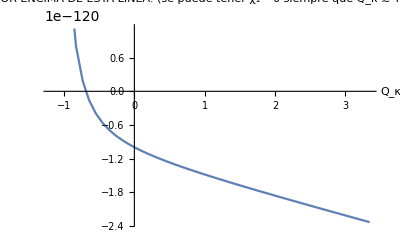

Dicho punto de corte corresponde a [ Q_κ==1/651 (-738+√83085) ≡ Q_c ]

```mathematica
Ho=10^(-42);
mp=2.435*10^(18);

Plot[-η/(6α) ,{Subscript[Q, κ],Qi,Qf},AxesLabel->{"Q_κ"},PlotLabel->StringForm["Q_1 ≡ χ_1/α  DEBE ESTAR POR ENCIMA DE ESTA LÍNEA:
(se puede tener χ_1= 0 siempre que Q_κ ≳ `` ).
",Reduce[-η/(6α)==0&&Qi<Subscript[Q, κ]<Qf][[2]]]]

Print[" Dicho punto de corte corresponde a [ ",Reduce[(536713+1254169 Subscript[Q, κ]+777675 Subscript[Q, κ]^2+125643 Subscript[Q, κ]^3)==0&&Qi<Subscript[Q, κ]<Qf]," ≡ Q_c ]"];
```

```mathematica
Print[]; Print["EN RESUMEN, EXACTAMENTE: [ ",Rangoβ," && Q_4=5/4(Q_κ-1) && Q_1 > -Q_η/6 ] , con Q_η = Ho^2/mp^2."];
Print[]; Print["O bien: [ ",N[Rangoβ,6]," && Q_4=5/4(Q_κ-1) && Q_1 > -Q_η/6 ] , con Q_η = Ho^2/mp^2."]; Print[];

Print["PERO SIEMPRE DEBE SELECCIONAR [ γ_2 si Q_1<0 ][ γ_3 si Q_1>0 ]. Aunque Q_1>0 es poco maniobrable porque exige [ Qi<Q_κ<Q_c ] y note que [ Q_1→∞ ⇔ Q_κ→Qi ][ Q_c-Qi≈0.503 ]"] ; Print[];
```

EN RESUMEN, EXACTAMENTE: [ α>0&&-123/103<Q_κ<97/29 && Q_4=5/4(Q_κ-1) && Q_1 > -Q_η/6 ] , con Q_η = Ho^2/mp^2.

O bien: [ α>0&&-1.19417<Q_κ<3.34483 && Q_4=5/4(Q_κ-1) && Q_1 > -Q_η/6 ] , con Q_η = Ho^2/mp^2.

PERO SIEMPRE DEBE SELECCIONAR [ γ_2 si Q_1<0 ][ γ_3 si Q_1>0 ]. Aunque Q_1>0 es poco maniobrable porque exige [ Qi<Q_κ<Q_c ] y note que [ Q_1→∞ ⇔ Q_κ→Qi ][ Q_c-Qi≈0.503 ]

```mathematica
Subscript[θ, 4]=Subscript[Q, 4] α; λ=Subscript[Q, λ] α; κ=Subscript[Q, κ] α;
RangosGabriel=α>0&&((κ≤0&&Subscript[θ, 4]==1/4 (-5 α+5 κ)&&1/64 (19 α-112 Subscript[θ, 4]+53 κ)-1/64 √(19881 α^2+31584 α Subscript[θ, 4]+12544 Subscript[θ, 4]^2-16290 α κ-6752 Subscript[θ, 4] κ-455 κ^2)≤λ≤1/2 (5 α-κ))||(0<κ<(757 α)/2141-(64 √(699/5) √(α^2))/2141&&Subscript[θ, 4]==1/4 (-5 α+5 κ)&&1/64 (19 α-112 Subscript[θ, 4]+53 κ)-1/64 √(19881 α^2+31584 α Subscript[θ, 4]+12544 Subscript[θ, 4]^2-16290 α κ-6752 Subscript[θ, 4] κ-455 κ^2)≤λ≤1/64 (19 α-112 Subscript[θ, 4]+53 κ)+1/64 √(19881 α^2+31584 α Subscript[θ, 4]+12544 Subscript[θ, 4]^2-16290 α κ-6752 Subscript[θ, 4] κ-455 κ^2))||(κ==(757 α)/2141-(64 √(699/5) √(α^2))/2141&&Subscript[θ, 4]==1/4 (-5 α+5 κ)&&λ==1/64 (19 α-112 Subscript[θ, 4]+53 κ)-1/64 √(19881 α^2+31584 α Subscript[θ, 4]+12544 Subscript[θ, 4]^2-16290 α κ-6752 Subscript[θ, 4] κ-455 κ^2))||(κ==(757 α)/2141+(64 √(699/5) √(α^2))/2141&&Subscript[θ, 4]==1/4 (-5 α+5 κ)&&λ==1/64 (19 α-112 Subscript[θ, 4]+53 κ)-1/64 √(19881 α^2+31584 α Subscript[θ, 4]+12544 Subscript[θ, 4]^2-16290 α κ-6752 Subscript[θ, 4] κ-455 κ^2))||((757 α)/2141+(64 √(699/5) √(α^2))/2141<κ<α&&Subscript[θ, 4]==1/4 (-5 α+5 κ)&&1/64 (19 α-112 Subscript[θ, 4]+53 κ)-1/64 √(19881 α^2+31584 α Subscript[θ, 4]+12544 Subscript[θ, 4]^2-16290 α κ-6752 Subscript[θ, 4] κ-455 κ^2)≤λ≤1/64 (19 α-112 Subscript[θ, 4]+53 κ)+1/64 √(19881 α^2+31584 α Subscript[θ, 4]+12544 Subscript[θ, 4]^2-16290 α κ-6752 Subscript[θ, 4] κ-455 κ^2))||(α≤κ<81 α&&Subscript[θ, 4]==1/4 (-5 α+5 κ)&&1/64 (19 α-112 Subscript[θ, 4]+53 κ)-1/64 √(19881 α^2+31584 α Subscript[θ, 4]+12544 Subscript[θ, 4]^2-16290 α κ-6752 Subscript[θ, 4] κ-455 κ^2)≤λ≤1/2 (5 α-κ)));
```

```mathematica
soluciones=Reduce[α>0&&-123/103<Subscript[Q, κ]<97/29 && Subscript[Q, 4]==5/4(Subscript[Q, κ]-1)&&RangosGabriel];
For[i=1,i≤Length[soluciones],i++,

Clear[Qvalue,Qκi,Qκf];
soli=soluciones[[i]]//Factor;
soliparts=Cases[soli,_];
For[ii=1,ii≤Length[soliparts],ii++,If[Cases[soliparts[[ii]],Subscript[Q, κ]]≠ {},RangoQκ=soliparts[[ii]]];If[Cases[soliparts[[ii]],Subscript[Q, λ]]≠ {},RangoQλ=soliparts[[ii]]]];
SSκequality=StringSplit[ToString[N[RangoQκ]],{"Q⎵Subscript⎵κ"," == "}];
SSλequality=StringSplit[ToString[N[RangoQλ]],{"Q⎵Subscript⎵κ"," == "}];
If[
Length[SSκequality]==1,
Qvalue=RangoQκ[[2]];Print[StringForm[" ``    ",i],soli,StringForm["&& Q_4≃ ``",N[5/4(Qvalue-1),3]]],
Qκi=RangoQκ[[1]];Qκf=RangoQκ[[5]]; Qλi=RangoQλ[[1]];Qλf=RangoQλ[[5]];

(*If[(Qκi==(Qκi/.Subscript[Q, λ]-> 0))&&(Qκf==(Qκf/.Subscript[Q, λ]-> 0)),*)
Print[StringForm[" ``    ",i],soli,StringForm["&& `` ≲ Q_4 ≲ ``",N[5/4(Qκi-1),3],N[5/4(Qκf-1),3]]](*];
If[((Qκi/.Subscript[Q, λ]-> 1)≠(Qκi/.Subscript[Q, λ]-> 0))&&((Qκf/.Subscript[Q, λ]-> 1)≠(Qκf/.Subscript[Q, λ]-> 0)),

Print[((Qκi/.Subscript[Q, λ]-> 1)==(Qκi/.Subscript[Q, λ]-> 0))&&((Qκf/.Subscript[Q, λ]-> 1)==(Qκf/.Subscript[Q, λ]-> 0))];
Print[Qλi,"  ",Qλf]; Plot3D[5/4(Subscript[Q, κ]-1),{Subscript[Q, κ],MinValue[Subscript[Q, κ],Qλi<Subscript[Q, λ]<Qλf],MaxValue[Subscript[Q, κ],Qλi<Subscript[Q, λ]<Qλf]},{Subscript[Q, λ],Qλi,Qλf}]]*)
]]; Print[];
```

α>0&&Q_κ==(3785-64 √3495)/10705&&Q_λ==(3 (7150+29 √3495))/10705&& Q_4≃ -1.25

α>0&&Q_κ==(3785+64 √3495)/10705&&Q_λ==-(3 (-7150+29 √3495))/10705&& Q_4≃ -0.366

(13539-√64467721)/3296<Q_λ≤79/32&&-123/103<Q_κ≤1/49 (-157+87 Q_λ-√(44004-42900 Q_λ+10705 Q_λ^2))&&α>0&& -2.74 ≲ Q_4 ≲ 1.25\ (-1. + 0.0204\ (-157. + 87.\ Q_λ - 1.\ √44000. - 42900.\ Q_λ + 10700.\ Q_λ 2))

79/32<Q_λ≤5/2&&-123/103<Q_κ≤0&&α>0&& -2.74 ≲ Q_4 ≲ -1.25

5/2<Q_λ<319/103&&-123/103<Q_κ≤5-2 Q_λ&&α>0&& -2.74 ≲ Q_4 ≲ 1.25\ (4. - 2.\ Q_λ)

1/464 (-957-√4964361)<Q_λ≤1/4&&1/49 (-157+87 Q_λ+√(44004-42900 Q_λ+10705 Q_λ^2))≤Q_κ<97/29&&α>0&& 1.25\ (-1. + 0.0204\ (-157. + 87.\ Q_λ + √44000. - 42900.\ Q_λ + 10700.\ Q_λ 2)) ≲ Q_4 ≲ 2.93

1/4<Q_λ≤24/29&&1≤Q_κ<97/29&&α>0&& 0 ≲ Q_4 ≲ 2.93

24/29<Q_λ<2&&1≤Q_κ≤5-2 Q_λ&&α>0&& 0 ≲ Q_4 ≲ 1.25\ (4. - 2.\ Q_λ)

Q_λ==2&&Q_κ==1&&α>0&& Q_4≃ 0

0<Q_κ<(3785-64 √3495)/10705&&1/64 (159-87 Q_κ-√(1-7570 Q_κ+10705 Q_κ^2))≤Q_λ≤1/64 (159-87 Q_κ+√(1-7570 Q_κ+10705 Q_κ^2))&&α>0&& -1.25 ≲ Q_4 ≲ -1.25

(3785+64 √3495)/10705<Q_κ<1&&1/64 (159-87 Q_κ-√(1-7570 Q_κ+10705 Q_κ^2))≤Q_λ≤1/64 (159-87 Q_κ+√(1-7570 Q_κ+10705 Q_κ^2))&&α>0&& -0.366 ≲ Q_4 ≲ 0

## 3. Solución numérica - N.ba I ( programado para ejecutarse después de 1 y 2 )

```mathematica
Clear@@DeleteCases[Names@"`*","fried"|"Qi"|"Qf"|"asintotas"];

soln[t0_,Ωr0_,Ωm0_,x0_,y0_,z0_,ξ_,g_,α_,κ_,θ4_,χ1_,χ2_,χ3_,χ4_,χ5_,θ1_]:=NDSolve[
{
 x'[t]==(-304128 Subscript[χ, 5]^2 y[t]^10 (x[t]+y[t])^7-48 Subscript[χ, 5] y[t]^5 (x[t]+y[t])^2 z[t]^4 (ξ (x[t]+y[t]) (x[t]^2 (11+12 y[t])+2 x[t] y[t] (11+12 y[t])+y[t] (11 y[t]+12 y[t]^2+24 g^2 z[t]^4))+2 y[t] (x[t]^3 (-48 Subscript[θ, 1]+y[t] (11 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4]))+12 (307 α+96 Subscript[θ, 4]+35 κ+2 Subscript[χ, 3]+2 Subscript[χ, 4]) y[t]))+x[t]^2 (Subscript[θ, 1] (22-112 y[t])+y[t]^2 (-11 (37 α+16 Subscript[θ, 4]+3 (κ+4 (Subscript[χ, 3]+Subscript[χ, 4])))+4 (875 α+512 Subscript[θ, 4]+9 (23 κ+2 Subscript[χ, 3]+2 Subscript[χ, 4])) y[t]))+x[t] (-2+44 Subscript[θ, 1] y[t]-108 Subscript[θ, 1] y[t]^2-11 (89 α+32 Subscript[θ, 4]+9 κ+12 Subscript[χ, 3]+12 Subscript[χ, 4]) y[t]^3+8 (33 α+184 Subscript[θ, 4]+82 κ+9 Subscript[χ, 3]+9 Subscript[χ, 4]) y[t]^4-72 (Subscript[χ, 1]+Subscript[χ, 2]) z[t]^4+6 Ωr[t])-y[t] (-22 Subscript[θ, 1] y[t]+20 Subscript[θ, 1] y[t]^2+11 (47 α+16 Subscript[θ, 4]+5 κ+4 Subscript[χ, 3]+4 Subscript[χ, 4]) y[t]^3+8 (193 α-24 Subscript[θ, 4]-16 κ-3 Subscript[χ, 3]-3 Subscript[χ, 4]) y[t]^4+72 (Subscript[χ, 1]+Subscript[χ, 2]) z[t]^4-2 (5+3 Ωr[t]))))+z[t]^8 (-ξ^2 y[t] (x[t]+y[t]) (x[t]^2+2 x[t] y[t]+y[t]^2+2 g^2 z[t]^4)+ξ (2 (93 α-3 κ+2 (Subscript[χ, 3]+Subscript[χ, 4])) y[t]^6+4 x[t]^2 y[t]^2 (Subscript[θ, 1]+(-58 α-56 Subscript[θ, 4]-25 κ+3 Subscript[χ, 3]+3 Subscript[χ, 4]) y[t]^2)+4 x[t]^3 (2 Subscript[θ, 1] y[t]+(-156 α-48 Subscript[θ, 4]-18 κ+Subscript[χ, 3]+Subscript[χ, 4]) y[t]^3)+8 g^2 z[t]^4+y[t]^4 (-6 Subscript[θ, 1]+4 g^2 (-77 α+16 Subscript[θ, 4]+9 κ+4 Subscript[χ, 3]+4 Subscript[χ, 4]) z[t]^4)+y[t]^2 (1+12 (-2 g^2 Subscript[θ, 1]+Subscript[χ, 1]+Subscript[χ, 2]) z[t]^4-Ωr[t])+x[t] y[t] (3+6 (41 α-16 Subscript[θ, 4]-9 κ+2 Subscript[χ, 3]+2 Subscript[χ, 4]) y[t]^4-4 (8 g^2 Subscript[θ, 1]-3 (Subscript[χ, 1]+Subscript[χ, 2])) z[t]^4+2 y[t]^2 (-3 Subscript[θ, 1]+2 g^2 (203 α+64 Subscript[θ, 4]+23 κ+4 Subscript[χ, 3]+4 Subscript[χ, 4]) z[t]^4)-Ωr[t]))-2 (2 Subscript[θ, 1] (-231 α+48 Subscript[θ, 4]+27 κ+4 Subscript[χ, 3]+4 Subscript[χ, 4]) y[t]^6+4 (616 α^2-128 Subscript[θ, 4]^2-27 κ^2-23 κ Subscript[χ, 3]-4 Subscript[χ, 3]^2-23 κ Subscript[χ, 4]-8 Subscript[χ, 3] Subscript[χ, 4]-4 Subscript[χ, 4]^2-24 Subscript[θ, 4] (5 κ+2 (Subscript[χ, 3]+Subscript[χ, 4]))+α (488 Subscript[θ, 4]+159 κ+107 (Subscript[χ, 3]+Subscript[χ, 4]))) y[t]^8-2 x[t]^3 y[t]^3 (8 Subscript[θ, 1] (Subscript[χ, 3]+Subscript[χ, 4])+(-1015 α^2-23 κ^2+66 κ Subscript[χ, 3]+8 Subscript[χ, 3]^2+66 κ Subscript[χ, 4]+16 Subscript[χ, 3] Subscript[χ, 4]+8 Subscript[χ, 4]^2-64 Subscript[θ, 4] (κ-3 (Subscript[χ, 3]+Subscript[χ, 4]))+α (-320 Subscript[θ, 4]+6 (-53 κ+99 (Subscript[χ, 3]+Subscript[χ, 4])))) y[t]^2)-2 x[t]^2 y[t]^2 (5 α+8 Subscript[θ, 1]^2+κ-6 Subscript[χ, 3]-6 Subscript[χ, 4]-4 Subscript[θ, 1] (203 α+64 Subscript[θ, 4]+23 κ-2 Subscript[χ, 3]-2 Subscript[χ, 4]) y[t]^2+(14889 α^2+1536 Subscript[θ, 4]^2+159 κ^2+158 κ Subscript[χ, 3]+24 Subscript[χ, 3]^2+158 κ Subscript[χ, 4]+48 Subscript[χ, 3] Subscript[χ, 4]+24 Subscript[χ, 4]^2+16 Subscript[θ, 4] (63 κ+26 (Subscript[χ, 3]+Subscript[χ, 4]))+6 α (1544 Subscript[θ, 4]+532 κ+107 (Subscript[χ, 3]+Subscript[χ, 4]))) y[t]^4)+8 (3 Subscript[χ, 1]+Subscript[χ, 2]) z[t]^4+2 Subscript[θ, 1] y[t]^2 (-4 (9 Subscript[χ, 1]+5 Subscript[χ, 2]) z[t]^4+Ωr[t])+y[t]^4 (77 α-16 Subscript[θ, 4]-9 κ+4 (27 κ Subscript[χ, 1]+19 κ Subscript[χ, 2]+48 Subscript[θ, 4] (Subscript[χ, 1]+Subscript[χ, 2])+α (-231 Subscript[χ, 1]+17 Subscript[χ, 2])+12 Subscript[χ, 1] Subscript[χ, 3]+12 Subscript[χ, 2] Subscript[χ, 3]+12 Subscript[χ, 1] Subscript[χ, 4]+12 Subscript[χ, 2] Subscript[χ, 4]) z[t]^4-(47 α+16 Subscript[θ, 4]+5 κ+4 Subscript[χ, 3]+4 Subscript[χ, 4]) Ωr[t])+x[t] y[t] (6 Subscript[θ, 1] (49 α+96 Subscript[θ, 4]+41 κ+4 Subscript[χ, 3]+4 Subscript[χ, 4]) y[t]^4+4 (1995 α^2-768 Subscript[θ, 4]^2-114 κ^2-89 κ Subscript[χ, 3]-12 Subscript[χ, 3]^2-89 κ Subscript[χ, 4]-24 Subscript[χ, 3] Subscript[χ, 4]-12 Subscript[χ, 4]^2-8 Subscript[θ, 4] (75 κ+28 (Subscript[χ, 3]+Subscript[χ, 4]))-3 α (552 Subscript[θ, 4]+277 κ+83 (Subscript[χ, 3]+Subscript[χ, 4]))) y[t]^6-32 Subscript[θ, 1] (3 Subscript[χ, 1]+Subscript[χ, 2]) z[t]^4+y[t]^2 (-15 α-24 Subscript[θ, 1]^2-3 κ+20 Subscript[χ, 3]+20 Subscript[χ, 4]+4 (64 Subscript[θ, 4] (3 Subscript[χ, 1]+Subscript[χ, 2])+α (609 Subscript[χ, 1]+193 Subscript[χ, 2])+3 (κ (23 Subscript[χ, 1]+7 Subscript[χ, 2])+4 (Subscript[χ, 1]+Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4]))) z[t]^4+5 α Ωr[t]+κ Ωr[t]-4 Subscript[χ, 3] Ωr[t]-4 Subscript[χ, 4] Ωr[t])))))/(2 y[t] z[t]^4 (576 Subscript[χ, 5] y[t]^5 (x[t]+y[t])^2 (-1-2 Subscript[θ, 1] y[t]^2+2 (83 α+16 Subscript[θ, 4]+5 κ) y[t]^4)+(ξ (-1-2 Subscript[θ, 1] y[t]^2+2 (83 α+16 Subscript[θ, 4]+5 κ) y[t]^4)-2 y[t]^2 (5 α+8 Subscript[θ, 1]^2+κ-4 Subscript[χ, 3]-4 Subscript[χ, 4]-2 Subscript[θ, 1] (203 α+64 Subscript[θ, 4]+23 κ+4 Subscript[χ, 3]+4 Subscript[χ, 4]) y[t]^2+2 (2289 α^2+256 Subscript[θ, 4]^2+16 Subscript[θ, 4] (11 κ+4 (Subscript[χ, 3]+Subscript[χ, 4]))+κ (31 κ+20 (Subscript[χ, 3]+Subscript[χ, 4]))+4 α (396 Subscript[θ, 4]+129 κ+83 (Subscript[χ, 3]+Subscript[χ, 4]))) y[t]^4)) z[t]^4)),

y'[t]==x[t], 

z'[t]==-((-304128 Subscript[χ, 5]^2 x[t]^6 y[t]^10-1824768 Subscript[χ, 5]^2 x[t]^5 y[t]^11-48 Subscript[χ, 5] x[t]^4 y[t]^5 (95040 Subscript[χ, 5] y[t]^7+11 ξ z[t]^4+12 (-8 Subscript[θ, 1]+ξ) y[t] z[t]^4+22 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) y[t]^2 z[t]^4+24 (307 α+96 Subscript[θ, 4]+35 κ+2 Subscript[χ, 3]+2 Subscript[χ, 4]) y[t]^3 z[t]^4)-192 Subscript[χ, 5] x[t]^3 y[t]^5 (31680 Subscript[χ, 5] y[t]^8+(12+11 ξ y[t]+4 (-14 Subscript[θ, 1]+3 ξ) y[t]^2+22 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) y[t]^3+8 (200 α+152 Subscript[θ, 4]+63 κ+6 Subscript[χ, 3]+6 Subscript[χ, 4]) y[t]^4) z[t]^4)-2 x[t] (912384 Subscript[χ, 5]^2 y[t]^15+1056 ξ Subscript[χ, 5] y[t]^8 z[t]^4+1152 (-Subscript[θ, 1]+ξ) Subscript[χ, 5] y[t]^9 z[t]^4+2112 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) Subscript[χ, 5] y[t]^10 z[t]^4-1152 (413 α-11 κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) Subscript[χ, 5] y[t]^11 z[t]^4+2 ξ z[t]^8+(20 α+32 Subscript[θ, 1]^2+4 κ+4 Subscript[θ, 1] ξ+ξ^2-16 Subscript[χ, 3]-16 Subscript[χ, 4]) y[t]^2 z[t]^8-4 (7 α (58 Subscript[θ, 1]+17 ξ)+ξ (8 Subscript[θ, 4]+Subscript[χ, 3]+Subscript[χ, 4])+2 Subscript[θ, 1] (64 Subscript[θ, 4]+23 κ+8 (Subscript[χ, 3]+Subscript[χ, 4]))) y[t]^4 z[t]^8+4 (4193 α^2+512 Subscript[θ, 4]^2+71 κ^2+30 κ Subscript[χ, 3]-8 Subscript[χ, 3]^2+30 κ Subscript[χ, 4]-16 Subscript[χ, 3] Subscript[χ, 4]-8 Subscript[χ, 4]^2+16 Subscript[θ, 4] (23 κ+8 (Subscript[χ, 3]+Subscript[χ, 4]))+2 α (1624 Subscript[θ, 4]+500 κ+595 (Subscript[χ, 3]+Subscript[χ, 4]))) y[t]^6 z[t]^8+576 Subscript[χ, 5] y[t]^7 z[t]^4 (5+2 (g^2 ξ-6 (Subscript[χ, 1]+Subscript[χ, 2])) z[t]^4+Ωr[t]))-x[t]^2 y[t] (4561920 Subscript[χ, 5]^2 y[t]^13+3168 ξ Subscript[χ, 5] y[t]^6 z[t]^4+1152 (-7 Subscript[θ, 1]+3 ξ) Subscript[χ, 5] y[t]^7 z[t]^4+6336 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) Subscript[χ, 5] y[t]^8 z[t]^4-1152 (627 α-112 Subscript[θ, 4]-67 κ-12 Subscript[χ, 3]-12 Subscript[χ, 4]) Subscript[χ, 5] y[t]^9 z[t]^4+ξ (-8 Subscript[θ, 1]+ξ) z[t]^8+4 (156 α ξ+48 Subscript[θ, 4] ξ+18 κ ξ-(8 Subscript[θ, 1]+ξ) Subscript[χ, 3]-8 Subscript[θ, 1] Subscript[χ, 4]-ξ Subscript[χ, 4]) y[t]^2 z[t]^8+4 (1015 α^2+23 κ^2-66 κ Subscript[χ, 3]-8 Subscript[χ, 3]^2-66 κ Subscript[χ, 4]-16 Subscript[χ, 3] Subscript[χ, 4]-8 Subscript[χ, 4]^2+64 Subscript[θ, 4] (κ-3 (Subscript[χ, 3]+Subscript[χ, 4]))+α (320 Subscript[θ, 4]+6 (53 κ-99 (Subscript[χ, 3]+Subscript[χ, 4])))) y[t]^4 z[t]^8+576 Subscript[χ, 5] y[t]^5 z[t]^4 (11+2 (g^2 ξ-6 (Subscript[χ, 1]+Subscript[χ, 2])) z[t]^4+Ωr[t]))-y[t] (304128 Subscript[χ, 5]^2 y[t]^15+528 ξ Subscript[χ, 5] y[t]^8 z[t]^4+192 (-2 Subscript[θ, 1]+3 ξ) Subscript[χ, 5] y[t]^9 z[t]^4+1056 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) Subscript[χ, 5] y[t]^10 z[t]^4-768 (359 α+8 Subscript[θ, 4]-3 (2 κ+Subscript[χ, 3]+Subscript[χ, 4])) Subscript[χ, 5] y[t]^11 z[t]^4-2 (α (1526 Subscript[θ, 1]+373 ξ)+ξ (48 Subscript[θ, 4]+11 κ+2 (Subscript[χ, 3]+Subscript[χ, 4]))+2 Subscript[θ, 1] (160 Subscript[θ, 4]+3 (17 κ+4 (Subscript[χ, 3]+Subscript[χ, 4])))) y[t]^4 z[t]^8+8 (5243 α^2+256 Subscript[θ, 4]^2+24 κ^2+13 κ Subscript[χ, 3]-4 Subscript[χ, 3]^2+13 κ Subscript[χ, 4]-8 Subscript[χ, 3] Subscript[χ, 4]-4 Subscript[χ, 4]^2+8 Subscript[θ, 4] (19 κ+8 (Subscript[χ, 3]+Subscript[χ, 4]))+α (2616 Subscript[θ, 4]+755 κ+657 (Subscript[χ, 3]+Subscript[χ, 4]))) y[t]^6 z[t]^8+576 Subscript[χ, 5] y[t]^7 z[t]^4 (3+2 (g^2 ξ-6 (Subscript[χ, 1]+Subscript[χ, 2])) z[t]^4+Ωr[t])+y[t]^2 z[t]^8 (30 α+48 Subscript[θ, 1]^2+6 κ+10 Subscript[θ, 1] ξ+ξ^2-24 Subscript[χ, 3]-24 Subscript[χ, 4]+4 (-g^2 ξ (203 α+64 Subscript[θ, 4]+23 κ+4 Subscript[χ, 3]+4 Subscript[χ, 4])+2 (64 Subscript[θ, 4] (3 Subscript[χ, 1]+Subscript[χ, 2])+α (609 Subscript[χ, 1]+193 Subscript[χ, 2])+3 (κ (23 Subscript[χ, 1]+7 Subscript[χ, 2])+4 (Subscript[χ, 1]+Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4])))) z[t]^4+2 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) Ωr[t])+z[t]^8 (2 (g^2 ξ (16 Subscript[θ, 1]+ξ)-2 (3 ξ (Subscript[χ, 1]+Subscript[χ, 2])+16 Subscript[θ, 1] (3 Subscript[χ, 1]+Subscript[χ, 2]))) z[t]^4+ξ (3+Ωr[t]))))/(4 y[t] z[t]^3 (-576 Subscript[χ, 5] y[t]^5 (x[t]+y[t])^2 (-1-2 Subscript[θ, 1] y[t]^2+2 (83 α+16 Subscript[θ, 4]+5 κ) y[t]^4)+(ξ+2 (5 α+8 Subscript[θ, 1]^2+κ+Subscript[θ, 1] ξ-4 Subscript[χ, 3]-4 Subscript[χ, 4]) y[t]^2-2 (406 α Subscript[θ, 1]+128 Subscript[θ, 1] Subscript[θ, 4]+46 Subscript[θ, 1] κ+83 α ξ+16 Subscript[θ, 4] ξ+5 κ ξ+8 Subscript[θ, 1] Subscript[χ, 3]+8 Subscript[θ, 1] Subscript[χ, 4]) y[t]^4+4 (2289 α^2+256 Subscript[θ, 4]^2+16 Subscript[θ, 4] (11 κ+4 (Subscript[χ, 3]+Subscript[χ, 4]))+κ (31 κ+20 (Subscript[χ, 3]+Subscript[χ, 4]))+4 α (396 Subscript[θ, 4]+129 κ+83 (Subscript[χ, 3]+Subscript[χ, 4]))) y[t]^6) z[t]^4))),

(*   Subscript[Ω, i]'= Subscript[Ω, i](2ϵ-3(ω+1))    *)

Ωr'[t]==Ωr[t](-3((1/3)+1)+2((304128 Subscript[χ, 5]^2 x[t]^6 y[t]^9+1824768 Subscript[χ, 5]^2 x[t]^5 y[t]^10+304128 Subscript[χ, 5]^2 y[t]^15+528 ξ Subscript[χ, 5] y[t]^8 z[t]^4-192 (2 Subscript[θ, 1]-3 ξ) Subscript[χ, 5] y[t]^9 z[t]^4+1056 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) Subscript[χ, 5] y[t]^10 z[t]^4-768 (359 α+8 Subscript[θ, 4]-3 (2 κ+Subscript[χ, 3]+Subscript[χ, 4])) Subscript[χ, 5] y[t]^11 z[t]^4-2 (α (1526 Subscript[θ, 1]+373 ξ)+ξ (48 Subscript[θ, 4]+11 κ+2 (Subscript[χ, 3]+Subscript[χ, 4]))+2 Subscript[θ, 1] (160 Subscript[θ, 4]+3 (17 κ+4 (Subscript[χ, 3]+Subscript[χ, 4])))) y[t]^4 z[t]^8+8 (5243 α^2+256 Subscript[θ, 4]^2+24 κ^2+13 κ Subscript[χ, 3]-4 Subscript[χ, 3]^2+13 κ Subscript[χ, 4]-8 Subscript[χ, 3] Subscript[χ, 4]-4 Subscript[χ, 4]^2+8 Subscript[θ, 4] (19 κ+8 (Subscript[χ, 3]+Subscript[χ, 4]))+α (2616 Subscript[θ, 4]+755 κ+657 (Subscript[χ, 3]+Subscript[χ, 4]))) y[t]^6 z[t]^8+48 Subscript[χ, 5] x[t]^4 y[t]^4 (95040 Subscript[χ, 5] y[t]^7+11 ξ z[t]^4+12 (-8 Subscript[θ, 1]+ξ) y[t] z[t]^4+22 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) y[t]^2 z[t]^4+24 (307 α+96 Subscript[θ, 4]+35 κ+2 Subscript[χ, 3]+2 Subscript[χ, 4]) y[t]^3 z[t]^4)+192 Subscript[χ, 5] x[t]^3 y[t]^5 (31680 Subscript[χ, 5] y[t]^7+11 ξ z[t]^4+4 (-20 Subscript[θ, 1]+3 ξ) y[t] z[t]^4+22 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) y[t]^2 z[t]^4+8 (449 α+200 Subscript[θ, 4]+6 (13 κ+Subscript[χ, 3]+Subscript[χ, 4])) y[t]^3 z[t]^4)+576 Subscript[χ, 5] y[t]^7 z[t]^4 (3+2 (g^2 ξ-6 (Subscript[χ, 1]+Subscript[χ, 2])) z[t]^4+Ωr[t])+y[t]^2 z[t]^8 (30 α+48 Subscript[θ, 1]^2+6 κ+10 Subscript[θ, 1] ξ+ξ^2-24 Subscript[χ, 3]-24 Subscript[χ, 4]+4 (-g^2 ξ (203 α+64 Subscript[θ, 4]+23 κ+4 Subscript[χ, 3]+4 Subscript[χ, 4])+2 (64 Subscript[θ, 4] (3 Subscript[χ, 1]+Subscript[χ, 2])+α (609 Subscript[χ, 1]+193 Subscript[χ, 2])+3 (κ (23 Subscript[χ, 1]+7 Subscript[χ, 2])+4 (Subscript[χ, 1]+Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4])))) z[t]^4+10 α Ωr[t]+2 κ Ωr[t]-8 Subscript[χ, 3] Ωr[t]-8 Subscript[χ, 4] Ωr[t])+z[t]^8 (2 (g^2 ξ (16 Subscript[θ, 1]+ξ)-2 (3 ξ (Subscript[χ, 1]+Subscript[χ, 2])+16 Subscript[θ, 1] (3 Subscript[χ, 1]+Subscript[χ, 2]))) z[t]^4+ξ (3+Ωr[t]))+2 x[t] y[t] (912384 Subscript[χ, 5]^2 y[t]^13+1056 ξ Subscript[χ, 5] y[t]^6 z[t]^4-1152 (3 Subscript[θ, 1]-ξ) Subscript[χ, 5] y[t]^7 z[t]^4+2112 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) Subscript[χ, 5] y[t]^8 z[t]^4-1152 (247 α-32 Subscript[θ, 4]-21 κ-4 Subscript[χ, 3]-4 Subscript[χ, 4]) Subscript[χ, 5] y[t]^9 z[t]^4+ξ^2 z[t]^8-4 (36 α ξ-8 Subscript[θ, 4] ξ-5 κ ξ+8 Subscript[θ, 1] Subscript[χ, 3]+ξ Subscript[χ, 3]+8 Subscript[θ, 1] Subscript[χ, 4]+ξ Subscript[χ, 4]) y[t]^2 z[t]^8-4 (385 α^2-16 Subscript[θ, 4] κ-9 κ^2+10 κ Subscript[χ, 3]+8 Subscript[χ, 3]^2+10 κ Subscript[χ, 4]+16 Subscript[χ, 3] Subscript[χ, 4]+8 Subscript[χ, 4]^2-2 α (40 Subscript[θ, 4]-16 κ+263 (Subscript[χ, 3]+Subscript[χ, 4]))) y[t]^4 z[t]^8+576 Subscript[χ, 5] y[t]^5 z[t]^4 (3+2 (g^2 ξ-6 (Subscript[χ, 1]+Subscript[χ, 2])) z[t]^4+Ωr[t]))+x[t]^2 (4561920 Subscript[χ, 5]^2 y[t]^13+3168 ξ Subscript[χ, 5] y[t]^6 z[t]^4-3456 (5 Subscript[θ, 1]-ξ) Subscript[χ, 5] y[t]^7 z[t]^4+6336 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) Subscript[χ, 5] y[t]^8 z[t]^4+1152 (37 α+240 Subscript[θ, 4]+107 κ+12 Subscript[χ, 3]+12 Subscript[χ, 4]) Subscript[χ, 5] y[t]^9 z[t]^4+ξ (-8 Subscript[θ, 1]+ξ) z[t]^8+4 (156 α ξ+48 Subscript[θ, 4] ξ+18 κ ξ-8 Subscript[θ, 1] Subscript[χ, 3]-ξ Subscript[χ, 3]-8 Subscript[θ, 1] Subscript[χ, 4]-ξ Subscript[χ, 4]) y[t]^2 z[t]^8+4 (1015 α^2+23 κ^2-66 κ Subscript[χ, 3]-8 Subscript[χ, 3]^2-66 κ Subscript[χ, 4]-16 Subscript[χ, 3] Subscript[χ, 4]-8 Subscript[χ, 4]^2+64 Subscript[θ, 4] (κ-3 (Subscript[χ, 3]+Subscript[χ, 4]))+α (320 Subscript[θ, 4]+6 (53 κ-99 (Subscript[χ, 3]+Subscript[χ, 4])))) y[t]^4 z[t]^8+576 Subscript[χ, 5] y[t]^5 z[t]^4 (3+2 (g^2 ξ-6 (Subscript[χ, 1]+Subscript[χ, 2])) z[t]^4+Ωr[t])))/(2 z[t]^4 (576 Subscript[χ, 5] y[t]^7+1152 Subscript[θ, 1] Subscript[χ, 5] y[t]^9-1152 (83 α+16 Subscript[θ, 4]+5 κ) Subscript[χ, 5] y[t]^11-576 Subscript[χ, 5] x[t]^2 y[t]^5 (-1-2 Subscript[θ, 1] y[t]^2+2 (83 α+16 Subscript[θ, 4]+5 κ) y[t]^4)-1152 Subscript[χ, 5] x[t] y[t]^6 (-1-2 Subscript[θ, 1] y[t]^2+2 (83 α+16 Subscript[θ, 4]+5 κ) y[t]^4)+ξ z[t]^4+2 (5 α+8 Subscript[θ, 1]^2+κ+Subscript[θ, 1] ξ-4 Subscript[χ, 3]-4 Subscript[χ, 4]) y[t]^2 z[t]^4-2 (406 α Subscript[θ, 1]+128 Subscript[θ, 1] Subscript[θ, 4]+46 Subscript[θ, 1] κ+83 α ξ+16 Subscript[θ, 4] ξ+5 κ ξ+8 Subscript[θ, 1] Subscript[χ, 3]+8 Subscript[θ, 1] Subscript[χ, 4]) y[t]^4 z[t]^4+4 (2289 α^2+256 Subscript[θ, 4]^2+16 Subscript[θ, 4] (11 κ+4 (Subscript[χ, 3]+Subscript[χ, 4]))+κ (31 κ+20 (Subscript[χ, 3]+Subscript[χ, 4]))+4 α (396 Subscript[θ, 4]+129 κ+83 (Subscript[χ, 3]+Subscript[χ, 4]))) y[t]^6 z[t]^4)))),

(*   Subscript[Ω, i]'= Subscript[Ω, i](2ϵ-3(ω+1))    *)

Ωm'[t]==Ωm[t](-3(0+1)+2((304128 Subscript[χ, 5]^2 x[t]^6 y[t]^9+1824768 Subscript[χ, 5]^2 x[t]^5 y[t]^10+304128 Subscript[χ, 5]^2 y[t]^15+528 ξ Subscript[χ, 5] y[t]^8 z[t]^4-192 (2 Subscript[θ, 1]-3 ξ) Subscript[χ, 5] y[t]^9 z[t]^4+1056 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) Subscript[χ, 5] y[t]^10 z[t]^4-768 (359 α+8 Subscript[θ, 4]-3 (2 κ+Subscript[χ, 3]+Subscript[χ, 4])) Subscript[χ, 5] y[t]^11 z[t]^4-2 (α (1526 Subscript[θ, 1]+373 ξ)+ξ (48 Subscript[θ, 4]+11 κ+2 (Subscript[χ, 3]+Subscript[χ, 4]))+2 Subscript[θ, 1] (160 Subscript[θ, 4]+3 (17 κ+4 (Subscript[χ, 3]+Subscript[χ, 4])))) y[t]^4 z[t]^8+8 (5243 α^2+256 Subscript[θ, 4]^2+24 κ^2+13 κ Subscript[χ, 3]-4 Subscript[χ, 3]^2+13 κ Subscript[χ, 4]-8 Subscript[χ, 3] Subscript[χ, 4]-4 Subscript[χ, 4]^2+8 Subscript[θ, 4] (19 κ+8 (Subscript[χ, 3]+Subscript[χ, 4]))+α (2616 Subscript[θ, 4]+755 κ+657 (Subscript[χ, 3]+Subscript[χ, 4]))) y[t]^6 z[t]^8+48 Subscript[χ, 5] x[t]^4 y[t]^4 (95040 Subscript[χ, 5] y[t]^7+11 ξ z[t]^4+12 (-8 Subscript[θ, 1]+ξ) y[t] z[t]^4+22 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) y[t]^2 z[t]^4+24 (307 α+96 Subscript[θ, 4]+35 κ+2 Subscript[χ, 3]+2 Subscript[χ, 4]) y[t]^3 z[t]^4)+192 Subscript[χ, 5] x[t]^3 y[t]^5 (31680 Subscript[χ, 5] y[t]^7+11 ξ z[t]^4+4 (-20 Subscript[θ, 1]+3 ξ) y[t] z[t]^4+22 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) y[t]^2 z[t]^4+8 (449 α+200 Subscript[θ, 4]+6 (13 κ+Subscript[χ, 3]+Subscript[χ, 4])) y[t]^3 z[t]^4)+576 Subscript[χ, 5] y[t]^7 z[t]^4 (3+2 (g^2 ξ-6 (Subscript[χ, 1]+Subscript[χ, 2])) z[t]^4+Ωr[t])+y[t]^2 z[t]^8 (30 α+48 Subscript[θ, 1]^2+6 κ+10 Subscript[θ, 1] ξ+ξ^2-24 Subscript[χ, 3]-24 Subscript[χ, 4]+4 (-g^2 ξ (203 α+64 Subscript[θ, 4]+23 κ+4 Subscript[χ, 3]+4 Subscript[χ, 4])+2 (64 Subscript[θ, 4] (3 Subscript[χ, 1]+Subscript[χ, 2])+α (609 Subscript[χ, 1]+193 Subscript[χ, 2])+3 (κ (23 Subscript[χ, 1]+7 Subscript[χ, 2])+4 (Subscript[χ, 1]+Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4])))) z[t]^4+10 α Ωr[t]+2 κ Ωr[t]-8 Subscript[χ, 3] Ωr[t]-8 Subscript[χ, 4] Ωr[t])+z[t]^8 (2 (g^2 ξ (16 Subscript[θ, 1]+ξ)-2 (3 ξ (Subscript[χ, 1]+Subscript[χ, 2])+16 Subscript[θ, 1] (3 Subscript[χ, 1]+Subscript[χ, 2]))) z[t]^4+ξ (3+Ωr[t]))+2 x[t] y[t] (912384 Subscript[χ, 5]^2 y[t]^13+1056 ξ Subscript[χ, 5] y[t]^6 z[t]^4-1152 (3 Subscript[θ, 1]-ξ) Subscript[χ, 5] y[t]^7 z[t]^4+2112 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) Subscript[χ, 5] y[t]^8 z[t]^4-1152 (247 α-32 Subscript[θ, 4]-21 κ-4 Subscript[χ, 3]-4 Subscript[χ, 4]) Subscript[χ, 5] y[t]^9 z[t]^4+ξ^2 z[t]^8-4 (36 α ξ-8 Subscript[θ, 4] ξ-5 κ ξ+8 Subscript[θ, 1] Subscript[χ, 3]+ξ Subscript[χ, 3]+8 Subscript[θ, 1] Subscript[χ, 4]+ξ Subscript[χ, 4]) y[t]^2 z[t]^8-4 (385 α^2-16 Subscript[θ, 4] κ-9 κ^2+10 κ Subscript[χ, 3]+8 Subscript[χ, 3]^2+10 κ Subscript[χ, 4]+16 Subscript[χ, 3] Subscript[χ, 4]+8 Subscript[χ, 4]^2-2 α (40 Subscript[θ, 4]-16 κ+263 (Subscript[χ, 3]+Subscript[χ, 4]))) y[t]^4 z[t]^8+576 Subscript[χ, 5] y[t]^5 z[t]^4 (3+2 (g^2 ξ-6 (Subscript[χ, 1]+Subscript[χ, 2])) z[t]^4+Ωr[t]))+x[t]^2 (4561920 Subscript[χ, 5]^2 y[t]^13+3168 ξ Subscript[χ, 5] y[t]^6 z[t]^4-3456 (5 Subscript[θ, 1]-ξ) Subscript[χ, 5] y[t]^7 z[t]^4+6336 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) Subscript[χ, 5] y[t]^8 z[t]^4+1152 (37 α+240 Subscript[θ, 4]+107 κ+12 Subscript[χ, 3]+12 Subscript[χ, 4]) Subscript[χ, 5] y[t]^9 z[t]^4+ξ (-8 Subscript[θ, 1]+ξ) z[t]^8+4 (156 α ξ+48 Subscript[θ, 4] ξ+18 κ ξ-8 Subscript[θ, 1] Subscript[χ, 3]-ξ Subscript[χ, 3]-8 Subscript[θ, 1] Subscript[χ, 4]-ξ Subscript[χ, 4]) y[t]^2 z[t]^8+4 (1015 α^2+23 κ^2-66 κ Subscript[χ, 3]-8 Subscript[χ, 3]^2-66 κ Subscript[χ, 4]-16 Subscript[χ, 3] Subscript[χ, 4]-8 Subscript[χ, 4]^2+64 Subscript[θ, 4] (κ-3 (Subscript[χ, 3]+Subscript[χ, 4]))+α (320 Subscript[θ, 4]+6 (53 κ-99 (Subscript[χ, 3]+Subscript[χ, 4])))) y[t]^4 z[t]^8+576 Subscript[χ, 5] y[t]^5 z[t]^4 (3+2 (g^2 ξ-6 (Subscript[χ, 1]+Subscript[χ, 2])) z[t]^4+Ωr[t])))/(2 z[t]^4 (576 Subscript[χ, 5] y[t]^7+1152 Subscript[θ, 1] Subscript[χ, 5] y[t]^9-1152 (83 α+16 Subscript[θ, 4]+5 κ) Subscript[χ, 5] y[t]^11-576 Subscript[χ, 5] x[t]^2 y[t]^5 (-1-2 Subscript[θ, 1] y[t]^2+2 (83 α+16 Subscript[θ, 4]+5 κ) y[t]^4)-1152 Subscript[χ, 5] x[t] y[t]^6 (-1-2 Subscript[θ, 1] y[t]^2+2 (83 α+16 Subscript[θ, 4]+5 κ) y[t]^4)+ξ z[t]^4+2 (5 α+8 Subscript[θ, 1]^2+κ+Subscript[θ, 1] ξ-4 Subscript[χ, 3]-4 Subscript[χ, 4]) y[t]^2 z[t]^4-2 (406 α Subscript[θ, 1]+128 Subscript[θ, 1] Subscript[θ, 4]+46 Subscript[θ, 1] κ+83 α ξ+16 Subscript[θ, 4] ξ+5 κ ξ+8 Subscript[θ, 1] Subscript[χ, 3]+8 Subscript[θ, 1] Subscript[χ, 4]) y[t]^4 z[t]^4+4 (2289 α^2+256 Subscript[θ, 4]^2+16 Subscript[θ, 4] (11 κ+4 (Subscript[χ, 3]+Subscript[χ, 4]))+κ (31 κ+20 (Subscript[χ, 3]+Subscript[χ, 4]))+4 α (396 Subscript[θ, 4]+129 κ+83 (Subscript[χ, 3]+Subscript[χ, 4]))) y[t]^6 z[t]^4)))),

x[t0]==x0,
y[t0]==y0,
z[t0]==z0,
Ωr[t0]==Ωr0,
Ωm[t0]==Ωm0},

{x,y,z,Ωr,Ωm}, {t,0,100},

 Method->{StiffnessSwitching,Method->{ExplicitRungeKutta,Automatic}},MaxSteps->10^6,AccuracyGoal->∞,PrecisionGoal->15]
```

```mathematica
Clear@@DeleteCases[Names@"`*","fried"|"Qi"|"Qf"|"asintotas"|"soln"];

(*■ CONDICIONES INICIALES *) 

β=(203+64 Subscript[Q, 4]+23 Subscript[Q, κ])/(77-16 Subscript[Q, 4]-9 Subscript[Q, κ]);

γ=((-1)^(1/4) √(203+64 Subscript[Q, 4]+23 Subscript[Q, κ]) (2099013+32768 Subscript[Q, 4]^3+548709 Subscript[Q, κ]+45455 Subscript[Q, κ]^2+1023 Subscript[Q, κ]^3+256 Subscript[Q, 4]^2 (1709+121 Subscript[Q, κ])+16 Subscript[Q, 4] (109095+17482 Subscript[Q, κ]+611 Subscript[Q, κ]^2))^(1/4) α^(1/4))/(-(-77+16 Subscript[Q, 4]+9 Subscript[Q, κ])^4 η)^(1/4);

α =0.03;
κ=Subscript[Q, κ]*α;
Subscript[θ, 4]=Subscript[Q, 4]*α;
λ=2α;
Subscript[Q, κ]=1;
Subscript[Q, 4]=0;

(* https://arxiv.org/abs/1807.06209 - PLANCK 2018 *)

Y =-2*10^(0);
Z =Y*Sqrt[mp/(Ho-0.5*10^-43)];

Y=1/(√2 17^(1/4) α^(1/4)) ;
 Z=((-√17+56 √α)/(√α))^(1/4)/(√2 17^(1/4) √Abs[g]);

(* 
CONDICIONES PARA EL PRESENTE;
Subscript[Ω, m]=0.3107; 
Subscript[Ω, r]=1-(0.6847+0.3107); 
*)

Subscript[Ω, m]=2/111; 
Subscript[Ω, r]=90/111;

(*Subscript[Ω, r]=0.9999;
Subscript[Ω, m]=1-0.9999-((10 X^2 Y^2-188 X Y^3-32 Y^4) α+(8 X Y+6 Y^2) Subscript[θ, 1]+(-64 X Y^3-32 Y^4) Subscript[θ, 4]+(2 X^2 Y^2-20 X Y^3-12 Y^4) κ+(X^2+2 X Y+Y^2+2 g^2 Z^4) ξ-12 Z^4 Subscript[χ, 1]-12 Z^4 Subscript[χ, 2]+(-4 X^2 Y^2-8 X Y^3-4 Y^4) Subscript[χ, 3]+(-4 X^2 Y^2-8 X Y^3-4 Y^4) Subscript[χ, 4]-(432 Y^4 (X+Y)^4 Subscript[χ, 5])/Z^4);*)

Subscript[χ, 1]=0;
Subscript[χ, 2]=0;
Subscript[χ, 3]=0;
Subscript[χ, 4]=0;
Subscript[χ, 5]=0;
Subscript[θ, 1]=0;
ξ=1; 

η=(Ho^2 (536713+1254169 Subscript[Q, κ]+777675 Subscript[Q, κ]^2+125643 Subscript[Q, κ]^3) α)/(mp^2 (123+103 Subscript[Q, κ])^2);

g=Sqrt[η];
Ho=10^(-42)-0.5*10^-43;
mp=2.435*10^(18);

StringForm["---------------------------------------------------------------------------"]
StringForm["β = `` , γ = ``  → Antes de eliminar errores numéricos en la parte imaginaria",β,γ ]
If[Abs[Im[g]]≥10^(-14),StringForm["Las condiciones iniciales escogidas generan un γ complejo, cambiélas !!!"]]
γ=Re[γ]//N;
g=Re[g]//N;
StringForm["β = `` , γ = ``  → Luego de eliminar errores numéricos en la parte imaginaria",β,γ ]
StringForm["`` == 0 → Friedmann",fried//Simplify//N]
Reduce[fried==0,X]//Simplify

(*■*) X=%[[1,2]]

Subscript[γ, gχ]=Re[((-1)^(1/4) √(203+64 Subscript[Q, 4]+23 Subscript[Q, κ]) (2099013+32768 Subscript[Q, 4]^3+548709 Subscript[Q, κ]+45455 Subscript[Q, κ]^2+1023 Subscript[Q, κ]^3+256 Subscript[Q, 4]^2 (1709+121 Subscript[Q, κ])+16 Subscript[Q, 4] (109095+17482 Subscript[Q, κ]+611 Subscript[Q, κ]^2))^(1/4) α^(1/4))/(-(-77+16 Subscript[Q, 4]+9 Subscript[Q, κ])^4 (g^2 ξ-6 Subscript[χ, 1]))^(1/4)];

StringForm["---------------------------------------------------------------------------"]
StringForm[" VALORES EMPLEADOS EN EL CÁLCULO:"]
StringForm[" g = ``",ScientificForm[g]]
StringForm["[ ξ = `` ][ α = `` ][ κ = `` ][ θ_4 = `` ][ χ_1 = `` ][ λ = `` ]",ξ,ScientificForm[α//N],ScientificForm[κ//N],ScientificForm[Subscript[θ, 4]//N],ScientificForm[Subscript[χ, 1]//N],ScientificForm[λ//N]]
StringForm["[ η = `` ][ Q_4 = `` ][ Q_κ = `` ]",η,Subscript[Q, 4],Subscript[Q, κ]]
StringForm["[ X = `` ][ Y = `` ][ Z = `` ]",X,Y,ScientificForm[Z//N]]
StringForm["[ β = `` ][ γ(η) = `` ]",β//N,γ]
Print[]
Print["[ ****************************  INCONGRUENCIAS NUMÉRICAS: ( Las últimas columnas deben tender a 1 )  **************************** ]"]
Print[]
Grid[{{StringForm["Numérico [g,χ_1]"],StringForm["  ///////////  "],StringForm["Teórico [η]"],StringForm["  ///////////  "],StringForm["Numérico / Teórico"]},
{StringForm[" η(g,χ_1)= ``",g^2 ξ-6 Subscript[χ, 1]],StringForm["  ///////////  "],StringForm["η(α,Q_4)= ``",η],StringForm["  ///////////  "],StringForm["``",(g^2 ξ-6 Subscript[χ, 1])/η]},
{StringForm[" γ(g,χ_1)= ``",Subscript[γ, gχ]],StringForm["  ///////////  "],StringForm["γ(α,Q_4)= ``",γ],StringForm["  ///////////  "],StringForm["``",Subscript[γ, gχ]/γ]}}]
StringForm["---------------------------------------------------------------------------"]


γ=Subscript[γ, gχ];  (* Antes de gráficar, cambio el valor de la asíntota a Subscript[γ, gχ], variable correspondiente al valor computacional de γ(η) *)
```

---------------------------------------------------------------------------

β = 113/34 , γ = 5.32093×10^30 + 0.\ ⅈ  → Antes de eliminar errores numéricos en la parte imaginaria

β = 113/34 , γ = 5.32093×10^30  → Luego de eliminar errores numéricos en la parte imaginaria

0.828829  - 1.98214\ X + 1.25205\ X^2 == 0 → Friedmann

X==0.791558-0.188185 ⅈ||X==0.791558+0.188185 ⅈ

0.791558-0.188185 ⅈ

---------------------------------------------------------------------------

VALORES EMPLEADOS EN EL CÁLCULO:

g = "4.90786" × 10^"-61"

[ ξ = 1 ][ α = "3." × 10^"-2" ][ κ = "3." × 10^"-2" ][ θ_4 = "0." ][ χ_1 = "0." ][ λ = "6." × 10^"-2" ]

[ η = 2.4087×10^-121 ][ Q_4 = 0 ][ Q_κ = 1 ]

[ X = 0.791558  - 0.188185\ ⅈ ][ Y = 0.836744 ][ Z = "1.18406" × 10^"30" ]

[ β = 3.32353 ][ γ(η) = 5.32093×10^30 ]

[ ****************************  INCONGRUENCIAS NUMÉRICAS: ( Las últimas columnas deben tender a 1 )  **************************** ]

Numérico [g,χ_1] |   ///////////   | Teórico [η] |   ///////////   | Numérico / Teórico
 η(g,χ_1)= 2.4087×10^-121 |   ///////////   | η(α,Q_4)= 2.4087×10^-121 |   ///////////   | 1.
 γ(g,χ_1)= 5.32093×10^30 |   ///////////   | γ(α,Q_4)= 5.32093×10^30 |   ///////////   | 1.

---------------------------------------------------------------------------

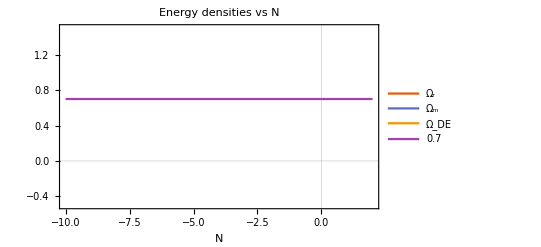

```mathematica
sol1=soln[0,Subscript[Ω, r],Subscript[Ω, m],X,Y,Z,ξ,g,α,κ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 4],Subscript[χ, 5],Subscript[θ, 1]];
tfinal=100;

Plot[Evaluate[{Ωr[t],Ωm[t],1-(Ωr[t]+Ωm[t]),0.7}/.sol1],{t,-10,2},PlotTheme->"Scientific",PlotRange->{-0.5,1.5},PlotLabel->Style["Energy densities  vs  N",FontSize->12,Bold,FontFamily->"Arial Black"],PlotLegends->Placed[LineLegend[{"Ω_r","Ω_m","Ω_DE","0.7"},LabelStyle->7,LegendFunction->(Framed[#,FrameStyle->Directive[Thickness[.05]],RoundingRadius->4]&)],{1-0.11,0.82}],FrameLabel->{Style["N",Bold,FontSize->12,FontFamily->"Beirut"]},FrameStyle-> Bold]
```

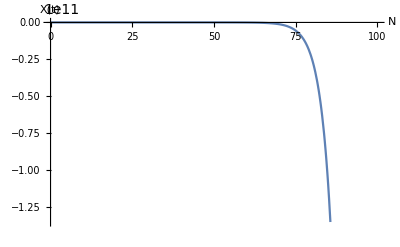

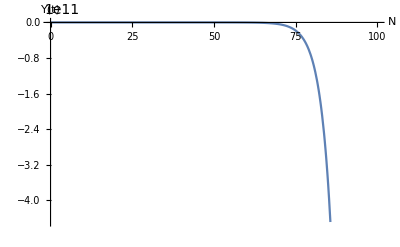

-Graphics-

```mathematica
Plot[Evaluate[{x[t]}/.sol1],{t,0,tfinal},AxesLabel->{"N","X(t)"}]
Plot[Evaluate[{y[t]}/.sol1],{t,0,tfinal},AxesLabel->{"N","Y(t)"}]
Plot[Evaluate[{z[t]}/.sol1],{t,0,tfinal},AxesLabel->{"N","Z(t)"}]
```

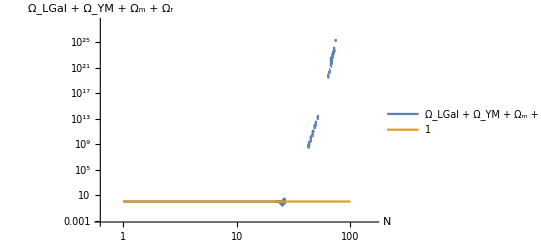

```mathematica
LogLogPlot[Evaluate[{Subscript[θ, 1] (8 x[t] y[t]+6 y[t]^2)+α (10 x[t]^2 y[t]^2-188 x[t] y[t]^3-32 y[t]^4)+Subscript[θ, 4] (-64 x[t] y[t]^3-32 y[t]^4)+κ (2 x[t]^2 y[t]^2-20 x[t] y[t]^3-12 y[t]^4)+Subscript[χ, 3] (-4 x[t]^2 y[t]^2-8 x[t] y[t]^3-4 y[t]^4)+Subscript[χ, 4] (-4 x[t]^2 y[t]^2-8 x[t] y[t]^3-4 y[t]^4)-(432 Subscript[χ, 5] y[t]^4 (x[t]+y[t])^4)/z[t]^4-12 Subscript[χ, 1] z[t]^4-12 Subscript[χ, 2] z[t]^4+ξ (x[t]^2+2 x[t] y[t]+y[t]^2+2 g^2 z[t]^4)+Ωr[t]+Ωm[t],1}/.sol1],{t,1,tfinal},PlotRange->All,AxesLabel->{"N","Ω_LGal + Ω_YM + Ω_m + Ω_r"},PlotLegends->LineLegend[{"Ω_LGal + Ω_YM + Ω_m + Ω_r","1"}]]
```

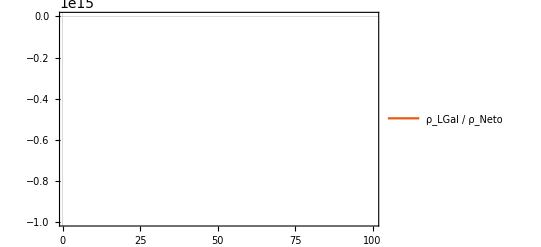

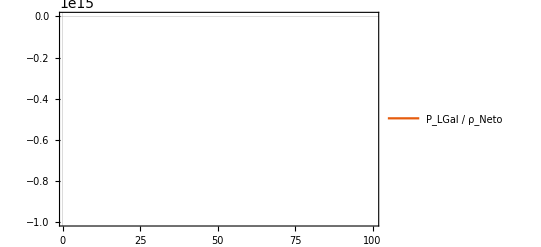

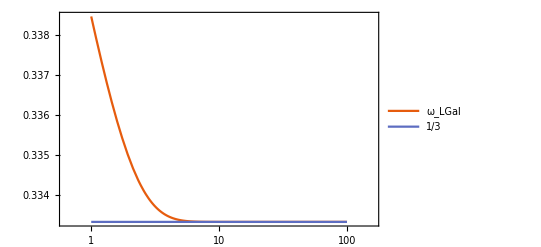

```mathematica
Plot[Evaluate[{Subscript[θ, 1] (8 x[t] y[t]+6 y[t]^2)+α (10 x[t]^2 y[t]^2-188 x[t] y[t]^3-32 y[t]^4)+Subscript[θ, 4] (-64 x[t] y[t]^3-32 y[t]^4)+κ (2 x[t]^2 y[t]^2-20 x[t] y[t]^3-12 y[t]^4)+Subscript[χ, 3] (-4 x[t]^2 y[t]^2-8 x[t] y[t]^3-4 y[t]^4)+Subscript[χ, 4] (-4 x[t]^2 y[t]^2-8 x[t] y[t]^3-4 y[t]^4)-(432 Subscript[χ, 5] y[t]^4 (x[t]+y[t])^4)/z[t]^4-12 Subscript[χ, 1] z[t]^4-12 Subscript[χ, 2] z[t]^4}/.sol1],{t,1,tfinal}, PlotTheme->"Scientific",PlotLegends->LineLegend[{"ρ_LGal / ρ_Neto"}]]

Plot[Evaluate[{ -((2 (-152064 Subscript[χ, 5]^2 x[t]^6 y[t]^9-912384 Subscript[χ, 5]^2 x[t]^5 y[t]^10-152064 Subscript[χ, 5]^2 y[t]^15-528 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) Subscript[χ, 5] y[t]^10 z[t]^4-576 (83 α+16 Subscript[θ, 4]+5 κ) ξ Subscript[χ, 5] y[t]^13 z[t]^4+3456 (Subscript[χ, 1]+Subscript[χ, 2]) Subscript[χ, 5] y[t]^7 z[t]^8+2 (-8 g^2 Subscript[θ, 1] ξ+3 ξ (Subscript[χ, 1]+Subscript[χ, 2])+16 Subscript[θ, 1] (3 Subscript[χ, 1]+Subscript[χ, 2])) z[t]^12+2 ξ y[t]^8 z[t]^4 (-132 Subscript[χ, 5]+(2289 α^2+256 Subscript[θ, 4]^2+16 Subscript[θ, 4] (11 κ+4 (Subscript[χ, 3]+Subscript[χ, 4]))+κ (31 κ+20 (Subscript[χ, 3]+Subscript[χ, 4]))+4 α (396 Subscript[θ, 4]+129 κ+83 (Subscript[χ, 3]+Subscript[χ, 4]))) z[t]^4)-24 Subscript[χ, 5] x[t]^4 y[t]^4 (95040 Subscript[χ, 5] y[t]^7+11 ξ z[t]^4-96 Subscript[θ, 1] y[t] z[t]^4+22 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) y[t]^2 z[t]^4+24 (307 α+96 Subscript[θ, 4]+35 κ-Subscript[θ, 1] ξ+2 Subscript[χ, 3]+2 Subscript[χ, 4]) y[t]^3 z[t]^4+24 (83 α+16 Subscript[θ, 4]+5 κ) ξ y[t]^5 z[t]^4)-96 Subscript[χ, 5] x[t]^3 y[t]^5 (31680 Subscript[χ, 5] y[t]^7+11 ξ z[t]^4-80 Subscript[θ, 1] y[t] z[t]^4+22 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) y[t]^2 z[t]^4+8 (449 α+200 Subscript[θ, 4]+78 κ-3 Subscript[θ, 1] ξ+6 Subscript[χ, 3]+6 Subscript[χ, 4]) y[t]^3 z[t]^4+24 (83 α+16 Subscript[θ, 4]+5 κ) ξ y[t]^5 z[t]^4)+192 Subscript[θ, 1] Subscript[χ, 5] y[t]^9 z[t]^4 (10+6 g^2 ξ z[t]^4+3 Ωr[t])-192 Subscript[χ, 5] y[t]^11 z[t]^4 (29 α+128 Subscript[θ, 4]+57 κ-3 Subscript[θ, 1] ξ+6 Subscript[χ, 3]+6 Subscript[χ, 4]+6 g^2 (83 α+16 Subscript[θ, 4]+5 κ) ξ z[t]^4+3 (83 α+16 Subscript[θ, 4]+5 κ) Ωr[t])-y[t]^4 z[t]^8 (-308 α Subscript[θ, 1]+64 Subscript[θ, 1] Subscript[θ, 4]+36 Subscript[θ, 1] κ-129 α ξ-8 Subscript[θ, 1]^2 ξ+3 κ ξ-Subscript[θ, 1] ξ^2+2 ξ Subscript[χ, 3]+2 ξ Subscript[χ, 4]+2 g^2 ξ (406 α Subscript[θ, 1]+128 Subscript[θ, 1] Subscript[θ, 4]+46 Subscript[θ, 1] κ+83 α ξ+16 Subscript[θ, 4] ξ+5 κ ξ+8 Subscript[θ, 1] Subscript[χ, 3]+8 Subscript[θ, 1] Subscript[χ, 4]) z[t]^4+(406 α Subscript[θ, 1]+128 Subscript[θ, 1] Subscript[θ, 4]+46 Subscript[θ, 1] κ+83 α ξ+16 Subscript[θ, 4] ξ+5 κ ξ+8 Subscript[θ, 1] Subscript[χ, 3]+8 Subscript[θ, 1] Subscript[χ, 4]) Ωr[t])+y[t]^6 z[t]^8 (-7238 α^2-960 α Subscript[θ, 4]+512 Subscript[θ, 4]^2+76 α κ+448 Subscript[θ, 4] κ+90 κ^2-406 α Subscript[θ, 1] ξ-128 Subscript[θ, 1] Subscript[θ, 4] ξ-46 Subscript[θ, 1] κ ξ-83 α ξ^2-16 Subscript[θ, 4] ξ^2-5 κ ξ^2-636 α Subscript[χ, 3]+128 Subscript[θ, 4] Subscript[χ, 3]+68 κ Subscript[χ, 3]-8 Subscript[θ, 1] ξ Subscript[χ, 3]+16 Subscript[χ, 3]^2-636 α Subscript[χ, 4]+128 Subscript[θ, 4] Subscript[χ, 4]+68 κ Subscript[χ, 4]-8 Subscript[θ, 1] ξ Subscript[χ, 4]+32 Subscript[χ, 3] Subscript[χ, 4]+16 Subscript[χ, 4]^2+4 g^2 ξ (2289 α^2+256 Subscript[θ, 4]^2+16 Subscript[θ, 4] (11 κ+4 (Subscript[χ, 3]+Subscript[χ, 4]))+κ (31 κ+20 (Subscript[χ, 3]+Subscript[χ, 4]))+4 α (396 Subscript[θ, 4]+129 κ+83 (Subscript[χ, 3]+Subscript[χ, 4]))) z[t]^4+2 (2289 α^2+256 Subscript[θ, 4]^2+16 Subscript[θ, 4] (11 κ+4 (Subscript[χ, 3]+Subscript[χ, 4]))+κ (31 κ+20 (Subscript[χ, 3]+Subscript[χ, 4]))+4 α (396 Subscript[θ, 4]+129 κ+83 (Subscript[χ, 3]+Subscript[χ, 4]))) Ωr[t])-2 x[t] y[t]^3 (456192 Subscript[χ, 5]^2 y[t]^11+1056 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) Subscript[χ, 5] y[t]^6 z[t]^4+1152 (83 α+16 Subscript[θ, 4]+5 κ) ξ Subscript[χ, 5] y[t]^9 z[t]^4-(77 α ξ+8 Subscript[θ, 1]^2 ξ-ξ (16 Subscript[θ, 4]+9 κ+2 (Subscript[χ, 3]+Subscript[χ, 4]))+Subscript[θ, 1] (ξ^2+16 (Subscript[χ, 3]+Subscript[χ, 4]))) z[t]^8+(-770 α^2+18 κ^2+46 Subscript[θ, 1] κ ξ+5 κ ξ^2+16 Subscript[θ, 4] (2 κ+8 Subscript[θ, 1] ξ+ξ^2)-20 κ Subscript[χ, 3]+8 Subscript[θ, 1] ξ Subscript[χ, 3]-16 Subscript[χ, 3]^2-20 κ Subscript[χ, 4]+8 Subscript[θ, 1] ξ Subscript[χ, 4]-32 Subscript[χ, 3] Subscript[χ, 4]-16 Subscript[χ, 4]^2+α (160 Subscript[θ, 4]-64 κ+406 Subscript[θ, 1] ξ+83 ξ^2+1052 Subscript[χ, 3]+1052 Subscript[χ, 4])) y[t]^2 z[t]^8-3456 (Subscript[χ, 1]+Subscript[χ, 2]) Subscript[χ, 5] y[t]^3 z[t]^8-2 ξ y[t]^4 z[t]^4 (-264 Subscript[χ, 5]+(2289 α^2+256 Subscript[θ, 4]^2+16 Subscript[θ, 4] (11 κ+4 (Subscript[χ, 3]+Subscript[χ, 4]))+κ (31 κ+20 (Subscript[χ, 3]+Subscript[χ, 4]))+4 α (396 Subscript[θ, 4]+129 κ+83 (Subscript[χ, 3]+Subscript[χ, 4]))) z[t]^4)-576 Subscript[θ, 1] Subscript[χ, 5] y[t]^5 z[t]^4 (6+2 g^2 ξ z[t]^4+Ωr[t])+576 Subscript[χ, 5] y[t]^7 z[t]^4 (2 (α+40 Subscript[θ, 4]+18 κ-Subscript[θ, 1] ξ+2 Subscript[χ, 3]+2 Subscript[χ, 4])+2 g^2 (83 α+16 Subscript[θ, 4]+5 κ) ξ z[t]^4+(83 α+16 Subscript[θ, 4]+5 κ) Ωr[t]))+x[t]^2 (-2280960 Subscript[χ, 5]^2 y[t]^13-3168 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) Subscript[χ, 5] y[t]^8 z[t]^4-3456 (83 α+16 Subscript[θ, 4]+5 κ) ξ Subscript[χ, 5] y[t]^11 z[t]^4+4 Subscript[θ, 1] ξ z[t]^8+(-307 α ξ+8 Subscript[θ, 1]^2 ξ-ξ (96 Subscript[θ, 4]+35 κ+2 (Subscript[χ, 3]+Subscript[χ, 4]))+Subscript[θ, 1] (ξ^2+16 (Subscript[χ, 3]+Subscript[χ, 4]))) y[t]^2 z[t]^8-(2030 α^2+46 κ^2+46 Subscript[θ, 1] κ ξ+5 κ ξ^2-132 κ Subscript[χ, 3]+8 Subscript[θ, 1] ξ Subscript[χ, 3]-16 Subscript[χ, 3]^2+α (640 Subscript[θ, 4]+636 κ+406 Subscript[θ, 1] ξ+83 ξ^2-1188 Subscript[χ, 3]-1188 Subscript[χ, 4])+16 Subscript[θ, 4] (8 κ+8 Subscript[θ, 1] ξ+ξ^2-24 Subscript[χ, 3]-24 Subscript[χ, 4])-132 κ Subscript[χ, 4]+8 Subscript[θ, 1] ξ Subscript[χ, 4]-32 Subscript[χ, 3] Subscript[χ, 4]-16 Subscript[χ, 4]^2) y[t]^4 z[t]^8+3456 (Subscript[χ, 1]+Subscript[χ, 2]) Subscript[χ, 5] y[t]^5 z[t]^8+2 ξ y[t]^6 z[t]^4 (-792 Subscript[χ, 5]+(2289 α^2+256 Subscript[θ, 4]^2+16 Subscript[θ, 4] (11 κ+4 (Subscript[χ, 3]+Subscript[χ, 4]))+κ (31 κ+20 (Subscript[χ, 3]+Subscript[χ, 4]))+4 α (396 Subscript[θ, 4]+129 κ+83 (Subscript[χ, 3]+Subscript[χ, 4]))) z[t]^4)+576 Subscript[θ, 1] Subscript[χ, 5] y[t]^7 z[t]^4 (18+2 g^2 ξ z[t]^4+Ωr[t])-576 Subscript[χ, 5] y[t]^9 z[t]^4 (2 (143 α+144 Subscript[θ, 4]+61 κ-3 Subscript[θ, 1] ξ+6 Subscript[χ, 3]+6 Subscript[χ, 4])+2 g^2 (83 α+16 Subscript[θ, 4]+5 κ) ξ z[t]^4+(83 α+16 Subscript[θ, 4]+5 κ) Ωr[t]))+y[t]^2 z[t]^8 (2 (g^2 ξ (208 α+8 Subscript[θ, 1]^2+64 Subscript[θ, 4]+24 κ+Subscript[θ, 1] ξ)-2 (64 Subscript[θ, 4] (3 Subscript[χ, 1]+Subscript[χ, 2])+α (609 Subscript[χ, 1]+193 Subscript[χ, 2])+3 (κ (23 Subscript[χ, 1]+7 Subscript[χ, 2])+4 (Subscript[χ, 1]+Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4])))) z[t]^4+Subscript[θ, 1] (-2 ξ+(8 Subscript[θ, 1]+ξ) Ωr[t]))))/(3 z[t]^4 (576 Subscript[χ, 5] y[t]^7+1152 Subscript[θ, 1] Subscript[χ, 5] y[t]^9-1152 (83 α+16 Subscript[θ, 4]+5 κ) Subscript[χ, 5] y[t]^11-576 Subscript[χ, 5] x[t]^2 y[t]^5 (-1-2 Subscript[θ, 1] y[t]^2+2 (83 α+16 Subscript[θ, 4]+5 κ) y[t]^4)-1152 Subscript[χ, 5] x[t] y[t]^6 (-1-2 Subscript[θ, 1] y[t]^2+2 (83 α+16 Subscript[θ, 4]+5 κ) y[t]^4)+ξ z[t]^4+2 (5 α+8 Subscript[θ, 1]^2+κ+Subscript[θ, 1] ξ-4 Subscript[χ, 3]-4 Subscript[χ, 4]) y[t]^2 z[t]^4-2 (406 α Subscript[θ, 1]+128 Subscript[θ, 1] Subscript[θ, 4]+46 Subscript[θ, 1] κ+83 α ξ+16 Subscript[θ, 4] ξ+5 κ ξ+8 Subscript[θ, 1] Subscript[χ, 3]+8 Subscript[θ, 1] Subscript[χ, 4]) y[t]^4 z[t]^4+4 (2289 α^2+256 Subscript[θ, 4]^2+16 Subscript[θ, 4] (11 κ+4 (Subscript[χ, 3]+Subscript[χ, 4]))+κ (31 κ+20 (Subscript[χ, 3]+Subscript[χ, 4]))+4 α (396 Subscript[θ, 4]+129 κ+83 (Subscript[χ, 3]+Subscript[χ, 4]))) y[t]^6 z[t]^4)))}/.sol1],{t,1,tfinal}, PlotTheme->"Scientific",PlotLegends->LineLegend[{"P_LGal / ρ_Neto"}]]

LogLinearPlot[Evaluate[{(-((2 (-152064 Subscript[χ, 5]^2 x[t]^6 y[t]^9-912384 Subscript[χ, 5]^2 x[t]^5 y[t]^10-152064 Subscript[χ, 5]^2 y[t]^15-528 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) Subscript[χ, 5] y[t]^10 z[t]^4-576 (83 α+16 Subscript[θ, 4]+5 κ) ξ Subscript[χ, 5] y[t]^13 z[t]^4+3456 (Subscript[χ, 1]+Subscript[χ, 2]) Subscript[χ, 5] y[t]^7 z[t]^8+2 (-8 g^2 Subscript[θ, 1] ξ+3 ξ (Subscript[χ, 1]+Subscript[χ, 2])+16 Subscript[θ, 1] (3 Subscript[χ, 1]+Subscript[χ, 2])) z[t]^12+2 ξ y[t]^8 z[t]^4 (-132 Subscript[χ, 5]+(2289 α^2+256 Subscript[θ, 4]^2+16 Subscript[θ, 4] (11 κ+4 (Subscript[χ, 3]+Subscript[χ, 4]))+κ (31 κ+20 (Subscript[χ, 3]+Subscript[χ, 4]))+4 α (396 Subscript[θ, 4]+129 κ+83 (Subscript[χ, 3]+Subscript[χ, 4]))) z[t]^4)-24 Subscript[χ, 5] x[t]^4 y[t]^4 (95040 Subscript[χ, 5] y[t]^7+11 ξ z[t]^4-96 Subscript[θ, 1] y[t] z[t]^4+22 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) y[t]^2 z[t]^4+24 (307 α+96 Subscript[θ, 4]+35 κ-Subscript[θ, 1] ξ+2 Subscript[χ, 3]+2 Subscript[χ, 4]) y[t]^3 z[t]^4+24 (83 α+16 Subscript[θ, 4]+5 κ) ξ y[t]^5 z[t]^4)-96 Subscript[χ, 5] x[t]^3 y[t]^5 (31680 Subscript[χ, 5] y[t]^7+11 ξ z[t]^4-80 Subscript[θ, 1] y[t] z[t]^4+22 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) y[t]^2 z[t]^4+8 (449 α+200 Subscript[θ, 4]+78 κ-3 Subscript[θ, 1] ξ+6 Subscript[χ, 3]+6 Subscript[χ, 4]) y[t]^3 z[t]^4+24 (83 α+16 Subscript[θ, 4]+5 κ) ξ y[t]^5 z[t]^4)+192 Subscript[θ, 1] Subscript[χ, 5] y[t]^9 z[t]^4 (10+6 g^2 ξ z[t]^4+3 Ωr[t])-192 Subscript[χ, 5] y[t]^11 z[t]^4 (29 α+128 Subscript[θ, 4]+57 κ-3 Subscript[θ, 1] ξ+6 Subscript[χ, 3]+6 Subscript[χ, 4]+6 g^2 (83 α+16 Subscript[θ, 4]+5 κ) ξ z[t]^4+3 (83 α+16 Subscript[θ, 4]+5 κ) Ωr[t])-y[t]^4 z[t]^8 (-308 α Subscript[θ, 1]+64 Subscript[θ, 1] Subscript[θ, 4]+36 Subscript[θ, 1] κ-129 α ξ-8 Subscript[θ, 1]^2 ξ+3 κ ξ-Subscript[θ, 1] ξ^2+2 ξ Subscript[χ, 3]+2 ξ Subscript[χ, 4]+2 g^2 ξ (406 α Subscript[θ, 1]+128 Subscript[θ, 1] Subscript[θ, 4]+46 Subscript[θ, 1] κ+83 α ξ+16 Subscript[θ, 4] ξ+5 κ ξ+8 Subscript[θ, 1] Subscript[χ, 3]+8 Subscript[θ, 1] Subscript[χ, 4]) z[t]^4+(406 α Subscript[θ, 1]+128 Subscript[θ, 1] Subscript[θ, 4]+46 Subscript[θ, 1] κ+83 α ξ+16 Subscript[θ, 4] ξ+5 κ ξ+8 Subscript[θ, 1] Subscript[χ, 3]+8 Subscript[θ, 1] Subscript[χ, 4]) Ωr[t])+y[t]^6 z[t]^8 (-7238 α^2-960 α Subscript[θ, 4]+512 Subscript[θ, 4]^2+76 α κ+448 Subscript[θ, 4] κ+90 κ^2-406 α Subscript[θ, 1] ξ-128 Subscript[θ, 1] Subscript[θ, 4] ξ-46 Subscript[θ, 1] κ ξ-83 α ξ^2-16 Subscript[θ, 4] ξ^2-5 κ ξ^2-636 α Subscript[χ, 3]+128 Subscript[θ, 4] Subscript[χ, 3]+68 κ Subscript[χ, 3]-8 Subscript[θ, 1] ξ Subscript[χ, 3]+16 Subscript[χ, 3]^2-636 α Subscript[χ, 4]+128 Subscript[θ, 4] Subscript[χ, 4]+68 κ Subscript[χ, 4]-8 Subscript[θ, 1] ξ Subscript[χ, 4]+32 Subscript[χ, 3] Subscript[χ, 4]+16 Subscript[χ, 4]^2+4 g^2 ξ (2289 α^2+256 Subscript[θ, 4]^2+16 Subscript[θ, 4] (11 κ+4 (Subscript[χ, 3]+Subscript[χ, 4]))+κ (31 κ+20 (Subscript[χ, 3]+Subscript[χ, 4]))+4 α (396 Subscript[θ, 4]+129 κ+83 (Subscript[χ, 3]+Subscript[χ, 4]))) z[t]^4+2 (2289 α^2+256 Subscript[θ, 4]^2+16 Subscript[θ, 4] (11 κ+4 (Subscript[χ, 3]+Subscript[χ, 4]))+κ (31 κ+20 (Subscript[χ, 3]+Subscript[χ, 4]))+4 α (396 Subscript[θ, 4]+129 κ+83 (Subscript[χ, 3]+Subscript[χ, 4]))) Ωr[t])-2 x[t] y[t]^3 (456192 Subscript[χ, 5]^2 y[t]^11+1056 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) Subscript[χ, 5] y[t]^6 z[t]^4+1152 (83 α+16 Subscript[θ, 4]+5 κ) ξ Subscript[χ, 5] y[t]^9 z[t]^4-(77 α ξ+8 Subscript[θ, 1]^2 ξ-ξ (16 Subscript[θ, 4]+9 κ+2 (Subscript[χ, 3]+Subscript[χ, 4]))+Subscript[θ, 1] (ξ^2+16 (Subscript[χ, 3]+Subscript[χ, 4]))) z[t]^8+(-770 α^2+18 κ^2+46 Subscript[θ, 1] κ ξ+5 κ ξ^2+16 Subscript[θ, 4] (2 κ+8 Subscript[θ, 1] ξ+ξ^2)-20 κ Subscript[χ, 3]+8 Subscript[θ, 1] ξ Subscript[χ, 3]-16 Subscript[χ, 3]^2-20 κ Subscript[χ, 4]+8 Subscript[θ, 1] ξ Subscript[χ, 4]-32 Subscript[χ, 3] Subscript[χ, 4]-16 Subscript[χ, 4]^2+α (160 Subscript[θ, 4]-64 κ+406 Subscript[θ, 1] ξ+83 ξ^2+1052 Subscript[χ, 3]+1052 Subscript[χ, 4])) y[t]^2 z[t]^8-3456 (Subscript[χ, 1]+Subscript[χ, 2]) Subscript[χ, 5] y[t]^3 z[t]^8-2 ξ y[t]^4 z[t]^4 (-264 Subscript[χ, 5]+(2289 α^2+256 Subscript[θ, 4]^2+16 Subscript[θ, 4] (11 κ+4 (Subscript[χ, 3]+Subscript[χ, 4]))+κ (31 κ+20 (Subscript[χ, 3]+Subscript[χ, 4]))+4 α (396 Subscript[θ, 4]+129 κ+83 (Subscript[χ, 3]+Subscript[χ, 4]))) z[t]^4)-576 Subscript[θ, 1] Subscript[χ, 5] y[t]^5 z[t]^4 (6+2 g^2 ξ z[t]^4+Ωr[t])+576 Subscript[χ, 5] y[t]^7 z[t]^4 (2 (α+40 Subscript[θ, 4]+18 κ-Subscript[θ, 1] ξ+2 Subscript[χ, 3]+2 Subscript[χ, 4])+2 g^2 (83 α+16 Subscript[θ, 4]+5 κ) ξ z[t]^4+(83 α+16 Subscript[θ, 4]+5 κ) Ωr[t]))+x[t]^2 (-2280960 Subscript[χ, 5]^2 y[t]^13-3168 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) Subscript[χ, 5] y[t]^8 z[t]^4-3456 (83 α+16 Subscript[θ, 4]+5 κ) ξ Subscript[χ, 5] y[t]^11 z[t]^4+4 Subscript[θ, 1] ξ z[t]^8+(-307 α ξ+8 Subscript[θ, 1]^2 ξ-ξ (96 Subscript[θ, 4]+35 κ+2 (Subscript[χ, 3]+Subscript[χ, 4]))+Subscript[θ, 1] (ξ^2+16 (Subscript[χ, 3]+Subscript[χ, 4]))) y[t]^2 z[t]^8-(2030 α^2+46 κ^2+46 Subscript[θ, 1] κ ξ+5 κ ξ^2-132 κ Subscript[χ, 3]+8 Subscript[θ, 1] ξ Subscript[χ, 3]-16 Subscript[χ, 3]^2+α (640 Subscript[θ, 4]+636 κ+406 Subscript[θ, 1] ξ+83 ξ^2-1188 Subscript[χ, 3]-1188 Subscript[χ, 4])+16 Subscript[θ, 4] (8 κ+8 Subscript[θ, 1] ξ+ξ^2-24 Subscript[χ, 3]-24 Subscript[χ, 4])-132 κ Subscript[χ, 4]+8 Subscript[θ, 1] ξ Subscript[χ, 4]-32 Subscript[χ, 3] Subscript[χ, 4]-16 Subscript[χ, 4]^2) y[t]^4 z[t]^8+3456 (Subscript[χ, 1]+Subscript[χ, 2]) Subscript[χ, 5] y[t]^5 z[t]^8+2 ξ y[t]^6 z[t]^4 (-792 Subscript[χ, 5]+(2289 α^2+256 Subscript[θ, 4]^2+16 Subscript[θ, 4] (11 κ+4 (Subscript[χ, 3]+Subscript[χ, 4]))+κ (31 κ+20 (Subscript[χ, 3]+Subscript[χ, 4]))+4 α (396 Subscript[θ, 4]+129 κ+83 (Subscript[χ, 3]+Subscript[χ, 4]))) z[t]^4)+576 Subscript[θ, 1] Subscript[χ, 5] y[t]^7 z[t]^4 (18+2 g^2 ξ z[t]^4+Ωr[t])-576 Subscript[χ, 5] y[t]^9 z[t]^4 (2 (143 α+144 Subscript[θ, 4]+61 κ-3 Subscript[θ, 1] ξ+6 Subscript[χ, 3]+6 Subscript[χ, 4])+2 g^2 (83 α+16 Subscript[θ, 4]+5 κ) ξ z[t]^4+(83 α+16 Subscript[θ, 4]+5 κ) Ωr[t]))+y[t]^2 z[t]^8 (2 (g^2 ξ (208 α+8 Subscript[θ, 1]^2+64 Subscript[θ, 4]+24 κ+Subscript[θ, 1] ξ)-2 (64 Subscript[θ, 4] (3 Subscript[χ, 1]+Subscript[χ, 2])+α (609 Subscript[χ, 1]+193 Subscript[χ, 2])+3 (κ (23 Subscript[χ, 1]+7 Subscript[χ, 2])+4 (Subscript[χ, 1]+Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4])))) z[t]^4+Subscript[θ, 1] (-2 ξ+(8 Subscript[θ, 1]+ξ) Ωr[t]))))/(3 z[t]^4 (576 Subscript[χ, 5] y[t]^7+1152 Subscript[θ, 1] Subscript[χ, 5] y[t]^9-1152 (83 α+16 Subscript[θ, 4]+5 κ) Subscript[χ, 5] y[t]^11-576 Subscript[χ, 5] x[t]^2 y[t]^5 (-1-2 Subscript[θ, 1] y[t]^2+2 (83 α+16 Subscript[θ, 4]+5 κ) y[t]^4)-1152 Subscript[χ, 5] x[t] y[t]^6 (-1-2 Subscript[θ, 1] y[t]^2+2 (83 α+16 Subscript[θ, 4]+5 κ) y[t]^4)+ξ z[t]^4+2 (5 α+8 Subscript[θ, 1]^2+κ+Subscript[θ, 1] ξ-4 Subscript[χ, 3]-4 Subscript[χ, 4]) y[t]^2 z[t]^4-2 (406 α Subscript[θ, 1]+128 Subscript[θ, 1] Subscript[θ, 4]+46 Subscript[θ, 1] κ+83 α ξ+16 Subscript[θ, 4] ξ+5 κ ξ+8 Subscript[θ, 1] Subscript[χ, 3]+8 Subscript[θ, 1] Subscript[χ, 4]) y[t]^4 z[t]^4+4 (2289 α^2+256 Subscript[θ, 4]^2+16 Subscript[θ, 4] (11 κ+4 (Subscript[χ, 3]+Subscript[χ, 4]))+κ (31 κ+20 (Subscript[χ, 3]+Subscript[χ, 4]))+4 α (396 Subscript[θ, 4]+129 κ+83 (Subscript[χ, 3]+Subscript[χ, 4]))) y[t]^6 z[t]^4))))/(Subscript[θ, 1] (8 x[t] y[t]+6 y[t]^2)+α (10 x[t]^2 y[t]^2-188 x[t] y[t]^3-32 y[t]^4)+Subscript[θ, 4] (-64 x[t] y[t]^3-32 y[t]^4)+κ (2 x[t]^2 y[t]^2-20 x[t] y[t]^3-12 y[t]^4)+Subscript[χ, 3] (-4 x[t]^2 y[t]^2-8 x[t] y[t]^3-4 y[t]^4)+Subscript[χ, 4] (-4 x[t]^2 y[t]^2-8 x[t] y[t]^3-4 y[t]^4)-(432 Subscript[χ, 5] y[t]^4 (x[t]+y[t])^4)/z[t]^4-12 Subscript[χ, 1] z[t]^4-12 Subscript[χ, 2] z[t]^4),1/3}/.sol1],{t,1,tfinal}, PlotRange->All,PlotTheme->"Scientific",PlotLegends->LineLegend[{"ω_LGal","1/3"}]]
```

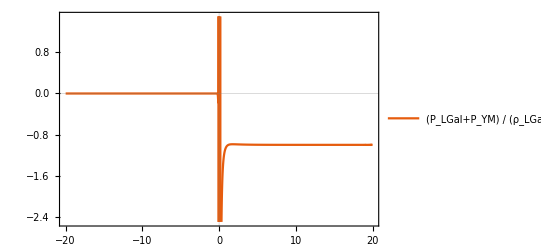

```mathematica
Plot[Evaluate[( -((2 (-152064 Subscript[χ, 5]^2 x[t]^6 y[t]^9-912384 Subscript[χ, 5]^2 x[t]^5 y[t]^10-152064 Subscript[χ, 5]^2 y[t]^15-528 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) Subscript[χ, 5] y[t]^10 z[t]^4-576 (83 α+16 Subscript[θ, 4]+5 κ) ξ Subscript[χ, 5] y[t]^13 z[t]^4+3456 (Subscript[χ, 1]+Subscript[χ, 2]) Subscript[χ, 5] y[t]^7 z[t]^8+2 (-8 g^2 Subscript[θ, 1] ξ+3 ξ (Subscript[χ, 1]+Subscript[χ, 2])+16 Subscript[θ, 1] (3 Subscript[χ, 1]+Subscript[χ, 2])) z[t]^12+2 ξ y[t]^8 z[t]^4 (-132 Subscript[χ, 5]+(2289 α^2+256 Subscript[θ, 4]^2+16 Subscript[θ, 4] (11 κ+4 (Subscript[χ, 3]+Subscript[χ, 4]))+κ (31 κ+20 (Subscript[χ, 3]+Subscript[χ, 4]))+4 α (396 Subscript[θ, 4]+129 κ+83 (Subscript[χ, 3]+Subscript[χ, 4]))) z[t]^4)-24 Subscript[χ, 5] x[t]^4 y[t]^4 (95040 Subscript[χ, 5] y[t]^7+11 ξ z[t]^4-96 Subscript[θ, 1] y[t] z[t]^4+22 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) y[t]^2 z[t]^4+24 (307 α+96 Subscript[θ, 4]+35 κ-Subscript[θ, 1] ξ+2 Subscript[χ, 3]+2 Subscript[χ, 4]) y[t]^3 z[t]^4+24 (83 α+16 Subscript[θ, 4]+5 κ) ξ y[t]^5 z[t]^4)-96 Subscript[χ, 5] x[t]^3 y[t]^5 (31680 Subscript[χ, 5] y[t]^7+11 ξ z[t]^4-80 Subscript[θ, 1] y[t] z[t]^4+22 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) y[t]^2 z[t]^4+8 (449 α+200 Subscript[θ, 4]+78 κ-3 Subscript[θ, 1] ξ+6 Subscript[χ, 3]+6 Subscript[χ, 4]) y[t]^3 z[t]^4+24 (83 α+16 Subscript[θ, 4]+5 κ) ξ y[t]^5 z[t]^4)+192 Subscript[θ, 1] Subscript[χ, 5] y[t]^9 z[t]^4 (10+6 g^2 ξ z[t]^4+3 Ωr[t])-192 Subscript[χ, 5] y[t]^11 z[t]^4 (29 α+128 Subscript[θ, 4]+57 κ-3 Subscript[θ, 1] ξ+6 Subscript[χ, 3]+6 Subscript[χ, 4]+6 g^2 (83 α+16 Subscript[θ, 4]+5 κ) ξ z[t]^4+3 (83 α+16 Subscript[θ, 4]+5 κ) Ωr[t])-y[t]^4 z[t]^8 (-308 α Subscript[θ, 1]+64 Subscript[θ, 1] Subscript[θ, 4]+36 Subscript[θ, 1] κ-129 α ξ-8 Subscript[θ, 1]^2 ξ+3 κ ξ-Subscript[θ, 1] ξ^2+2 ξ Subscript[χ, 3]+2 ξ Subscript[χ, 4]+2 g^2 ξ (406 α Subscript[θ, 1]+128 Subscript[θ, 1] Subscript[θ, 4]+46 Subscript[θ, 1] κ+83 α ξ+16 Subscript[θ, 4] ξ+5 κ ξ+8 Subscript[θ, 1] Subscript[χ, 3]+8 Subscript[θ, 1] Subscript[χ, 4]) z[t]^4+(406 α Subscript[θ, 1]+128 Subscript[θ, 1] Subscript[θ, 4]+46 Subscript[θ, 1] κ+83 α ξ+16 Subscript[θ, 4] ξ+5 κ ξ+8 Subscript[θ, 1] Subscript[χ, 3]+8 Subscript[θ, 1] Subscript[χ, 4]) Ωr[t])+y[t]^6 z[t]^8 (-7238 α^2-960 α Subscript[θ, 4]+512 Subscript[θ, 4]^2+76 α κ+448 Subscript[θ, 4] κ+90 κ^2-406 α Subscript[θ, 1] ξ-128 Subscript[θ, 1] Subscript[θ, 4] ξ-46 Subscript[θ, 1] κ ξ-83 α ξ^2-16 Subscript[θ, 4] ξ^2-5 κ ξ^2-636 α Subscript[χ, 3]+128 Subscript[θ, 4] Subscript[χ, 3]+68 κ Subscript[χ, 3]-8 Subscript[θ, 1] ξ Subscript[χ, 3]+16 Subscript[χ, 3]^2-636 α Subscript[χ, 4]+128 Subscript[θ, 4] Subscript[χ, 4]+68 κ Subscript[χ, 4]-8 Subscript[θ, 1] ξ Subscript[χ, 4]+32 Subscript[χ, 3] Subscript[χ, 4]+16 Subscript[χ, 4]^2+4 g^2 ξ (2289 α^2+256 Subscript[θ, 4]^2+16 Subscript[θ, 4] (11 κ+4 (Subscript[χ, 3]+Subscript[χ, 4]))+κ (31 κ+20 (Subscript[χ, 3]+Subscript[χ, 4]))+4 α (396 Subscript[θ, 4]+129 κ+83 (Subscript[χ, 3]+Subscript[χ, 4]))) z[t]^4+2 (2289 α^2+256 Subscript[θ, 4]^2+16 Subscript[θ, 4] (11 κ+4 (Subscript[χ, 3]+Subscript[χ, 4]))+κ (31 κ+20 (Subscript[χ, 3]+Subscript[χ, 4]))+4 α (396 Subscript[θ, 4]+129 κ+83 (Subscript[χ, 3]+Subscript[χ, 4]))) Ωr[t])-2 x[t] y[t]^3 (456192 Subscript[χ, 5]^2 y[t]^11+1056 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) Subscript[χ, 5] y[t]^6 z[t]^4+1152 (83 α+16 Subscript[θ, 4]+5 κ) ξ Subscript[χ, 5] y[t]^9 z[t]^4-(77 α ξ+8 Subscript[θ, 1]^2 ξ-ξ (16 Subscript[θ, 4]+9 κ+2 (Subscript[χ, 3]+Subscript[χ, 4]))+Subscript[θ, 1] (ξ^2+16 (Subscript[χ, 3]+Subscript[χ, 4]))) z[t]^8+(-770 α^2+18 κ^2+46 Subscript[θ, 1] κ ξ+5 κ ξ^2+16 Subscript[θ, 4] (2 κ+8 Subscript[θ, 1] ξ+ξ^2)-20 κ Subscript[χ, 3]+8 Subscript[θ, 1] ξ Subscript[χ, 3]-16 Subscript[χ, 3]^2-20 κ Subscript[χ, 4]+8 Subscript[θ, 1] ξ Subscript[χ, 4]-32 Subscript[χ, 3] Subscript[χ, 4]-16 Subscript[χ, 4]^2+α (160 Subscript[θ, 4]-64 κ+406 Subscript[θ, 1] ξ+83 ξ^2+1052 Subscript[χ, 3]+1052 Subscript[χ, 4])) y[t]^2 z[t]^8-3456 (Subscript[χ, 1]+Subscript[χ, 2]) Subscript[χ, 5] y[t]^3 z[t]^8-2 ξ y[t]^4 z[t]^4 (-264 Subscript[χ, 5]+(2289 α^2+256 Subscript[θ, 4]^2+16 Subscript[θ, 4] (11 κ+4 (Subscript[χ, 3]+Subscript[χ, 4]))+κ (31 κ+20 (Subscript[χ, 3]+Subscript[χ, 4]))+4 α (396 Subscript[θ, 4]+129 κ+83 (Subscript[χ, 3]+Subscript[χ, 4]))) z[t]^4)-576 Subscript[θ, 1] Subscript[χ, 5] y[t]^5 z[t]^4 (6+2 g^2 ξ z[t]^4+Ωr[t])+576 Subscript[χ, 5] y[t]^7 z[t]^4 (2 (α+40 Subscript[θ, 4]+18 κ-Subscript[θ, 1] ξ+2 Subscript[χ, 3]+2 Subscript[χ, 4])+2 g^2 (83 α+16 Subscript[θ, 4]+5 κ) ξ z[t]^4+(83 α+16 Subscript[θ, 4]+5 κ) Ωr[t]))+x[t]^2 (-2280960 Subscript[χ, 5]^2 y[t]^13-3168 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) Subscript[χ, 5] y[t]^8 z[t]^4-3456 (83 α+16 Subscript[θ, 4]+5 κ) ξ Subscript[χ, 5] y[t]^11 z[t]^4+4 Subscript[θ, 1] ξ z[t]^8+(-307 α ξ+8 Subscript[θ, 1]^2 ξ-ξ (96 Subscript[θ, 4]+35 κ+2 (Subscript[χ, 3]+Subscript[χ, 4]))+Subscript[θ, 1] (ξ^2+16 (Subscript[χ, 3]+Subscript[χ, 4]))) y[t]^2 z[t]^8-(2030 α^2+46 κ^2+46 Subscript[θ, 1] κ ξ+5 κ ξ^2-132 κ Subscript[χ, 3]+8 Subscript[θ, 1] ξ Subscript[χ, 3]-16 Subscript[χ, 3]^2+α (640 Subscript[θ, 4]+636 κ+406 Subscript[θ, 1] ξ+83 ξ^2-1188 Subscript[χ, 3]-1188 Subscript[χ, 4])+16 Subscript[θ, 4] (8 κ+8 Subscript[θ, 1] ξ+ξ^2-24 Subscript[χ, 3]-24 Subscript[χ, 4])-132 κ Subscript[χ, 4]+8 Subscript[θ, 1] ξ Subscript[χ, 4]-32 Subscript[χ, 3] Subscript[χ, 4]-16 Subscript[χ, 4]^2) y[t]^4 z[t]^8+3456 (Subscript[χ, 1]+Subscript[χ, 2]) Subscript[χ, 5] y[t]^5 z[t]^8+2 ξ y[t]^6 z[t]^4 (-792 Subscript[χ, 5]+(2289 α^2+256 Subscript[θ, 4]^2+16 Subscript[θ, 4] (11 κ+4 (Subscript[χ, 3]+Subscript[χ, 4]))+κ (31 κ+20 (Subscript[χ, 3]+Subscript[χ, 4]))+4 α (396 Subscript[θ, 4]+129 κ+83 (Subscript[χ, 3]+Subscript[χ, 4]))) z[t]^4)+576 Subscript[θ, 1] Subscript[χ, 5] y[t]^7 z[t]^4 (18+2 g^2 ξ z[t]^4+Ωr[t])-576 Subscript[χ, 5] y[t]^9 z[t]^4 (2 (143 α+144 Subscript[θ, 4]+61 κ-3 Subscript[θ, 1] ξ+6 Subscript[χ, 3]+6 Subscript[χ, 4])+2 g^2 (83 α+16 Subscript[θ, 4]+5 κ) ξ z[t]^4+(83 α+16 Subscript[θ, 4]+5 κ) Ωr[t]))+y[t]^2 z[t]^8 (2 (g^2 ξ (208 α+8 Subscript[θ, 1]^2+64 Subscript[θ, 4]+24 κ+Subscript[θ, 1] ξ)-2 (64 Subscript[θ, 4] (3 Subscript[χ, 1]+Subscript[χ, 2])+α (609 Subscript[χ, 1]+193 Subscript[χ, 2])+3 (κ (23 Subscript[χ, 1]+7 Subscript[χ, 2])+4 (Subscript[χ, 1]+Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4])))) z[t]^4+Subscript[θ, 1] (-2 ξ+(8 Subscript[θ, 1]+ξ) Ωr[t]))))/(3 z[t]^4 (576 Subscript[χ, 5] y[t]^7+1152 Subscript[θ, 1] Subscript[χ, 5] y[t]^9-1152 (83 α+16 Subscript[θ, 4]+5 κ) Subscript[χ, 5] y[t]^11-576 Subscript[χ, 5] x[t]^2 y[t]^5 (-1-2 Subscript[θ, 1] y[t]^2+2 (83 α+16 Subscript[θ, 4]+5 κ) y[t]^4)-1152 Subscript[χ, 5] x[t] y[t]^6 (-1-2 Subscript[θ, 1] y[t]^2+2 (83 α+16 Subscript[θ, 4]+5 κ) y[t]^4)+ξ z[t]^4+2 (5 α+8 Subscript[θ, 1]^2+κ+Subscript[θ, 1] ξ-4 Subscript[χ, 3]-4 Subscript[χ, 4]) y[t]^2 z[t]^4-2 (406 α Subscript[θ, 1]+128 Subscript[θ, 1] Subscript[θ, 4]+46 Subscript[θ, 1] κ+83 α ξ+16 Subscript[θ, 4] ξ+5 κ ξ+8 Subscript[θ, 1] Subscript[χ, 3]+8 Subscript[θ, 1] Subscript[χ, 4]) y[t]^4 z[t]^4+4 (2289 α^2+256 Subscript[θ, 4]^2+16 Subscript[θ, 4] (11 κ+4 (Subscript[χ, 3]+Subscript[χ, 4]))+κ (31 κ+20 (Subscript[χ, 3]+Subscript[χ, 4]))+4 α (396 Subscript[θ, 4]+129 κ+83 (Subscript[χ, 3]+Subscript[χ, 4]))) y[t]^6 z[t]^4)))+(ξ/3) (x[t]^2+2 x[t] y[t]+y[t]^2+2 g^2 z[t]^4))/(Subscript[θ, 1] (8 x[t] y[t]+6 y[t]^2)+α (10 x[t]^2 y[t]^2-188 x[t] y[t]^3-32 y[t]^4)+Subscript[θ, 4] (-64 x[t] y[t]^3-32 y[t]^4)+κ (2 x[t]^2 y[t]^2-20 x[t] y[t]^3-12 y[t]^4)+Subscript[χ, 3] (-4 x[t]^2 y[t]^2-8 x[t] y[t]^3-4 y[t]^4)+Subscript[χ, 4] (-4 x[t]^2 y[t]^2-8 x[t] y[t]^3-4 y[t]^4)-(432 Subscript[χ, 5] y[t]^4 (x[t]+y[t])^4)/z[t]^4-12 Subscript[χ, 1] z[t]^4-12 Subscript[χ, 2] z[t]^4+ξ (x[t]^2+2 x[t] y[t]+y[t]^2+2 g^2 z[t]^4))/.sol1],{t,-20,20}, PlotTheme->"Scientific",PlotLegends->LineLegend[{"(P_LGal+P_YM) / (ρ_LGal+ρ_YM)"}]]
```

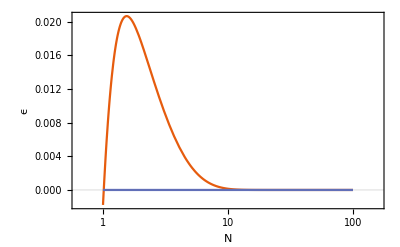

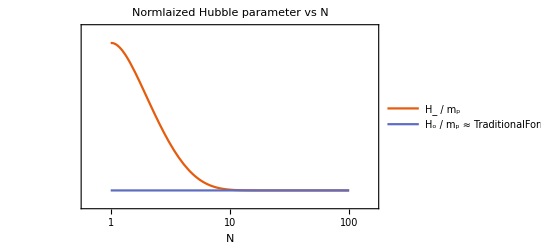

```mathematica
LogLinearPlot[Evaluate[{(304128 Subscript[χ, 5]^2 x[t]^6 y[t]^9+1824768 Subscript[χ, 5]^2 x[t]^5 y[t]^10+304128 Subscript[χ, 5]^2 y[t]^15+528 ξ Subscript[χ, 5] y[t]^8 z[t]^4-192 (2 Subscript[θ, 1]-3 ξ) Subscript[χ, 5] y[t]^9 z[t]^4+1056 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) Subscript[χ, 5] y[t]^10 z[t]^4-768 (359 α+8 Subscript[θ, 4]-3 (2 κ+Subscript[χ, 3]+Subscript[χ, 4])) Subscript[χ, 5] y[t]^11 z[t]^4-2 (α (1526 Subscript[θ, 1]+373 ξ)+ξ (48 Subscript[θ, 4]+11 κ+2 (Subscript[χ, 3]+Subscript[χ, 4]))+2 Subscript[θ, 1] (160 Subscript[θ, 4]+3 (17 κ+4 (Subscript[χ, 3]+Subscript[χ, 4])))) y[t]^4 z[t]^8+8 (5243 α^2+256 Subscript[θ, 4]^2+24 κ^2+13 κ Subscript[χ, 3]-4 Subscript[χ, 3]^2+13 κ Subscript[χ, 4]-8 Subscript[χ, 3] Subscript[χ, 4]-4 Subscript[χ, 4]^2+8 Subscript[θ, 4] (19 κ+8 (Subscript[χ, 3]+Subscript[χ, 4]))+α (2616 Subscript[θ, 4]+755 κ+657 (Subscript[χ, 3]+Subscript[χ, 4]))) y[t]^6 z[t]^8+48 Subscript[χ, 5] x[t]^4 y[t]^4 (95040 Subscript[χ, 5] y[t]^7+11 ξ z[t]^4+12 (-8 Subscript[θ, 1]+ξ) y[t] z[t]^4+22 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) y[t]^2 z[t]^4+24 (307 α+96 Subscript[θ, 4]+35 κ+2 Subscript[χ, 3]+2 Subscript[χ, 4]) y[t]^3 z[t]^4)+192 Subscript[χ, 5] x[t]^3 y[t]^5 (31680 Subscript[χ, 5] y[t]^7+11 ξ z[t]^4+4 (-20 Subscript[θ, 1]+3 ξ) y[t] z[t]^4+22 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) y[t]^2 z[t]^4+8 (449 α+200 Subscript[θ, 4]+6 (13 κ+Subscript[χ, 3]+Subscript[χ, 4])) y[t]^3 z[t]^4)+576 Subscript[χ, 5] y[t]^7 z[t]^4 (3+2 (g^2 ξ-6 (Subscript[χ, 1]+Subscript[χ, 2])) z[t]^4+Ωr[t])+y[t]^2 z[t]^8 (30 α+48 Subscript[θ, 1]^2+6 κ+10 Subscript[θ, 1] ξ+ξ^2-24 Subscript[χ, 3]-24 Subscript[χ, 4]+4 (-g^2 ξ (203 α+64 Subscript[θ, 4]+23 κ+4 Subscript[χ, 3]+4 Subscript[χ, 4])+2 (64 Subscript[θ, 4] (3 Subscript[χ, 1]+Subscript[χ, 2])+α (609 Subscript[χ, 1]+193 Subscript[χ, 2])+3 (κ (23 Subscript[χ, 1]+7 Subscript[χ, 2])+4 (Subscript[χ, 1]+Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4])))) z[t]^4+10 α Ωr[t]+2 κ Ωr[t]-8 Subscript[χ, 3] Ωr[t]-8 Subscript[χ, 4] Ωr[t])+z[t]^8 (2 (g^2 ξ (16 Subscript[θ, 1]+ξ)-2 (3 ξ (Subscript[χ, 1]+Subscript[χ, 2])+16 Subscript[θ, 1] (3 Subscript[χ, 1]+Subscript[χ, 2]))) z[t]^4+ξ (3+Ωr[t]))+2 x[t] y[t] (912384 Subscript[χ, 5]^2 y[t]^13+1056 ξ Subscript[χ, 5] y[t]^6 z[t]^4-1152 (3 Subscript[θ, 1]-ξ) Subscript[χ, 5] y[t]^7 z[t]^4+2112 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) Subscript[χ, 5] y[t]^8 z[t]^4-1152 (247 α-32 Subscript[θ, 4]-21 κ-4 Subscript[χ, 3]-4 Subscript[χ, 4]) Subscript[χ, 5] y[t]^9 z[t]^4+ξ^2 z[t]^8-4 (36 α ξ-8 Subscript[θ, 4] ξ-5 κ ξ+8 Subscript[θ, 1] Subscript[χ, 3]+ξ Subscript[χ, 3]+8 Subscript[θ, 1] Subscript[χ, 4]+ξ Subscript[χ, 4]) y[t]^2 z[t]^8-4 (385 α^2-16 Subscript[θ, 4] κ-9 κ^2+10 κ Subscript[χ, 3]+8 Subscript[χ, 3]^2+10 κ Subscript[χ, 4]+16 Subscript[χ, 3] Subscript[χ, 4]+8 Subscript[χ, 4]^2-2 α (40 Subscript[θ, 4]-16 κ+263 (Subscript[χ, 3]+Subscript[χ, 4]))) y[t]^4 z[t]^8+576 Subscript[χ, 5] y[t]^5 z[t]^4 (3+2 (g^2 ξ-6 (Subscript[χ, 1]+Subscript[χ, 2])) z[t]^4+Ωr[t]))+x[t]^2 (4561920 Subscript[χ, 5]^2 y[t]^13+3168 ξ Subscript[χ, 5] y[t]^6 z[t]^4-3456 (5 Subscript[θ, 1]-ξ) Subscript[χ, 5] y[t]^7 z[t]^4+6336 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) Subscript[χ, 5] y[t]^8 z[t]^4+1152 (37 α+240 Subscript[θ, 4]+107 κ+12 Subscript[χ, 3]+12 Subscript[χ, 4]) Subscript[χ, 5] y[t]^9 z[t]^4+ξ (-8 Subscript[θ, 1]+ξ) z[t]^8+4 (156 α ξ+48 Subscript[θ, 4] ξ+18 κ ξ-8 Subscript[θ, 1] Subscript[χ, 3]-ξ Subscript[χ, 3]-8 Subscript[θ, 1] Subscript[χ, 4]-ξ Subscript[χ, 4]) y[t]^2 z[t]^8+4 (1015 α^2+23 κ^2-66 κ Subscript[χ, 3]-8 Subscript[χ, 3]^2-66 κ Subscript[χ, 4]-16 Subscript[χ, 3] Subscript[χ, 4]-8 Subscript[χ, 4]^2+64 Subscript[θ, 4] (κ-3 (Subscript[χ, 3]+Subscript[χ, 4]))+α (320 Subscript[θ, 4]+6 (53 κ-99 (Subscript[χ, 3]+Subscript[χ, 4])))) y[t]^4 z[t]^8+576 Subscript[χ, 5] y[t]^5 z[t]^4 (3+2 (g^2 ξ-6 (Subscript[χ, 1]+Subscript[χ, 2])) z[t]^4+Ωr[t])))/(2 z[t]^4 (576 Subscript[χ, 5] y[t]^7+1152 Subscript[θ, 1] Subscript[χ, 5] y[t]^9-1152 (83 α+16 Subscript[θ, 4]+5 κ) Subscript[χ, 5] y[t]^11-576 Subscript[χ, 5] x[t]^2 y[t]^5 (-1-2 Subscript[θ, 1] y[t]^2+2 (83 α+16 Subscript[θ, 4]+5 κ) y[t]^4)-1152 Subscript[χ, 5] x[t] y[t]^6 (-1-2 Subscript[θ, 1] y[t]^2+2 (83 α+16 Subscript[θ, 4]+5 κ) y[t]^4)+ξ z[t]^4+2 (5 α+8 Subscript[θ, 1]^2+κ+Subscript[θ, 1] ξ-4 Subscript[χ, 3]-4 Subscript[χ, 4]) y[t]^2 z[t]^4-2 (406 α Subscript[θ, 1]+128 Subscript[θ, 1] Subscript[θ, 4]+46 Subscript[θ, 1] κ+83 α ξ+16 Subscript[θ, 4] ξ+5 κ ξ+8 Subscript[θ, 1] Subscript[χ, 3]+8 Subscript[θ, 1] Subscript[χ, 4]) y[t]^4 z[t]^4+4 (2289 α^2+256 Subscript[θ, 4]^2+16 Subscript[θ, 4] (11 κ+4 (Subscript[χ, 3]+Subscript[χ, 4]))+κ (31 κ+20 (Subscript[χ, 3]+Subscript[χ, 4]))+4 α (396 Subscript[θ, 4]+129 κ+83 (Subscript[χ, 3]+Subscript[χ, 4]))) y[t]^6 z[t]^4)),0}/.sol1],{t,1,tfinal},PlotTheme->"Scientific", PlotRange->All,AxesLabel->{"N","ϵ"}]

LogLogPlot[Evaluate[{y[t]^2/z[t]^2,(β/γ)^2}/.sol1],{t,1,tfinal},PlotTheme->"Scientific",PlotRange->All,PlotLabel->Style["Normlaized Hubble parameter  vs  N",FontSize->12,Bold,FontFamily->"Arial Black"],PlotLegends->Placed[LineLegend[{"H_ / m_p",StringForm["H_o / m_p ≈  ``",(β/γ)^2//ScientificForm]},LabelStyle->12,LegendFunction->(Framed[#,FrameStyle->Directive[Thickness[.05]],RoundingRadius->4]&)],{1-(0.43)/2-0.12,0.78}],FrameLabel->{Style["N",Bold,FontSize->12,FontFamily->"Beirut"]},FrameStyle-> Bold]
```

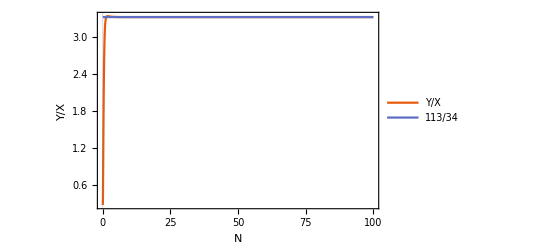

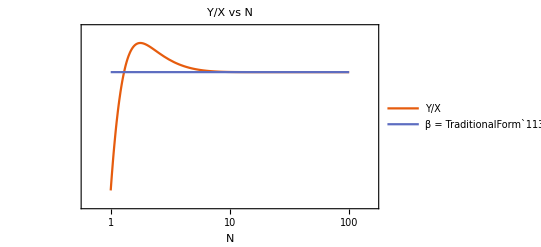

```mathematica
Plot[Evaluate[{y[t]/x[t],β}/.sol1],{t,0,tfinal},PlotTheme->"Scientific",PlotRange->All,AxesLabel->{"N","Y/X"},PlotLegends->LineLegend[{"Y/X",β}]]

LogLogPlot[Evaluate[{y[t]/x[t],Abs[β]}/.sol1],{t,1,tfinal},PlotTheme->"Scientific",PlotRange->All,PlotLabel->Style["Y/X  vs  N",FontSize->12,Bold,FontFamily->"Arial Black"],PlotLegends->Placed[LineLegend[{"Y/X",StringForm["β = `` ≃ ``",Rationalize[β],N[β]]},LabelStyle->12,LegendFunction->(Framed[#,FrameStyle->Directive[Thickness[.05]],RoundingRadius->4]&)],{1-(0.28)/2-0.12,0.25}],FrameLabel->{Style["N",Bold,FontSize->12,FontFamily->"Beirut"]},FrameStyle-> Bold]
```

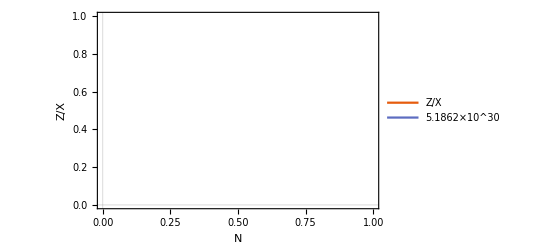

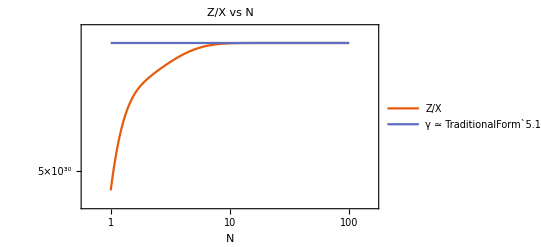

```mathematica
Plot[Evaluate[{z[t]/x[t],γ}/.sol1],{t,0,tfinal},PlotTheme->"Scientific",AxesLabel->{"N","Z/X"},PlotRange->All,PlotLegends->LineLegend[{"Z/X",γ}]]

LogLogPlot[Evaluate[{z[t]/x[t],γ}/.sol1],{t,1,tfinal},PlotTheme->"Scientific",PlotRange->All,PlotLabel->Style["Z/X  vs  N",FontSize->12,Bold,FontFamily->"Arial Black"],PlotLegends->Placed[LineLegend[{"Z/X",StringForm["γ ≃ ``",N[γ]]},LabelStyle->12,LegendFunction->(Framed[#,FrameStyle->Directive[Thickness[.05]],RoundingRadius->4]&)],{1-(0.35)/2-0.12,0.25}],FrameLabel->{Style["N",Bold,FontSize->12,FontFamily->"Beirut"]},FrameStyle-> Bold]
```

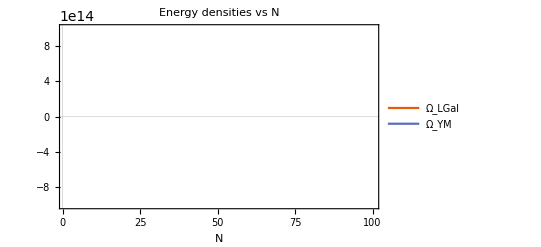

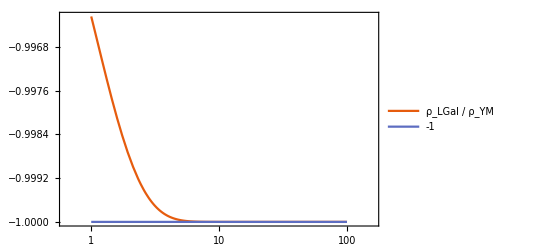

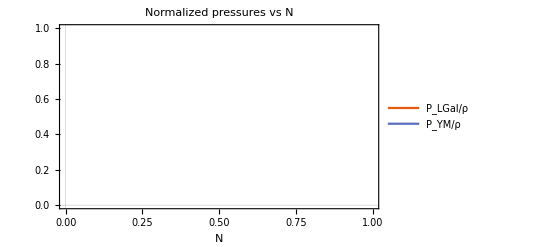

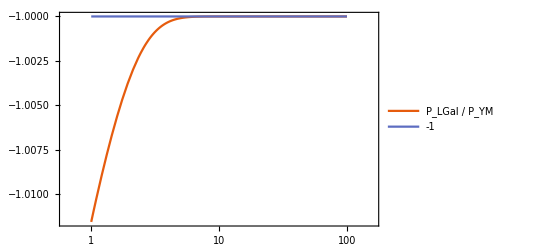

```mathematica
Plot[Evaluate[{(Subscript[θ, 1] (8 x[t] y[t]+6 y[t]^2)+α (10 x[t]^2 y[t]^2-188 x[t] y[t]^3-32 y[t]^4)+Subscript[θ, 4] (-64 x[t] y[t]^3-32 y[t]^4)+κ (2 x[t]^2 y[t]^2-20 x[t] y[t]^3-12 y[t]^4)+Subscript[χ, 3] (-4 x[t]^2 y[t]^2-8 x[t] y[t]^3-4 y[t]^4)+Subscript[χ, 4] (-4 x[t]^2 y[t]^2-8 x[t] y[t]^3-4 y[t]^4)-(432 Subscript[χ, 5] y[t]^4 (x[t]+y[t])^4)/z[t]^4-12 Subscript[χ, 1] z[t]^4-12 Subscript[χ, 2] z[t]^4),(x[t]^2+2 x[t] y[t]+y[t]^2+2 g^2 z[t]^4)ξ}/.sol1],{t,1,tfinal}, PlotTheme->"Scientific",PlotLabel->Style["Energy densities  vs  N",FontSize->12,Bold,FontFamily->"Arial Black"],PlotLegends->Placed[LineLegend[{"Ω_LGal","Ω_YM"},LabelStyle->12,LegendFunction->(Framed[#,FrameStyle->Directive[Thickness[.05]],RoundingRadius->4]&)],{(0.1)/2+0.12,0.23}],FrameLabel->{Style["N",Bold,FontSize->12,FontFamily->"Beirut"]},FrameStyle-> Bold]


LogLinearPlot[{Evaluate[{(Subscript[θ, 1] (8 x[t] y[t]+6 y[t]^2)+α (10 x[t]^2 y[t]^2-188 x[t] y[t]^3-32 y[t]^4)+Subscript[θ, 4] (-64 x[t] y[t]^3-32 y[t]^4)+κ (2 x[t]^2 y[t]^2-20 x[t] y[t]^3-12 y[t]^4)+Subscript[χ, 3] (-4 x[t]^2 y[t]^2-8 x[t] y[t]^3-4 y[t]^4)+Subscript[χ, 4] (-4 x[t]^2 y[t]^2-8 x[t] y[t]^3-4 y[t]^4)-(432 Subscript[χ, 5] y[t]^4 (x[t]+y[t])^4)/z[t]^4-12 Subscript[χ, 1] z[t]^4-12 Subscript[χ, 2] z[t]^4)/((x[t]^2+2 x[t] y[t]+y[t]^2+2 g^2 z[t]^4)ξ)}/.sol1],-1},{t,1,tfinal},PlotRange->All,PlotTheme->"Scientific",PlotLegends->LineLegend[{"ρ_LGal / ρ_YM","-1"}]]


Plot[Evaluate[{(2 (-152064 Subscript[χ, 5]^2 y[t]^9 (x[t]+y[t])^6 (-1+2 Subscript[θ, 1] y[t]^2)+24 Subscript[χ, 5] y[t]^4 (x[t]+y[t])^2 z[t]^4 (11 ξ x[t]^2+22 ξ x[t] y[t]+11 ξ y[t]^2+110 α x[t]^2 y[t]^2+22 κ x[t]^2 y[t]^2-88 Subscript[χ, 4] x[t]^2 y[t]^2+220 α x[t] y[t]^3+44 κ x[t] y[t]^3-176 Subscript[χ, 4] x[t] y[t]^3+7368 α x[t]^2 y[t]^3+2304 Subscript[θ, 4] x[t]^2 y[t]^3+840 κ x[t]^2 y[t]^3+48 Subscript[χ, 4] x[t]^2 y[t]^3+110 α y[t]^4+22 κ y[t]^4-88 Subscript[χ, 4] y[t]^4-368 α x[t] y[t]^4+1792 Subscript[θ, 4] x[t] y[t]^4+816 κ x[t] y[t]^4+96 Subscript[χ, 4] x[t] y[t]^4+232 α y[t]^5+1024 Subscript[θ, 4] y[t]^5+456 κ y[t]^5+48 Subscript[χ, 4] y[t]^5+1992 α ξ x[t]^2 y[t]^5+384 Subscript[θ, 4] ξ x[t]^2 y[t]^5+120 κ ξ x[t]^2 y[t]^5+3984 α ξ x[t] y[t]^6+768 Subscript[θ, 4] ξ x[t] y[t]^6+240 κ ξ x[t] y[t]^6+1992 α ξ y[t]^7+384 Subscript[θ, 4] ξ y[t]^7+120 κ ξ y[t]^7+8 Subscript[χ, 3] y[t]^2 (x[t]+y[t])^2 (-11+6 y[t])+16 Subscript[θ, 1]^2 y[t]^2 (2 x[t] y[t] (11+16 y[t])+y[t]^2 (11+20 y[t])+x[t]^2 (11+24 y[t]))-144 Subscript[χ, 1] y[t] z[t]^4-144 Subscript[χ, 2] y[t] z[t]^4+3984 g^2 α ξ y[t]^5 z[t]^4+768 g^2 Subscript[θ, 4] ξ y[t]^5 z[t]^4+240 g^2 κ ξ y[t]^5 z[t]^4-2 Subscript[θ, 1] y[t]^2 (11 ξ x[t]^2+22 ξ x[t] y[t]+24 ξ x[t]^2 y[t]+11 ξ y[t]^2+48 ξ x[t] y[t]^2+2398 α x[t]^2 y[t]^2+286 κ x[t]^2 y[t]^2-88 Subscript[χ, 4] x[t]^2 y[t]^2+24 ξ y[t]^3+4796 α x[t] y[t]^3+572 κ x[t] y[t]^3-176 Subscript[χ, 4] x[t] y[t]^3+15336 α x[t]^2 y[t]^3+1320 κ x[t]^2 y[t]^3+48 Subscript[χ, 4] x[t]^2 y[t]^3+2398 α y[t]^4+286 κ y[t]^4-88 Subscript[χ, 4] y[t]^4+10256 α x[t] y[t]^4+1456 κ x[t] y[t]^4+96 Subscript[χ, 4] x[t] y[t]^4+6872 α y[t]^5+856 κ y[t]^5+48 Subscript[χ, 4] y[t]^5+8 Subscript[χ, 3] y[t]^2 (x[t]+y[t])^2 (-11+6 y[t])+64 Subscript[θ, 4] y[t]^2 (2 x[t] y[t] (11+30 y[t])+y[t]^2 (11+36 y[t])+x[t]^2 (11+60 y[t]))+48 g^2 ξ y[t] z[t]^4-144 Subscript[χ, 1] y[t] z[t]^4-144 Subscript[χ, 2] y[t] z[t]^4))+z[t]^8 (307 α ξ x[t]^2 y[t]^2+35 κ ξ x[t]^2 y[t]^2+2 ξ Subscript[χ, 3] x[t]^2 y[t]^2+2 ξ Subscript[χ, 4] x[t]^2 y[t]^2-154 α ξ x[t] y[t]^3+18 κ ξ x[t] y[t]^3+4 ξ Subscript[χ, 3] x[t] y[t]^3+4 ξ Subscript[χ, 4] x[t] y[t]^3-129 α ξ y[t]^4+3 κ ξ y[t]^4+2 ξ Subscript[χ, 3] y[t]^4+2 ξ Subscript[χ, 4] y[t]^4+2030 α^2 x[t]^2 y[t]^4+636 α κ x[t]^2 y[t]^4+46 κ^2 x[t]^2 y[t]^4+83 α ξ^2 x[t]^2 y[t]^4+5 κ ξ^2 x[t]^2 y[t]^4-1188 α Subscript[χ, 3] x[t]^2 y[t]^4-132 κ Subscript[χ, 3] x[t]^2 y[t]^4-16 Subscript[χ, 3]^2 x[t]^2 y[t]^4-1188 α Subscript[χ, 4] x[t]^2 y[t]^4-132 κ Subscript[χ, 4] x[t]^2 y[t]^4-32 Subscript[χ, 3] Subscript[χ, 4] x[t]^2 y[t]^4-16 Subscript[χ, 4]^2 x[t]^2 y[t]^4-1540 α^2 x[t] y[t]^5-128 α κ x[t] y[t]^5+36 κ^2 x[t] y[t]^5+166 α ξ^2 x[t] y[t]^5+10 κ ξ^2 x[t] y[t]^5+2104 α Subscript[χ, 3] x[t] y[t]^5-40 κ Subscript[χ, 3] x[t] y[t]^5-32 Subscript[χ, 3]^2 x[t] y[t]^5+2104 α Subscript[χ, 4] x[t] y[t]^5-40 κ Subscript[χ, 4] x[t] y[t]^5-64 Subscript[χ, 3] Subscript[χ, 4] x[t] y[t]^5-32 Subscript[χ, 4]^2 x[t] y[t]^5+7238 α^2 y[t]^6-76 α κ y[t]^6-90 κ^2 y[t]^6+83 α ξ^2 y[t]^6+5 κ ξ^2 y[t]^6+636 α Subscript[χ, 3] y[t]^6-68 κ Subscript[χ, 3] y[t]^6-16 Subscript[χ, 3]^2 y[t]^6+636 α Subscript[χ, 4] y[t]^6-68 κ Subscript[χ, 4] y[t]^6-32 Subscript[χ, 3] Subscript[χ, 4] y[t]^6-16 Subscript[χ, 4]^2 y[t]^6-4578 α^2 ξ x[t]^2 y[t]^6-1032 α κ ξ x[t]^2 y[t]^6-62 κ^2 ξ x[t]^2 y[t]^6-664 α ξ Subscript[χ, 3] x[t]^2 y[t]^6-40 κ ξ Subscript[χ, 3] x[t]^2 y[t]^6-664 α ξ Subscript[χ, 4] x[t]^2 y[t]^6-40 κ ξ Subscript[χ, 4] x[t]^2 y[t]^6-9156 α^2 ξ x[t] y[t]^7-2064 α κ ξ x[t] y[t]^7-124 κ^2 ξ x[t] y[t]^7-1328 α ξ Subscript[χ, 3] x[t] y[t]^7-80 κ ξ Subscript[χ, 3] x[t] y[t]^7-1328 α ξ Subscript[χ, 4] x[t] y[t]^7-80 κ ξ Subscript[χ, 4] x[t] y[t]^7-4578 α^2 ξ y[t]^8-1032 α κ ξ y[t]^8-62 κ^2 ξ y[t]^8-664 α ξ Subscript[χ, 3] y[t]^8-40 κ ξ Subscript[χ, 3] y[t]^8-664 α ξ Subscript[χ, 4] y[t]^8-40 κ ξ Subscript[χ, 4] y[t]^8-6 ξ Subscript[χ, 1] z[t]^4-6 ξ Subscript[χ, 2] z[t]^4-416 g^2 α ξ y[t]^2 z[t]^4-48 g^2 κ ξ y[t]^2 z[t]^4+2436 α Subscript[χ, 1] y[t]^2 z[t]^4+276 κ Subscript[χ, 1] y[t]^2 z[t]^4+772 α Subscript[χ, 2] y[t]^2 z[t]^4+84 κ Subscript[χ, 2] y[t]^2 z[t]^4+48 Subscript[χ, 1] Subscript[χ, 3] y[t]^2 z[t]^4+48 Subscript[χ, 2] Subscript[χ, 3] y[t]^2 z[t]^4+48 Subscript[χ, 1] Subscript[χ, 4] y[t]^2 z[t]^4+48 Subscript[χ, 2] Subscript[χ, 4] y[t]^2 z[t]^4+166 g^2 α ξ^2 y[t]^4 z[t]^4+10 g^2 κ ξ^2 y[t]^4 z[t]^4-9156 g^2 α^2 ξ y[t]^6 z[t]^4-2064 g^2 α κ ξ y[t]^6 z[t]^4-124 g^2 κ^2 ξ y[t]^6 z[t]^4-1328 g^2 α ξ Subscript[χ, 3] y[t]^6 z[t]^4-80 g^2 κ ξ Subscript[χ, 3] y[t]^6 z[t]^4-1328 g^2 α ξ Subscript[χ, 4] y[t]^6 z[t]^4-80 g^2 κ ξ Subscript[χ, 4] y[t]^6 z[t]^4-512 Subscript[θ, 4]^2 y[t]^6 (1+ξ x[t]^2+2 ξ x[t] y[t]+ξ y[t]^2+2 g^2 ξ z[t]^4)+8 Subscript[θ, 1]^2 y[t]^2 (2 ξ x[t]^2-ξ y[t]^2+406 α x[t]^2 y[t]^2+46 κ x[t]^2 y[t]^2+12 Subscript[χ, 4] x[t]^2 y[t]^2-308 α x[t] y[t]^3+36 κ x[t] y[t]^3+24 Subscript[χ, 4] x[t] y[t]^3+4 Subscript[χ, 4] y[t]^4+64 Subscript[θ, 4] x[t] y[t]^2 (2 x[t]+y[t])+4 Subscript[χ, 3] y[t]^2 (3 x[t]^2+6 x[t] y[t]+y[t]^2)-8 g^2 ξ z[t]^4+36 Subscript[χ, 1] z[t]^4+4 Subscript[χ, 2] z[t]^4)-2 Subscript[θ, 1] y[t]^2 (ξ^2 x[t]^2+2 ξ^2 x[t] y[t]+ξ^2 y[t]^2+545 α ξ x[t]^2 y[t]^2+45 κ ξ x[t]^2 y[t]^2-6 ξ Subscript[χ, 4] x[t]^2 y[t]^2-342 α ξ x[t] y[t]^3-2 κ ξ x[t] y[t]^3-12 ξ Subscript[χ, 4] x[t] y[t]^3-389 α ξ y[t]^4-17 κ ξ y[t]^4-6 ξ Subscript[χ, 4] y[t]^4+44254 α^2 x[t]^2 y[t]^4+10292 α κ x[t]^2 y[t]^4+598 κ^2 x[t]^2 y[t]^4+556 α Subscript[χ, 4] x[t]^2 y[t]^4-4 κ Subscript[χ, 4] x[t]^2 y[t]^4-16 Subscript[χ, 4]^2 x[t]^2 y[t]^4-33572 α^2 x[t] y[t]^5-80 α κ x[t] y[t]^5+468 κ^2 x[t] y[t]^5+5592 α Subscript[χ, 4] x[t] y[t]^5+216 κ Subscript[χ, 4] x[t] y[t]^5-32 Subscript[χ, 4]^2 x[t] y[t]^5+16786 α^2 y[t]^6-1500 α κ y[t]^6-54 κ^2 y[t]^6+1052 α Subscript[χ, 4] y[t]^6-20 κ Subscript[χ, 4] y[t]^6-16 Subscript[χ, 4]^2 y[t]^6-16 Subscript[χ, 3]^2 y[t]^4 (x[t]+y[t])^2-512 Subscript[θ, 4]^2 y[t]^4 (-8 x[t]^2-4 x[t] y[t]+y[t]^2)+2 g^2 ξ^2 z[t]^4-6 ξ Subscript[χ, 1] z[t]^4-6 ξ Subscript[χ, 2] z[t]^4-1932 g^2 α ξ y[t]^2 z[t]^4-148 g^2 κ ξ y[t]^2 z[t]^4+9156 α Subscript[χ, 1] y[t]^2 z[t]^4+612 κ Subscript[χ, 1] y[t]^2 z[t]^4+2180 α Subscript[χ, 2] y[t]^2 z[t]^4+100 κ Subscript[χ, 2] y[t]^2 z[t]^4-16 g^2 ξ Subscript[χ, 4] y[t]^2 z[t]^4+48 Subscript[χ, 1] Subscript[χ, 4] y[t]^2 z[t]^4+48 Subscript[χ, 2] Subscript[χ, 4] y[t]^2 z[t]^4-2 Subscript[χ, 3] y[t]^2 (3 ξ x[t]^2+6 ξ x[t] y[t]+3 ξ y[t]^2-278 α x[t]^2 y[t]^2+2 κ x[t]^2 y[t]^2-2796 α x[t] y[t]^3-108 κ x[t] y[t]^3-526 α y[t]^4+10 κ y[t]^4+16 Subscript[χ, 4] y[t]^2 (x[t]+y[t])^2+8 g^2 ξ z[t]^4-24 Subscript[χ, 1] z[t]^4-24 Subscript[χ, 2] z[t]^4)+32 Subscript[θ, 4] y[t]^2 (4 ξ x[t]^2-ξ x[t] y[t]-2 ξ y[t]^2+842 α x[t]^2 y[t]^2+98 κ x[t]^2 y[t]^2-90 α x[t] y[t]^3+62 κ x[t] y[t]^3+24 Subscript[χ, 3] x[t] y[t]^3+24 Subscript[χ, 4] x[t] y[t]^3-32 α y[t]^4-12 κ y[t]^4-14 g^2 ξ z[t]^4+60 Subscript[χ, 1] z[t]^4+12 Subscript[χ, 2] z[t]^4))-16 Subscript[θ, 4] y[t]^2 (-6 ξ x[t]^2-2 ξ x[t] y[t]-40 α x[t]^2 y[t]^2-8 κ x[t]^2 y[t]^2-ξ^2 x[t]^2 y[t]^2-20 α x[t] y[t]^3-4 κ x[t] y[t]^3-2 ξ^2 x[t] y[t]^3-60 α y[t]^4+28 κ y[t]^4-ξ^2 y[t]^4+198 α ξ x[t]^2 y[t]^4+22 κ ξ x[t]^2 y[t]^4+396 α ξ x[t] y[t]^5+44 κ ξ x[t] y[t]^5+198 α ξ y[t]^6+22 κ ξ y[t]^6+8 g^2 ξ z[t]^4-48 Subscript[χ, 1] z[t]^4-16 Subscript[χ, 2] z[t]^4-2 g^2 ξ^2 y[t]^2 z[t]^4+396 g^2 α ξ y[t]^4 z[t]^4+44 g^2 κ ξ y[t]^4 z[t]^4+8 Subscript[χ, 3] (2 ξ x[t] y[t]^5+x[t]^2 y[t]^2 (3+ξ y[t]^2)+y[t]^4 (1+ξ y[t]^2+2 g^2 ξ z[t]^4))+8 Subscript[χ, 4] (2 ξ x[t] y[t]^5+x[t]^2 y[t]^2 (3+ξ y[t]^2)+y[t]^4 (1+ξ y[t]^2+2 g^2 ξ z[t]^4))))))/(3 z[t]^4 (-576 Subscript[χ, 5] y[t]^5 (x[t]+y[t])^2 (-1-2 Subscript[θ, 1] y[t]^2+166 α y[t]^4+32 Subscript[θ, 4] y[t]^4+10 κ y[t]^4)+(ξ+10 α y[t]^2+16 Subscript[θ, 1]^2 y[t]^2+2 κ y[t]^2-8 Subscript[χ, 4] y[t]^2-166 α ξ y[t]^4-32 Subscript[θ, 4] ξ y[t]^4-10 κ ξ y[t]^4+9156 α^2 y[t]^6+6336 α Subscript[θ, 4] y[t]^6+1024 Subscript[θ, 4]^2 y[t]^6+2064 α κ y[t]^6+704 Subscript[θ, 4] κ y[t]^6+124 κ^2 y[t]^6+1328 α Subscript[χ, 4] y[t]^6+256 Subscript[θ, 4] Subscript[χ, 4] y[t]^6+80 κ Subscript[χ, 4] y[t]^6+8 Subscript[χ, 3] y[t]^2 (-1+32 Subscript[θ, 4] y[t]^4+2 (83 α+5 κ) y[t]^4)-2 Subscript[θ, 1] (-ξ y[t]^2+406 α y[t]^4+128 Subscript[θ, 4] y[t]^4+46 κ y[t]^4+8 Subscript[χ, 3] y[t]^4+8 Subscript[χ, 4] y[t]^4)) z[t]^4)),1/3(x[t]^2+2 x[t]y[t]+y[t]^2+2 g^2 z[t]^4)ξ}/.sol1],{t,1,tfinal}, PlotTheme->"Scientific",PlotRange->All,PlotLabel->Style["Normalized pressures  vs  N",FontSize->12,Bold,FontFamily->"Arial Black"],PlotLegends->Placed[LineLegend[{"P_LGal/ρ","P_YM/ρ"},LabelStyle->12,LegendFunction->(Framed[#,FrameStyle->Directive[Thickness[.05]],RoundingRadius->4]&)],{(0.1)/2+0.12,0.23}],FrameLabel->{Style["N",Bold,FontSize->12,FontFamily->"Beirut"]},FrameStyle-> Bold]

LogLinearPlot[Evaluate[{(-((2 (-152064 Subscript[χ, 5]^2 x[t]^6 y[t]^9-912384 Subscript[χ, 5]^2 x[t]^5 y[t]^10-152064 Subscript[χ, 5]^2 y[t]^15-528 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) Subscript[χ, 5] y[t]^10 z[t]^4-576 (83 α+16 Subscript[θ, 4]+5 κ) ξ Subscript[χ, 5] y[t]^13 z[t]^4+3456 (Subscript[χ, 1]+Subscript[χ, 2]) Subscript[χ, 5] y[t]^7 z[t]^8+2 (-8 g^2 Subscript[θ, 1] ξ+3 ξ (Subscript[χ, 1]+Subscript[χ, 2])+16 Subscript[θ, 1] (3 Subscript[χ, 1]+Subscript[χ, 2])) z[t]^12+2 ξ y[t]^8 z[t]^4 (-132 Subscript[χ, 5]+(2289 α^2+256 Subscript[θ, 4]^2+16 Subscript[θ, 4] (11 κ+4 (Subscript[χ, 3]+Subscript[χ, 4]))+κ (31 κ+20 (Subscript[χ, 3]+Subscript[χ, 4]))+4 α (396 Subscript[θ, 4]+129 κ+83 (Subscript[χ, 3]+Subscript[χ, 4]))) z[t]^4)-24 Subscript[χ, 5] x[t]^4 y[t]^4 (95040 Subscript[χ, 5] y[t]^7+11 ξ z[t]^4-96 Subscript[θ, 1] y[t] z[t]^4+22 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) y[t]^2 z[t]^4+24 (307 α+96 Subscript[θ, 4]+35 κ-Subscript[θ, 1] ξ+2 Subscript[χ, 3]+2 Subscript[χ, 4]) y[t]^3 z[t]^4+24 (83 α+16 Subscript[θ, 4]+5 κ) ξ y[t]^5 z[t]^4)-96 Subscript[χ, 5] x[t]^3 y[t]^5 (31680 Subscript[χ, 5] y[t]^7+11 ξ z[t]^4-80 Subscript[θ, 1] y[t] z[t]^4+22 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) y[t]^2 z[t]^4+8 (449 α+200 Subscript[θ, 4]+78 κ-3 Subscript[θ, 1] ξ+6 Subscript[χ, 3]+6 Subscript[χ, 4]) y[t]^3 z[t]^4+24 (83 α+16 Subscript[θ, 4]+5 κ) ξ y[t]^5 z[t]^4)+192 Subscript[θ, 1] Subscript[χ, 5] y[t]^9 z[t]^4 (10+6 g^2 ξ z[t]^4+3 Ωr[t])-192 Subscript[χ, 5] y[t]^11 z[t]^4 (29 α+128 Subscript[θ, 4]+57 κ-3 Subscript[θ, 1] ξ+6 Subscript[χ, 3]+6 Subscript[χ, 4]+6 g^2 (83 α+16 Subscript[θ, 4]+5 κ) ξ z[t]^4+3 (83 α+16 Subscript[θ, 4]+5 κ) Ωr[t])-y[t]^4 z[t]^8 (-308 α Subscript[θ, 1]+64 Subscript[θ, 1] Subscript[θ, 4]+36 Subscript[θ, 1] κ-129 α ξ-8 Subscript[θ, 1]^2 ξ+3 κ ξ-Subscript[θ, 1] ξ^2+2 ξ Subscript[χ, 3]+2 ξ Subscript[χ, 4]+2 g^2 ξ (406 α Subscript[θ, 1]+128 Subscript[θ, 1] Subscript[θ, 4]+46 Subscript[θ, 1] κ+83 α ξ+16 Subscript[θ, 4] ξ+5 κ ξ+8 Subscript[θ, 1] Subscript[χ, 3]+8 Subscript[θ, 1] Subscript[χ, 4]) z[t]^4+(406 α Subscript[θ, 1]+128 Subscript[θ, 1] Subscript[θ, 4]+46 Subscript[θ, 1] κ+83 α ξ+16 Subscript[θ, 4] ξ+5 κ ξ+8 Subscript[θ, 1] Subscript[χ, 3]+8 Subscript[θ, 1] Subscript[χ, 4]) Ωr[t])+y[t]^6 z[t]^8 (-7238 α^2-960 α Subscript[θ, 4]+512 Subscript[θ, 4]^2+76 α κ+448 Subscript[θ, 4] κ+90 κ^2-406 α Subscript[θ, 1] ξ-128 Subscript[θ, 1] Subscript[θ, 4] ξ-46 Subscript[θ, 1] κ ξ-83 α ξ^2-16 Subscript[θ, 4] ξ^2-5 κ ξ^2-636 α Subscript[χ, 3]+128 Subscript[θ, 4] Subscript[χ, 3]+68 κ Subscript[χ, 3]-8 Subscript[θ, 1] ξ Subscript[χ, 3]+16 Subscript[χ, 3]^2-636 α Subscript[χ, 4]+128 Subscript[θ, 4] Subscript[χ, 4]+68 κ Subscript[χ, 4]-8 Subscript[θ, 1] ξ Subscript[χ, 4]+32 Subscript[χ, 3] Subscript[χ, 4]+16 Subscript[χ, 4]^2+4 g^2 ξ (2289 α^2+256 Subscript[θ, 4]^2+16 Subscript[θ, 4] (11 κ+4 (Subscript[χ, 3]+Subscript[χ, 4]))+κ (31 κ+20 (Subscript[χ, 3]+Subscript[χ, 4]))+4 α (396 Subscript[θ, 4]+129 κ+83 (Subscript[χ, 3]+Subscript[χ, 4]))) z[t]^4+2 (2289 α^2+256 Subscript[θ, 4]^2+16 Subscript[θ, 4] (11 κ+4 (Subscript[χ, 3]+Subscript[χ, 4]))+κ (31 κ+20 (Subscript[χ, 3]+Subscript[χ, 4]))+4 α (396 Subscript[θ, 4]+129 κ+83 (Subscript[χ, 3]+Subscript[χ, 4]))) Ωr[t])-2 x[t] y[t]^3 (456192 Subscript[χ, 5]^2 y[t]^11+1056 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) Subscript[χ, 5] y[t]^6 z[t]^4+1152 (83 α+16 Subscript[θ, 4]+5 κ) ξ Subscript[χ, 5] y[t]^9 z[t]^4-(77 α ξ+8 Subscript[θ, 1]^2 ξ-ξ (16 Subscript[θ, 4]+9 κ+2 (Subscript[χ, 3]+Subscript[χ, 4]))+Subscript[θ, 1] (ξ^2+16 (Subscript[χ, 3]+Subscript[χ, 4]))) z[t]^8+(-770 α^2+18 κ^2+46 Subscript[θ, 1] κ ξ+5 κ ξ^2+16 Subscript[θ, 4] (2 κ+8 Subscript[θ, 1] ξ+ξ^2)-20 κ Subscript[χ, 3]+8 Subscript[θ, 1] ξ Subscript[χ, 3]-16 Subscript[χ, 3]^2-20 κ Subscript[χ, 4]+8 Subscript[θ, 1] ξ Subscript[χ, 4]-32 Subscript[χ, 3] Subscript[χ, 4]-16 Subscript[χ, 4]^2+α (160 Subscript[θ, 4]-64 κ+406 Subscript[θ, 1] ξ+83 ξ^2+1052 Subscript[χ, 3]+1052 Subscript[χ, 4])) y[t]^2 z[t]^8-3456 (Subscript[χ, 1]+Subscript[χ, 2]) Subscript[χ, 5] y[t]^3 z[t]^8-2 ξ y[t]^4 z[t]^4 (-264 Subscript[χ, 5]+(2289 α^2+256 Subscript[θ, 4]^2+16 Subscript[θ, 4] (11 κ+4 (Subscript[χ, 3]+Subscript[χ, 4]))+κ (31 κ+20 (Subscript[χ, 3]+Subscript[χ, 4]))+4 α (396 Subscript[θ, 4]+129 κ+83 (Subscript[χ, 3]+Subscript[χ, 4]))) z[t]^4)-576 Subscript[θ, 1] Subscript[χ, 5] y[t]^5 z[t]^4 (6+2 g^2 ξ z[t]^4+Ωr[t])+576 Subscript[χ, 5] y[t]^7 z[t]^4 (2 (α+40 Subscript[θ, 4]+18 κ-Subscript[θ, 1] ξ+2 Subscript[χ, 3]+2 Subscript[χ, 4])+2 g^2 (83 α+16 Subscript[θ, 4]+5 κ) ξ z[t]^4+(83 α+16 Subscript[θ, 4]+5 κ) Ωr[t]))+x[t]^2 (-2280960 Subscript[χ, 5]^2 y[t]^13-3168 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) Subscript[χ, 5] y[t]^8 z[t]^4-3456 (83 α+16 Subscript[θ, 4]+5 κ) ξ Subscript[χ, 5] y[t]^11 z[t]^4+4 Subscript[θ, 1] ξ z[t]^8+(-307 α ξ+8 Subscript[θ, 1]^2 ξ-ξ (96 Subscript[θ, 4]+35 κ+2 (Subscript[χ, 3]+Subscript[χ, 4]))+Subscript[θ, 1] (ξ^2+16 (Subscript[χ, 3]+Subscript[χ, 4]))) y[t]^2 z[t]^8-(2030 α^2+46 κ^2+46 Subscript[θ, 1] κ ξ+5 κ ξ^2-132 κ Subscript[χ, 3]+8 Subscript[θ, 1] ξ Subscript[χ, 3]-16 Subscript[χ, 3]^2+α (640 Subscript[θ, 4]+636 κ+406 Subscript[θ, 1] ξ+83 ξ^2-1188 Subscript[χ, 3]-1188 Subscript[χ, 4])+16 Subscript[θ, 4] (8 κ+8 Subscript[θ, 1] ξ+ξ^2-24 Subscript[χ, 3]-24 Subscript[χ, 4])-132 κ Subscript[χ, 4]+8 Subscript[θ, 1] ξ Subscript[χ, 4]-32 Subscript[χ, 3] Subscript[χ, 4]-16 Subscript[χ, 4]^2) y[t]^4 z[t]^8+3456 (Subscript[χ, 1]+Subscript[χ, 2]) Subscript[χ, 5] y[t]^5 z[t]^8+2 ξ y[t]^6 z[t]^4 (-792 Subscript[χ, 5]+(2289 α^2+256 Subscript[θ, 4]^2+16 Subscript[θ, 4] (11 κ+4 (Subscript[χ, 3]+Subscript[χ, 4]))+κ (31 κ+20 (Subscript[χ, 3]+Subscript[χ, 4]))+4 α (396 Subscript[θ, 4]+129 κ+83 (Subscript[χ, 3]+Subscript[χ, 4]))) z[t]^4)+576 Subscript[θ, 1] Subscript[χ, 5] y[t]^7 z[t]^4 (18+2 g^2 ξ z[t]^4+Ωr[t])-576 Subscript[χ, 5] y[t]^9 z[t]^4 (2 (143 α+144 Subscript[θ, 4]+61 κ-3 Subscript[θ, 1] ξ+6 Subscript[χ, 3]+6 Subscript[χ, 4])+2 g^2 (83 α+16 Subscript[θ, 4]+5 κ) ξ z[t]^4+(83 α+16 Subscript[θ, 4]+5 κ) Ωr[t]))+y[t]^2 z[t]^8 (2 (g^2 ξ (208 α+8 Subscript[θ, 1]^2+64 Subscript[θ, 4]+24 κ+Subscript[θ, 1] ξ)-2 (64 Subscript[θ, 4] (3 Subscript[χ, 1]+Subscript[χ, 2])+α (609 Subscript[χ, 1]+193 Subscript[χ, 2])+3 (κ (23 Subscript[χ, 1]+7 Subscript[χ, 2])+4 (Subscript[χ, 1]+Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4])))) z[t]^4+Subscript[θ, 1] (-2 ξ+(8 Subscript[θ, 1]+ξ) Ωr[t]))))/(3 z[t]^4 (576 Subscript[χ, 5] y[t]^7+1152 Subscript[θ, 1] Subscript[χ, 5] y[t]^9-1152 (83 α+16 Subscript[θ, 4]+5 κ) Subscript[χ, 5] y[t]^11-576 Subscript[χ, 5] x[t]^2 y[t]^5 (-1-2 Subscript[θ, 1] y[t]^2+2 (83 α+16 Subscript[θ, 4]+5 κ) y[t]^4)-1152 Subscript[χ, 5] x[t] y[t]^6 (-1-2 Subscript[θ, 1] y[t]^2+2 (83 α+16 Subscript[θ, 4]+5 κ) y[t]^4)+ξ z[t]^4+2 (5 α+8 Subscript[θ, 1]^2+κ+Subscript[θ, 1] ξ-4 Subscript[χ, 3]-4 Subscript[χ, 4]) y[t]^2 z[t]^4-2 (406 α Subscript[θ, 1]+128 Subscript[θ, 1] Subscript[θ, 4]+46 Subscript[θ, 1] κ+83 α ξ+16 Subscript[θ, 4] ξ+5 κ ξ+8 Subscript[θ, 1] Subscript[χ, 3]+8 Subscript[θ, 1] Subscript[χ, 4]) y[t]^4 z[t]^4+4 (2289 α^2+256 Subscript[θ, 4]^2+16 Subscript[θ, 4] (11 κ+4 (Subscript[χ, 3]+Subscript[χ, 4]))+κ (31 κ+20 (Subscript[χ, 3]+Subscript[χ, 4]))+4 α (396 Subscript[θ, 4]+129 κ+83 (Subscript[χ, 3]+Subscript[χ, 4]))) y[t]^6 z[t]^4))))/((ξ/3)(x[t]^2+2 x[t] y[t]+y[t]^2+2 g^2 z[t]^4)),-1}/.sol1],{t,1,tfinal},PlotTheme->"Scientific",PlotRange->All,PlotLegends->LineLegend[{"P_LGal / P_YM","-1"}]]
```

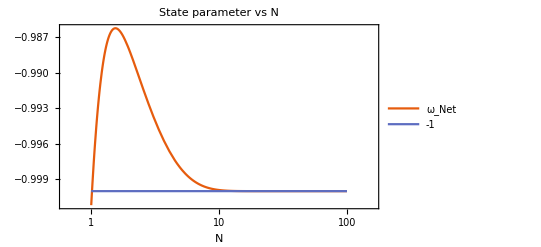

```mathematica
LogLinearPlot[Evaluate[{(2/3)((304128 Subscript[χ, 5]^2 x[t]^6 y[t]^9+1824768 Subscript[χ, 5]^2 x[t]^5 y[t]^10+304128 Subscript[χ, 5]^2 y[t]^15+528 ξ Subscript[χ, 5] y[t]^8 z[t]^4-192 (2 Subscript[θ, 1]-3 ξ) Subscript[χ, 5] y[t]^9 z[t]^4+1056 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) Subscript[χ, 5] y[t]^10 z[t]^4-768 (359 α+8 Subscript[θ, 4]-3 (2 κ+Subscript[χ, 3]+Subscript[χ, 4])) Subscript[χ, 5] y[t]^11 z[t]^4-2 (α (1526 Subscript[θ, 1]+373 ξ)+ξ (48 Subscript[θ, 4]+11 κ+2 (Subscript[χ, 3]+Subscript[χ, 4]))+2 Subscript[θ, 1] (160 Subscript[θ, 4]+3 (17 κ+4 (Subscript[χ, 3]+Subscript[χ, 4])))) y[t]^4 z[t]^8+8 (5243 α^2+256 Subscript[θ, 4]^2+24 κ^2+13 κ Subscript[χ, 3]-4 Subscript[χ, 3]^2+13 κ Subscript[χ, 4]-8 Subscript[χ, 3] Subscript[χ, 4]-4 Subscript[χ, 4]^2+8 Subscript[θ, 4] (19 κ+8 (Subscript[χ, 3]+Subscript[χ, 4]))+α (2616 Subscript[θ, 4]+755 κ+657 (Subscript[χ, 3]+Subscript[χ, 4]))) y[t]^6 z[t]^8+48 Subscript[χ, 5] x[t]^4 y[t]^4 (95040 Subscript[χ, 5] y[t]^7+11 ξ z[t]^4+12 (-8 Subscript[θ, 1]+ξ) y[t] z[t]^4+22 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) y[t]^2 z[t]^4+24 (307 α+96 Subscript[θ, 4]+35 κ+2 Subscript[χ, 3]+2 Subscript[χ, 4]) y[t]^3 z[t]^4)+192 Subscript[χ, 5] x[t]^3 y[t]^5 (31680 Subscript[χ, 5] y[t]^7+11 ξ z[t]^4+4 (-20 Subscript[θ, 1]+3 ξ) y[t] z[t]^4+22 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) y[t]^2 z[t]^4+8 (449 α+200 Subscript[θ, 4]+6 (13 κ+Subscript[χ, 3]+Subscript[χ, 4])) y[t]^3 z[t]^4)+576 Subscript[χ, 5] y[t]^7 z[t]^4 (3+2 (g^2 ξ-6 (Subscript[χ, 1]+Subscript[χ, 2])) z[t]^4+Ωr[t])+y[t]^2 z[t]^8 (30 α+48 Subscript[θ, 1]^2+6 κ+10 Subscript[θ, 1] ξ+ξ^2-24 Subscript[χ, 3]-24 Subscript[χ, 4]+4 (-g^2 ξ (203 α+64 Subscript[θ, 4]+23 κ+4 Subscript[χ, 3]+4 Subscript[χ, 4])+2 (64 Subscript[θ, 4] (3 Subscript[χ, 1]+Subscript[χ, 2])+α (609 Subscript[χ, 1]+193 Subscript[χ, 2])+3 (κ (23 Subscript[χ, 1]+7 Subscript[χ, 2])+4 (Subscript[χ, 1]+Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4])))) z[t]^4+10 α Ωr[t]+2 κ Ωr[t]-8 Subscript[χ, 3] Ωr[t]-8 Subscript[χ, 4] Ωr[t])+z[t]^8 (2 (g^2 ξ (16 Subscript[θ, 1]+ξ)-2 (3 ξ (Subscript[χ, 1]+Subscript[χ, 2])+16 Subscript[θ, 1] (3 Subscript[χ, 1]+Subscript[χ, 2]))) z[t]^4+ξ (3+Ωr[t]))+2 x[t] y[t] (912384 Subscript[χ, 5]^2 y[t]^13+1056 ξ Subscript[χ, 5] y[t]^6 z[t]^4-1152 (3 Subscript[θ, 1]-ξ) Subscript[χ, 5] y[t]^7 z[t]^4+2112 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) Subscript[χ, 5] y[t]^8 z[t]^4-1152 (247 α-32 Subscript[θ, 4]-21 κ-4 Subscript[χ, 3]-4 Subscript[χ, 4]) Subscript[χ, 5] y[t]^9 z[t]^4+ξ^2 z[t]^8-4 (36 α ξ-8 Subscript[θ, 4] ξ-5 κ ξ+8 Subscript[θ, 1] Subscript[χ, 3]+ξ Subscript[χ, 3]+8 Subscript[θ, 1] Subscript[χ, 4]+ξ Subscript[χ, 4]) y[t]^2 z[t]^8-4 (385 α^2-16 Subscript[θ, 4] κ-9 κ^2+10 κ Subscript[χ, 3]+8 Subscript[χ, 3]^2+10 κ Subscript[χ, 4]+16 Subscript[χ, 3] Subscript[χ, 4]+8 Subscript[χ, 4]^2-2 α (40 Subscript[θ, 4]-16 κ+263 (Subscript[χ, 3]+Subscript[χ, 4]))) y[t]^4 z[t]^8+576 Subscript[χ, 5] y[t]^5 z[t]^4 (3+2 (g^2 ξ-6 (Subscript[χ, 1]+Subscript[χ, 2])) z[t]^4+Ωr[t]))+x[t]^2 (4561920 Subscript[χ, 5]^2 y[t]^13+3168 ξ Subscript[χ, 5] y[t]^6 z[t]^4-3456 (5 Subscript[θ, 1]-ξ) Subscript[χ, 5] y[t]^7 z[t]^4+6336 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) Subscript[χ, 5] y[t]^8 z[t]^4+1152 (37 α+240 Subscript[θ, 4]+107 κ+12 Subscript[χ, 3]+12 Subscript[χ, 4]) Subscript[χ, 5] y[t]^9 z[t]^4+ξ (-8 Subscript[θ, 1]+ξ) z[t]^8+4 (156 α ξ+48 Subscript[θ, 4] ξ+18 κ ξ-8 Subscript[θ, 1] Subscript[χ, 3]-ξ Subscript[χ, 3]-8 Subscript[θ, 1] Subscript[χ, 4]-ξ Subscript[χ, 4]) y[t]^2 z[t]^8+4 (1015 α^2+23 κ^2-66 κ Subscript[χ, 3]-8 Subscript[χ, 3]^2-66 κ Subscript[χ, 4]-16 Subscript[χ, 3] Subscript[χ, 4]-8 Subscript[χ, 4]^2+64 Subscript[θ, 4] (κ-3 (Subscript[χ, 3]+Subscript[χ, 4]))+α (320 Subscript[θ, 4]+6 (53 κ-99 (Subscript[χ, 3]+Subscript[χ, 4])))) y[t]^4 z[t]^8+576 Subscript[χ, 5] y[t]^5 z[t]^4 (3+2 (g^2 ξ-6 (Subscript[χ, 1]+Subscript[χ, 2])) z[t]^4+Ωr[t])))/(2 z[t]^4 (576 Subscript[χ, 5] y[t]^7+1152 Subscript[θ, 1] Subscript[χ, 5] y[t]^9-1152 (83 α+16 Subscript[θ, 4]+5 κ) Subscript[χ, 5] y[t]^11-576 Subscript[χ, 5] x[t]^2 y[t]^5 (-1-2 Subscript[θ, 1] y[t]^2+2 (83 α+16 Subscript[θ, 4]+5 κ) y[t]^4)-1152 Subscript[χ, 5] x[t] y[t]^6 (-1-2 Subscript[θ, 1] y[t]^2+2 (83 α+16 Subscript[θ, 4]+5 κ) y[t]^4)+ξ z[t]^4+2 (5 α+8 Subscript[θ, 1]^2+κ+Subscript[θ, 1] ξ-4 Subscript[χ, 3]-4 Subscript[χ, 4]) y[t]^2 z[t]^4-2 (406 α Subscript[θ, 1]+128 Subscript[θ, 1] Subscript[θ, 4]+46 Subscript[θ, 1] κ+83 α ξ+16 Subscript[θ, 4] ξ+5 κ ξ+8 Subscript[θ, 1] Subscript[χ, 3]+8 Subscript[θ, 1] Subscript[χ, 4]) y[t]^4 z[t]^4+4 (2289 α^2+256 Subscript[θ, 4]^2+16 Subscript[θ, 4] (11 κ+4 (Subscript[χ, 3]+Subscript[χ, 4]))+κ (31 κ+20 (Subscript[χ, 3]+Subscript[χ, 4]))+4 α (396 Subscript[θ, 4]+129 κ+83 (Subscript[χ, 3]+Subscript[χ, 4]))) y[t]^6 z[t]^4)))-1,-1}/.sol1],{t,1,tfinal},PlotTheme->"Scientific",PlotRange->All,PlotLabel->Style["State parameter  vs  N",FontSize->12,Bold,FontFamily->"Arial Black"],PlotLegends->Placed[LineLegend[{"ω_Net","-1"},LabelStyle->12,LegendFunction->(Framed[#,FrameStyle->Directive[Thickness[.05]],RoundingRadius->4]&)],{1-(0.05)/2-0.12,0.8}],FrameLabel->{Style["N",Bold,FontSize->12,FontFamily->"Beirut"]},FrameStyle-> Bold]

(* (2/3)ϵ-1 = Subscript[ω, Neto] , de la definición de ϵ, Friedmann y continuidad. Es un caso particular de 
(2/3)ϵ = (Subscript[ρ, Neto]+Subscript[P, Neto])/Subscript[ρ, Neto] [ válido para fluídos perfectos en FLRW plano ] -> De aquí tmbn sale la condición de Gauge-Flation. *)
```

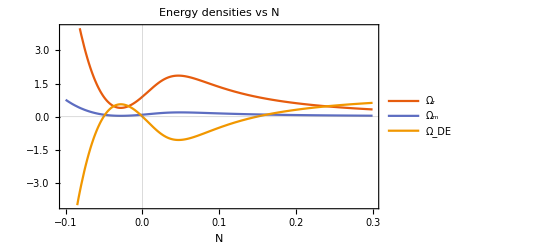

```mathematica
Plot[Evaluate[{Ωr[t],Ωm[t],1-(Ωr[t]+Ωm[t])(*,0.3107,0.0046*)}/.sol1],{t,-0.1,0.3},PlotTheme->"Scientific",PlotRange->{-4,4},PlotLabel->Style["Energy densities  vs  N",FontSize->12,Bold,FontFamily->"Arial Black"],PlotLegends->Placed[LineLegend[{"Ω_r","Ω_m","Ω_DE","Ω_m=0.3107","Ω_r=0.0046"},LabelStyle->7,LegendFunction->(Framed[#,FrameStyle->Directive[Thickness[.05]],RoundingRadius->4]&)],{1-0.11,0.82}],FrameLabel->{Style["N",Bold,FontSize->12,FontFamily->"Beirut"]},FrameStyle-> Bold]
```

## 4. Ecuaciones de estado ( programado para ejecutarse justo después de “Inicialización” )

```mathematica
Clear@@DeleteCases[Names@"`*","ΩGal"|"Ωym"|"PGal"|"Pym"|"ϵ"];
```

```mathematica
β=(203+64 Subscript[Q, 4]+23 Subscript[Q, κ])/(77-16 Subscript[Q, 4]-9 Subscript[Q, κ]);
```

```mathematica
γ=-((-1)^(1/4) √(203+64 Subscript[Q, 4]+23 Subscript[Q, κ]) (2099013+32768 Subscript[Q, 4]^3+548709 Subscript[Q, κ]+45455 Subscript[Q, κ]^2+1023 Subscript[Q, κ]^3+256 Subscript[Q, 4]^2 (1709+121 Subscript[Q, κ])+16 Subscript[Q, 4] (109095+17482 Subscript[Q, κ]+611 Subscript[Q, κ]^2))^(1/4) α^(1/4))/((-(-77+16 Subscript[Q, 4]+9 Subscript[Q, κ])^4 (g^2 ξ-6 Subscript[χ, 1]))^(1/4));
```

```mathematica
κ=Subscript[Q, κ]*α;
Subscript[θ, 4]=Subscript[Q, 4]*α;
Subscript[χ, 1]=Subscript[Q, 1]*α;
Subscript[χ, 2]=0;
Subscript[χ, 3]=0;
Subscript[χ, 4]=0;
Subscript[χ, 5]=0;
Subscript[θ, 1]=0;
```

```mathematica
Z=γ*X;
Y=β*X;
```

```mathematica
Limit[ΩGal/Ωym,X-> Infinity]
```

-1

```mathematica
Limit[PGal/Pym,X-> Infinity]
```

-1

```mathematica
wL4=Limit[PGal/ΩGal,X-> Infinity]
```

1/3

```mathematica
wNeto=Limit[(2/3)ϵ-1 ,X-> Infinity]
```

-1

## Caracterización de puntos críticos / Viabilidad de inflación ( esto solo se hizo para L41 + L42 con κ = 81α )

### 1er punto crítico: [ OK ] - ϵ = 0.778761 - ( Punto de silla con Bifurcación en λ_3 ) .

```mathematica
Clear[X,Y,Z,α,g]
g<0
α<0
X=0
Y=ToRadicals[Root[1-#1^2+1656 α #1^4-652 α #1^6+654608 α^2 #1^8&,2]]
Z=ToRadicals[Root[-1+Y^2-1004 Y^4 α+2 g^2 #1^4&,4]]
eps=FullSimplify[ϵ]
Plot[eps,{α,-10,0},PlotRange->All,Frame->True,FrameLabel->{α,"ϵ"}]
Solve[eps==1, α]
MinValue[ϵ,α] //N
```

g<0

α<0

0

-(√(1/α-(√(1-4016 α))/α))/(2 √502)

0

ϵ

-Graphics-

{}

ϵ

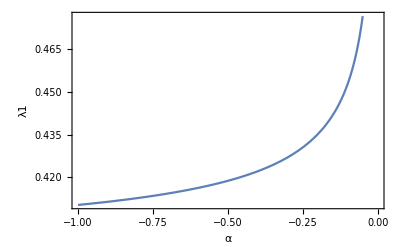

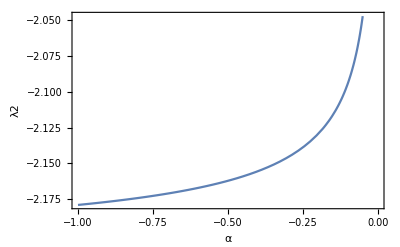

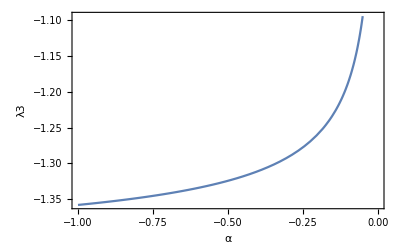

True

```mathematica
Clear[X,Y,Z,α,g];
M8=D[{Xp,Yp,Zp},{{X,Y,Z}}]/.{X-> 0,Y->-(√(1/α-(√(1-4016 α))/α))/(2 √502),Z-> 0};
{ev11,ev12,ev13}=Eigenvalues[M8];
Plot[Re[ev11],{α,-1,0},Frame->True,FrameLabel->{α,"λ1"}]
Plot[Re[ev12],{α,-1,0},Frame->True,FrameLabel->{α,"λ2"}]
Plot[Re[ev13],{α,-1,0},Frame->True,FrameLabel->{α,"λ3"}]

DiagonalizableMatrixQ[M8]
```

```mathematica
MinValue[ev11,α<0,α]
MaxValue[ev12,α<0,α] 
MaxValue[ev13,α<0,α] (* Presenta Bifurcación *)
```

44/113

-1

1

### 2.ba punto crítico: [ NO ] porque Y es imaginario, ϵ = 0.757151 .

g<0

α<0

0

(√(1/α+(√(1-4016 α))/α))/(2 √502)

0

(2 (94+69 √(1-4016 α)+79552 α))/(25+204304 α)

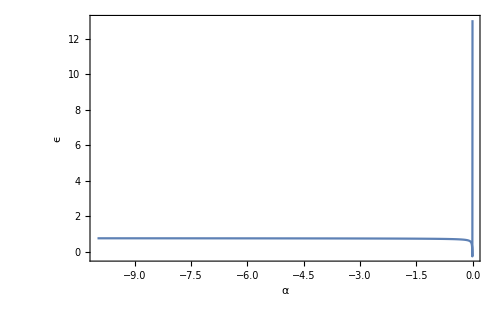

0.757151

```mathematica
Clear[X,Y,Z,α,g]
g<0
α<0
X=0
Y=ToRadicals[Root[1-#1^2+1656 α #1^4-652 α #1^6+654608 α^2 #1^8&,3]]
Z=ToRadicals[Root[-1+Y^2-1004 Y^4 α+2 g^2 #1^4&,4]]
eps=FullSimplify[ϵ]
Plot[eps,{α,-10,0},PlotRange->All,Frame->True,FrameLabel->{α,"ϵ"},ImageSize->500]
α=-4; eps//N
```

### 3.ba punto crítico: Inviable porque ϵ = 2 - ( Punto de silla ) .

```mathematica
Clear[X,Y,Z,α,g]
g<0
α=0
X=0
Y=-1
Z=0
eps=FullSimplify[ϵ]
```

g<0

0

0

-1

0

2

```mathematica
Clear[X,Y,Z,α,g];
α=0;
M8=D[{Xp,Yp,Zp},{{X,Y,Z}}]/.{X-> 0,Y->-1,Z-> 0};
{ev11,ev12,ev13}=Eigenvalues[M8]
DiagonalizableMatrixQ[M8]
```

{-1,1,1}

True

### 4.ba punto crítico: Inviable porque ϵ = 2 - ( Punto de silla ) .

```mathematica
Clear[X,Y,Z,α,g]
g<0
α=0
X=0
Y=1
Z=0
eps=FullSimplify[ϵ]
```

g<0

0

0

1

0

2

```mathematica
Clear[X,Y,Z,α,g];
α=0;
M8=D[{Xp,Yp,Zp},{{X,Y,Z}}]/.{X-> 0,Y->1,Z-> 0};
{ev11,ev12,ev13}=Eigenvalues[M8]
DiagonalizableMatrixQ[M8]
```

{-1,1,1}

True

### 5.ba punto crítico: Inviable porque ϵ > 2 ∀ α - ( Punto de silla ) .

g<0

0<α<1/4016

0

(√(1/α-(√(1-4016 α))/α))/(2 √502)

0

(2 (94-69 √(1-4016 α)+79552 α))/(25+204304 α)

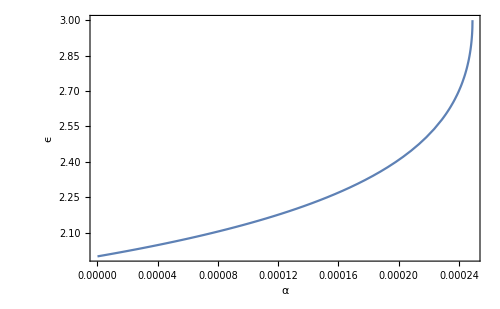

```mathematica
Clear[X,Y,Z,α,g]
g<0
0<α<1/4016
X=0
Y=ToRadicals[Root[1-#1^2+1656 α #1^4-652 α #1^6+654608 α^2 #1^8&,1]]
Z=ToRadicals[Root[-1+Y^2-1004 Y^4 α+2 g^2 #1^4&,4]]
eps=FullSimplify[ϵ]
Plot[eps,{α,0,1/4016},PlotRange->All,Frame->True,FrameLabel->{α,"ϵ"},ImageSize->500]
```

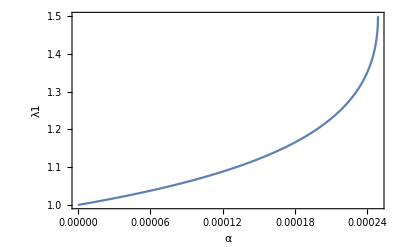

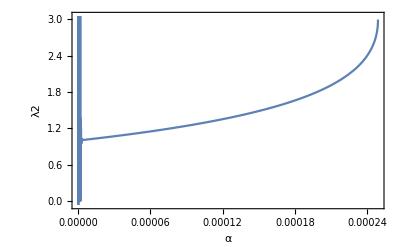

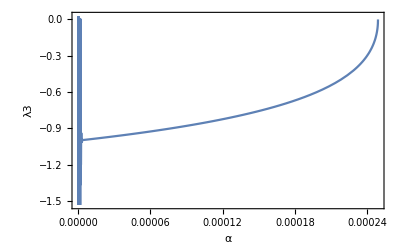

True

```mathematica
Clear[X,Y,Z,α,g];
M8=D[{Xp,Yp,Zp},{{X,Y,Z}}]/.{X-> 0,Y->(√(1/α-(√(1-4016 α))/α))/(2 √502),Z-> 0};
{ev11,ev12,ev13}=Eigenvalues[M8];
Plot[Re[ev11],{α,0,1/4016},Frame->True,FrameLabel->{α,"λ1"}]
Plot[Re[ev12],{α,0,1/4016},Frame->True,FrameLabel->{α,"λ2"}]
Plot[Re[ev13],{α,0,1/4016},Frame->True,FrameLabel->{α,"λ3"}]

DiagonalizableMatrixQ[M8]
```

### 6.ba punto crítico: Inviable porque ϵ > 2 ∀ α - ( Punto de silla ) .

```mathematica
Clear[X,Y,Z,α,g]
g<0
0<α<1/4016
X=0
Y=ToRadicals[Root[1-#1^2+1656 α #1^4-652 α #1^6+654608 α^2 #1^8&,2]]
Z=ToRadicals[Root[-1+Y^2-1004 Y^4 α+2 g^2 #1^4&,4]]
eps=FullSimplify[ϵ]
Plot[eps,{α,0,1/4016},PlotRange->All,Frame->True,FrameLabel->{α,"ϵ"},ImageSize->500]
```

g<0

0<α<1/4016

0

-(√(1/α-(√(1-4016 α))/α))/(2 √502)

0

(2 (94-69 √(1-4016 α)+79552 α))/(25+204304 α)

-Graphics-

```mathematica
Clear[X,Y,Z,α,g];
M8=D[{Xp,Yp,Zp},{{X,Y,Z}}]/.{X-> 0,Y->-(√(1/α-(√(1-4016 α))/α))/(2 √502),Z-> 0};
{ev11,ev12,ev13}=Eigenvalues[M8];
Plot[Re[ev11],{α,0,1/4016},Frame->True,FrameLabel->{α,"λ1"}]
Plot[Re[ev12],{α,0,1/4016},Frame->True,FrameLabel->{α,"λ2"}]
Plot[Re[ev13],{α,0,1/4016},Frame->True,FrameLabel->{α,"λ3"}]

DiagonalizableMatrixQ[M8]
```

-Graphics-

-Graphics-

-Graphics-

True

### 7.ba punto crítico: Inviable porque ϵ > 2 ∀ α - ( Repulsor ) .

g<0

0<α<1/4016

0

(√(1/α+(√(1-4016 α))/α))/(2 √502)

0

(2 (94+69 √(1-4016 α)+79552 α))/(25+204304 α)

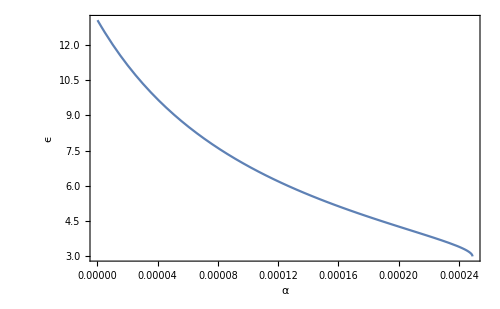

```mathematica
Clear[X,Y,Z,α,g]
g<0
0<α<1/4016
X=0
Y=ToRadicals[Root[1-#1^2+1656 α #1^4-652 α #1^6+654608 α^2 #1^8&,3]]
Z=ToRadicals[Root[-1+Y^2-1004 Y^4 α+2 g^2 #1^4&,4]]
eps=FullSimplify[ϵ]
Plot[eps,{α,0,1/4016},PlotRange->All,Frame->True,FrameLabel->{α,"ϵ"},ImageSize->500]
```

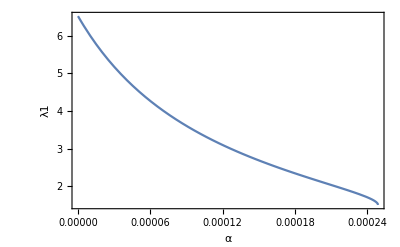

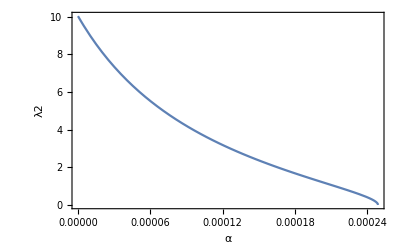

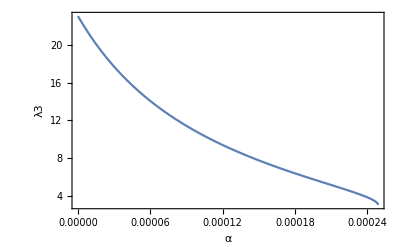

True

```mathematica
Clear[X,Y,Z,α,g];
M8=D[{Xp,Yp,Zp},{{X,Y,Z}}]/.{X-> 0,Y->(√(1/α+(√(1-4016 α))/α))/(2 √502),Z-> 0};
{ev11,ev12,ev13}=Eigenvalues[M8];
Plot[Re[ev11],{α,0,1/4016},Frame->True,FrameLabel->{α,"λ1"}]
Plot[Re[ev12],{α,0,1/4016},Frame->True,FrameLabel->{α,"λ2"}]
Plot[Re[ev13],{α,0,1/4016},Frame->True,FrameLabel->{α,"λ3"}]

DiagonalizableMatrixQ[M8]
```

### 8.ba punto crítico: Inviable porque ϵ > 2 ∀ α - ( Repulsor ) .

```mathematica
Clear[X,Y,Z,α,g]
g<0
0<α<1/4016
X=0
Y=ToRadicals[Root[1-#1^2+1656 α #1^4-652 α #1^6+654608 α^2 #1^8&,4]]
Z=ToRadicals[Root[-1+Y^2-1004 Y^4 α+2 g^2 #1^4&,4]]
eps=FullSimplify[ϵ]
Plot[eps,{α,0,1/4016},PlotRange->All,Frame->True,FrameLabel->{α,"ϵ"},ImageSize->500]
```

g<0

0<α<1/4016

0

-(√(1/α+(√(1-4016 α))/α))/(2 √502)

0

(2 (94+69 √(1-4016 α)+79552 α))/(25+204304 α)

-Graphics-

```mathematica
Clear[X,Y,Z,α,g];
M8=D[{Xp,Yp,Zp},{{X,Y,Z}}]/.{X-> 0,Y->-(√(1/α+(√(1-4016 α))/α))/(2 √502),Z-> 0};
{ev11,ev12,ev13}=Eigenvalues[M8];
Plot[Re[ev11],{α,0,1/4016},Frame->True,FrameLabel->{α,"λ1"}]
Plot[Re[ev12],{α,0,1/4016},Frame->True,FrameLabel->{α,"λ2"}]
Plot[Re[ev13],{α,0,1/4016},Frame->True,FrameLabel->{α,"λ3"}]

DiagonalizableMatrixQ[M8]
```

-Graphics-

-Graphics-

-Graphics-

True

### 9.ba punto crítico: Inviable porque ϵ = 3 - ( Repulsor ??? ) - Un autovalor da cero .

```mathematica
Clear[X,Y,Z,α,g]
g<0
α=1/4016
X=0
Y=-Sqrt[2]
Z=ToRadicals[Root[-4+4 Y^2-Y^4+8 g^2 #1^4&,4]]
eps=FullSimplify[ϵ]
```

g<0

1/4016

0

-√2

0

3

```mathematica
Clear[X,Y,Z,α,g];
α=1/4016;
M8=D[{Xp,Yp,Zp},{{X,Y,Z}}]/.{X-> 0,Y->-√2,Z-> 0};
{ev11,ev12,ev13}=Eigenvalues[M8]
DiagonalizableMatrixQ[M8]
```

{3,3/2,0}

True

### 10.ba punto crítico: Inviable porque ϵ = 3 - ( Repulsor ??? ) - Un autovalor da cero .

```mathematica
Clear[X,Y,Z,α,g]
g<0
α=1/4016
X=0
Y=Sqrt[2]
Z=ToRadicals[Root[-4+4 Y^2-Y^4+8 g^2 #1^4&,4]]
eps=FullSimplify[ϵ]
```

g<0

1/4016

0

√2

0

3

```mathematica
Clear[X,Y,Z,α,g];
α=1/4016;
M8=D[{Xp,Yp,Zp},{{X,Y,Z}}]/.{X-> 0,Y->√2,Z-> 0};
{ev11,ev12,ev13}=Eigenvalues[M8]
DiagonalizableMatrixQ[M8]
```

{3,3/2,0}

True

### 11.ba punto crítico: [ OK pero ϵ = 0.778761 ] - ( Punto de silla con Bifurcación en λ_3 ) .

0

α<0

0

(√(1/α-(√(1-4016 α))/α))/(2 √502)

0

(2 (94-69 √(1-4016 α)+79552 α))/(25+204304 α)

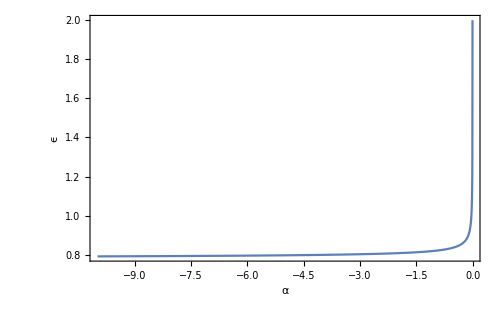

{{α→-301/10000}}

0.778761

```mathematica
Clear[X,Y,Z,α,g]
g=0
α<0
X=0
Y=ToRadicals[Root[1-#1^2+1004 α #1^4&,1]]
Z=0
eps=FullSimplify[ϵ]
Plot[eps,{α,-10,0},PlotRange->All,Frame->True,FrameLabel->{α,"ϵ"},ImageSize->500]
Solve[eps==1, α]
MinValue[ϵ,α]//N
```

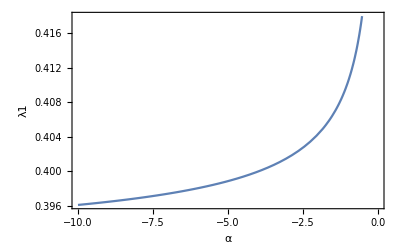

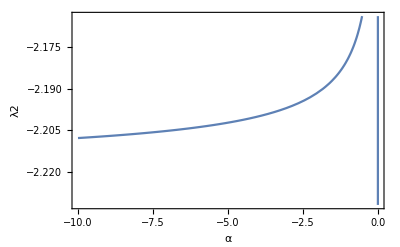

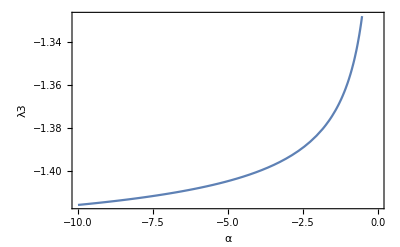

True

```mathematica
Clear[X,Y,Z,α,g];
M8=D[{Xp,Yp,Zp},{{X,Y,Z}}]/.{X-> 0,Y->(√(1/α-(√(1-4016 α))/α))/(2 √502),Z-> 0};
{ev11,ev12,ev13}=Eigenvalues[M8];
Plot[Re[ev11],{α,-10,0},Frame->True,FrameLabel->{α,"λ1"}]
Plot[Re[ev12],{α,-10,0},Frame->True,FrameLabel->{α,"λ2"}]
Plot[Re[ev13],{α,-10,0},Frame->True,FrameLabel->{α,"λ3"}]

DiagonalizableMatrixQ[M8]
```

```mathematica
MinValue[ev11,α<0,α]
MaxValue[ev12,α<0,α]
MaxValue[ev13,α<0,α] (* Presenta Bifurcación *)
```

44/113

-1

1

### 12.ba punto crítico: [ OK pero ϵ = 0.778761 ] - ( Punto de silla con Bifurcación en λ_3 ) .

```mathematica
Clear[X,Y,Z,α,g]
g=0
α<0
X=0
Y=ToRadicals[Root[1-#1^2+1004 α #1^4&,2]]
Z=0
eps=FullSimplify[ϵ]
Plot[eps,{α,-10,0},PlotRange->All,Frame->True,FrameLabel->{α,"ϵ"},ImageSize->500]
Solve[eps==1, α]
MinValue[ϵ,α]//N
```

0

α<0

0

-(√(1/α-(√(1-4016 α))/α))/(2 √502)

0

(2 (94-69 √(1-4016 α)+79552 α))/(25+204304 α)

-Graphics-

{{α→-301/10000}}

0.778761

```mathematica
Clear[X,Y,Z,α,g];
M8=D[{Xp,Yp,Zp},{{X,Y,Z}}]/.{X-> 0,Y->-(√(1/α-(√(1-4016 α))/α))/(2 √502),Z-> 0};
{ev11,ev12,ev13}=Eigenvalues[M8];
Plot[Re[ev11],{α,-10,0},Frame->True,FrameLabel->{α,"λ1"}]
Plot[Re[ev12],{α,-10,0},Frame->True,FrameLabel->{α,"λ2"}]
Plot[Re[ev13],{α,-10,0},Frame->True,FrameLabel->{α,"λ3"}]

DiagonalizableMatrixQ[M8]
```

-Graphics-

-Graphics-

-Graphics-

True

```mathematica
MinValue[ev11,α<0,α]
MaxValue[ev12,α<0,α]
MaxValue[ev13,α<0,α] (* Presenta Bifurcación *)
```

44/113

-1

1

### 13.ba punto crítico: Inviable porque ϵ = 2 - ( Punto de silla ) .

```mathematica
Clear[X,Y,Z,α,g]
g=0
α=0
X=0
Y=-1
Z=0
eps=FullSimplify[ϵ]
```

0

0

0

-1

0

2

```mathematica
Clear[X,Y,Z,α,g];
α=0;
M8=D[{Xp,Yp,Zp},{{X,Y,Z}}]/.{X-> 0,Y->-1,Z-> 0};
{ev11,ev12,ev13}=Eigenvalues[M8]
DiagonalizableMatrixQ[M8]
```

{-1,1,1}

True

### 14.ba punto crítico: Inviable porque ϵ = 2 - ( Punto de silla ) .

```mathematica
Clear[X,Y,Z,α,g]
g=0
α=0
X=0
Y=1
Z=0
eps=FullSimplify[ϵ]
```

0

0

0

1

0

2

```mathematica
Clear[X,Y,Z,α,g];
α=0;
M8=D[{Xp,Yp,Zp},{{X,Y,Z}}]/.{X-> 0,Y->1,Z-> 0};
{ev11,ev12,ev13}=Eigenvalues[M8]
DiagonalizableMatrixQ[M8]
```

{-1,1,1}

True

### 15.ba punto crítico: Inviable porque ϵ > 2 ∀ α - ( Punto de silla ) .

```mathematica
Clear[X,Y,Z,α,g]
g=0
0<α<1/4016
X=0
Y=ToRadicals[Root[1-#1^2+1004 α #1^4&,1]]
Z=0
eps=FullSimplify[ϵ]
Plot[eps,{α,0,1/4016},PlotRange->All,Frame->True,FrameLabel->{α,"ϵ"},ImageSize->500]
Solve[eps==1, α]
```

0

0<α<1/4016

0

(√(1/α-(√(1-4016 α))/α))/(2 √502)

0

(2 (94-69 √(1-4016 α)+79552 α))/(25+204304 α)

-Graphics-

{{α→-301/10000}}

```mathematica
Clear[X,Y,Z,α,g];
M8=D[{Xp,Yp,Zp},{{X,Y,Z}}]/.{X-> 0,Y->(√(1/α-(√(1-4016 α))/α))/(2 √502),Z-> 0};
{ev11,ev12,ev13}=Eigenvalues[M8];
Plot[Re[ev11],{α,0,1/4016},Frame->True,FrameLabel->{α,"λ1"}]
Plot[Re[ev12],{α,0,1/4016},Frame->True,FrameLabel->{α,"λ2"}]
Plot[Re[ev13],{α,0,1/4016},Frame->True,FrameLabel->{α,"λ3"}]

DiagonalizableMatrixQ[M8]
```

-Graphics-

-Graphics-

-Graphics-

True

### 16.ba punto crítico: Inviable porque ϵ > 2 ∀ α - ( Punto de silla ) .

```mathematica
Clear[X,Y,Z,α,g]
g=0
0<α<1/4016
X=0
Y=ToRadicals[Root[1-#1^2+1004 α #1^4&,2]]
Z=0
eps=FullSimplify[ϵ]
Plot[eps,{α,0,1/4016},PlotRange->All,Frame->True,FrameLabel->{α,"ϵ"},ImageSize->500]
Solve[eps==1, α]
```

0

0<α<1/4016

0

-(√(1/α-(√(1-4016 α))/α))/(2 √502)

0

(2 (94-69 √(1-4016 α)+79552 α))/(25+204304 α)

-Graphics-

{{α→-301/10000}}

```mathematica
Clear[X,Y,Z,α,g];
M8=D[{Xp,Yp,Zp},{{X,Y,Z}}]/.{X-> 0,Y->-(√(1/α-(√(1-4016 α))/α))/(2 √502),Z-> 0};
{ev11,ev12,ev13}=Eigenvalues[M8];
Plot[Re[ev11],{α,0,1/4016},Frame->True,FrameLabel->{α,"λ1"}]
Plot[Re[ev12],{α,0,1/4016},Frame->True,FrameLabel->{α,"λ2"}]
Plot[Re[ev13],{α,0,1/4016},Frame->True,FrameLabel->{α,"λ3"}]

DiagonalizableMatrixQ[M8]
```

-Graphics-

-Graphics-

-Graphics-

True

### 17.ba punto crítico: Inviable porque ϵ > 2 ∀ α - ( Punto de silla ) .

```mathematica
Clear[X,Y,Z,α,g]
g=0
0<α<1/4016
X=0
Y=ToRadicals[Root[1-#1^2+1004 α #1^4&,3]]
Z=0
eps=FullSimplify[ϵ]
Plot[eps,{α,0,1/4016},PlotRange->All,Frame->True,FrameLabel->{α,"ϵ"},ImageSize->500]
```

0

0<α<1/4016

0

(√(1/α+(√(1-4016 α))/α))/(2 √502)

0

(2 (94+69 √(1-4016 α)+79552 α))/(25+204304 α)

-Graphics-

```mathematica
Clear[X,Y,Z,α,g];
M8=D[{Xp,Yp,Zp},{{X,Y,Z}}]/.{X-> 0,Y->(√(1/α-(√(1-4016 α))/α))/(2 √502),Z-> 0};
{ev11,ev12,ev13}=Eigenvalues[M8];
Plot[Re[ev11],{α,0,1/4016},Frame->True,FrameLabel->{α,"λ1"}]
Plot[Re[ev12],{α,0,1/4016},Frame->True,FrameLabel->{α,"λ2"}]
Plot[Re[ev13],{α,0,1/4016},Frame->True,FrameLabel->{α,"λ3"}]

DiagonalizableMatrixQ[M8]
```

-Graphics-

-Graphics-

-Graphics-

True

### 18.ba punto crítico: Inviable porque ϵ > 2 ∀ α - ( Punto de silla ) .

```mathematica
Clear[X,Y,Z,α,g]
g=0
0<α<1/4016
X=0
Y=ToRadicals[Root[1-#1^2+1004 α #1^4&,4]]
Z=0
eps=FullSimplify[ϵ]
Plot[eps,{α,0,1/4016},PlotRange->All,Frame->True,FrameLabel->{α,"ϵ"},ImageSize->500]
```

0

0<α<1/4016

0

-(√(1/α+(√(1-4016 α))/α))/(2 √502)

0

(2 (94+69 √(1-4016 α)+79552 α))/(25+204304 α)

-Graphics-

```mathematica
Clear[X,Y,Z,α,g];
M8=D[{Xp,Yp,Zp},{{X,Y,Z}}]/.{X-> 0,Y->-(√(1/α-(√(1-4016 α))/α))/(2 √502),Z-> 0};
{ev11,ev12,ev13}=Eigenvalues[M8];
Plot[Re[ev11],{α,0,1/4016},Frame->True,FrameLabel->{α,"λ1"}]
Plot[Re[ev12],{α,0,1/4016},Frame->True,FrameLabel->{α,"λ2"}]
Plot[Re[ev13],{α,0,1/4016},Frame->True,FrameLabel->{α,"λ3"}]

DiagonalizableMatrixQ[M8]
```

-Graphics-

-Graphics-

-Graphics-

True

### 19.ba punto crítico: Inviable porque ϵ = 3 - ( Repulsor ??? ) - Un autovalor da cero .

```mathematica
Clear[X,Y,Z,α,g]
g=0
α=1/4016
X=0
Y=-Sqrt[2]
Z=0
eps=FullSimplify[ϵ]
```

0

1/4016

0

-√2

0

3

```mathematica
Clear[X,Y,Z,α,g];
α=1/4016;
M8=D[{Xp,Yp,Zp},{{X,Y,Z}}]/.{X-> 0,Y->-√2,Z-> 0};
{ev11,ev12,ev13}=Eigenvalues[M8]
DiagonalizableMatrixQ[M8]
```

{3,3/2,0}

True

### 20.ba punto crítico: Inviable porque ϵ = 3 - ( Repulsor ??? ) - Un autovalor da cero .

```mathematica
Clear[X,Y,Z,α,g]
g=0
α=1/4016
X=0
Y=Sqrt[2]
Z=0
eps=FullSimplify[ϵ]
```

0

1/4016

0

√2

0

3

```mathematica
Clear[X,Y,Z,α,g];
α=1/4016;
M8=D[{Xp,Yp,Zp},{{X,Y,Z}}]/.{X-> 0,Y->√2,Z-> 0};
{ev11,ev12,ev13}=Eigenvalues[M8]
DiagonalizableMatrixQ[M8]
```

{3,3/2,0}

True

### 21.ba punto crítico: [ OK pero ϵ = 0.778761 ] - ( Punto de silla con Bifurcación en λ_3 ) .

```mathematica
Clear[X,Y,Z,α,g]
g>0
α<0
X=0
Y=ToRadicals[Root[1-#1^2+1656 α #1^4-652 α #1^6+654608 α^2 #1^8&,2]]
Z=ToRadicals[Root[-1+Y^2-1004 Y^4 α+2 g^2 #1^4&,4]]
eps=FullSimplify[ϵ]
Plot[eps,{α,-10,0},PlotRange->All,Frame->True,FrameLabel->{α,"ϵ"},ImageSize->500]
Solve[eps==1, α]
MinValue[ϵ,α]//N
```

g>0

α<0

0

-(√(1/α-(√(1-4016 α))/α))/(2 √502)

0

(2 (94-69 √(1-4016 α)+79552 α))/(25+204304 α)

-Graphics-

{{α→-301/10000}}

0.778761

```mathematica
Clear[X,Y,Z,α,g];
M8=D[{Xp,Yp,Zp},{{X,Y,Z}}]/.{X-> 0,Y->-(√(1/α-(√(1-4016 α))/α))/(2 √502),Z-> 0};
{ev11,ev12,ev13}=Eigenvalues[M8];
Plot[Re[ev11],{α,-1,0},Frame->True,FrameLabel->{α,"λ1"}]
Plot[Re[ev12],{α,-1,0},Frame->True,FrameLabel->{α,"λ2"}]
Plot[Re[ev13],{α,-1,0},Frame->True,FrameLabel->{α,"λ3"}]

DiagonalizableMatrixQ[M8]
```

-Graphics-

-Graphics-

-Graphics-

True

```mathematica
MinValue[ev11,α<0,α]
MaxValue[ev12,α<0,α] 
MaxValue[ev13,α<0,α] (* Presenta Bifurcación *)
```

44/113

-1

1

### 22.ba punto crítico: [ NO ] porque Y es imaginario, ϵ = 0.757151 .

```mathematica
Clear[X,Y,Z,α,g]
g>0
α<0
X=0
Y=ToRadicals[Root[1-#1^2+1656 α #1^4-652 α #1^6+654608 α^2 #1^8&,3]]
Z=ToRadicals[Root[-1+Y^2-1004 Y^4 α+2 g^2 #1^4&,4]]
eps=FullSimplify[ϵ]
Plot[eps,{α,-10,0},PlotRange->All,Frame->True,FrameLabel->{α,"ϵ"},ImageSize->500]
α=-4; ϵ//N
```

g>0

α<0

0

(√(1/α+(√(1-4016 α))/α))/(2 √502)

0

(2 (94+69 √(1-4016 α)+79552 α))/(25+204304 α)

-Graphics-

0.757151

### 23.ba punto crítico: Inviable porque ϵ = 2 - ( Punto de silla ) .

```mathematica
Clear[X,Y,Z,α,g]
g>0
α=0
X=0
Y=-1
Z=0
eps=FullSimplify[ϵ]
```

g>0

0

0

-1

0

2

```mathematica
Clear[X,Y,Z,α,g];
α=0;
M8=D[{Xp,Yp,Zp},{{X,Y,Z}}]/.{X-> 0,Y->-1,Z-> 0};
{ev11,ev12,ev13}=Eigenvalues[M8]
DiagonalizableMatrixQ[M8]
```

{-1,1,1}

True

### 24.ba punto crítico: Inviable porque ϵ = 2 - ( Punto de silla ) .

```mathematica
Clear[X,Y,Z,α,g]
g>0
α=0
X=0
Y=1
Z=0
eps=FullSimplify[ϵ]
```

g>0

0

0

1

0

2

```mathematica
Clear[X,Y,Z,α,g];
α=0;
M8=D[{Xp,Yp,Zp},{{X,Y,Z}}]/.{X-> 0,Y->1,Z-> 0};
{ev11,ev12,ev13}=Eigenvalues[M8]
DiagonalizableMatrixQ[M8]
```

{-1,1,1}

True

### 25.ba punto crítico: Inviable porque ϵ > 2 ∀ α - ( Punto de silla ) .

```mathematica
Clear[X,Y,Z,α,g]
g>0
0<α<1/4016
X=0
Y=ToRadicals[Root[1-#1^2+1656 α #1^4-652 α #1^6+654608 α^2 #1^8&,1]]
Z=ToRadicals[Root[-1+Y^2-1004 Y^4 α+2 g^2 #1^4&,4]]
eps=FullSimplify[ϵ]
Plot[eps,{α,0,1/4016},PlotRange->All,Frame->True,FrameLabel->{α,"ϵ"},ImageSize->500]
```

g>0

0<α<1/4016

0

(√(1/α-(√(1-4016 α))/α))/(2 √502)

0

(2 (94-69 √(1-4016 α)+79552 α))/(25+204304 α)

-Graphics-

```mathematica
Clear[X,Y,Z,α,g];
M8=D[{Xp,Yp,Zp},{{X,Y,Z}}]/.{X-> 0,Y->(√(1/α-(√(1-4016 α))/α))/(2 √502),Z-> 0};
{ev11,ev12,ev13}=Eigenvalues[M8];
Plot[Re[ev11],{α,0,1/4016},Frame->True,FrameLabel->{α,"λ1"}]
Plot[Re[ev12],{α,0,1/4016},Frame->True,FrameLabel->{α,"λ2"}]
Plot[Re[ev13],{α,0,1/4016},Frame->True,FrameLabel->{α,"λ3"}]

DiagonalizableMatrixQ[M8]
```

-Graphics-

-Graphics-

-Graphics-

True

### 26.ba punto crítico: Inviable porque ϵ > 2 ∀ α - ( Punto de silla ) .

```mathematica
Clear[X,Y,Z,α,g]
g>0
0<α<1/4016
X=0
Y=ToRadicals[Root[1-#1^2+1656 α #1^4-652 α #1^6+654608 α^2 #1^8&,2]]
Z=ToRadicals[Root[-1+Y^2-1004 Y^4 α+2 g^2 #1^4&,4]]
eps=FullSimplify[ϵ]
Plot[eps,{α,0,1/4016},PlotRange->All,Frame->True,FrameLabel->{α,"ϵ"},ImageSize->500]
```

g>0

0<α<1/4016

0

-(√(1/α-(√(1-4016 α))/α))/(2 √502)

0

(2 (94-69 √(1-4016 α)+79552 α))/(25+204304 α)

-Graphics-

```mathematica
Clear[X,Y,Z,α,g];
M8=D[{Xp,Yp,Zp},{{X,Y,Z}}]/.{X-> 0,Y->-(√(1/α-(√(1-4016 α))/α))/(2 √502),Z-> 0};
{ev11,ev12,ev13}=Eigenvalues[M8];
Plot[Re[ev11],{α,0,1/4016},Frame->True,FrameLabel->{α,"λ1"}]
Plot[Re[ev12],{α,0,1/4016},Frame->True,FrameLabel->{α,"λ2"}]
Plot[Re[ev13],{α,0,1/4016},Frame->True,FrameLabel->{α,"λ3"}]

DiagonalizableMatrixQ[M8]
```

-Graphics-

-Graphics-

-Graphics-

True

### 27.ba punto crítico: Inviable porque ϵ > 2 ∀ α - ( Punto de silla ) .

```mathematica
Clear[X,Y,Z,α,g]
g>0
0<α<1/4016
X=0
Y=ToRadicals[Root[1-#1^2+1656 α #1^4-652 α #1^6+654608 α^2 #1^8&,3]]
Z=ToRadicals[Root[-1+Y^2-1004 Y^4 α+2 g^2 #1^4&,4]]
eps=FullSimplify[ϵ]
Plot[eps,{α,0,1/4016},PlotRange->All,Frame->True,FrameLabel->{α,"ϵ"},ImageSize->500]
```

g>0

0<α<1/4016

0

(√(1/α+(√(1-4016 α))/α))/(2 √502)

0

(2 (94+69 √(1-4016 α)+79552 α))/(25+204304 α)

-Graphics-

```mathematica
Clear[X,Y,Z,α,g];
M8=D[{Xp,Yp,Zp},{{X,Y,Z}}]/.{X-> 0,Y->(√(1/α-(√(1-4016 α))/α))/(2 √502),Z-> 0};
{ev11,ev12,ev13}=Eigenvalues[M8];
Plot[Re[ev11],{α,0,1/4016},Frame->True,FrameLabel->{α,"λ1"}]
Plot[Re[ev12],{α,0,1/4016},Frame->True,FrameLabel->{α,"λ2"}]
Plot[Re[ev13],{α,0,1/4016},Frame->True,FrameLabel->{α,"λ3"}]

DiagonalizableMatrixQ[M8]
```

-Graphics-

-Graphics-

-Graphics-

True

### 28.ba punto crítico: Inviable porque ϵ > 2 ∀ α - ( Punto de silla ) .

```mathematica
Clear[X,Y,Z,α,g]
g>0
0<α<1/4016
X=0
Y=ToRadicals[Root[1-#1^2+1656 α #1^4-652 α #1^6+654608 α^2 #1^8&,4]]
Z=ToRadicals[Root[-1+Y^2-1004 Y^4 α+2 g^2 #1^4&,4]]
eps=FullSimplify[ϵ]
Plot[eps,{α,0,1/4016},PlotRange->All,Frame->True,FrameLabel->{α,"ϵ"},ImageSize->500]
```

g>0

0<α<1/4016

0

-(√(1/α+(√(1-4016 α))/α))/(2 √502)

0

(2 (94+69 √(1-4016 α)+79552 α))/(25+204304 α)

-Graphics-

```mathematica
Clear[X,Y,Z,α,g];
M8=D[{Xp,Yp,Zp},{{X,Y,Z}}]/.{X-> 0,Y->-(√(1/α-(√(1-4016 α))/α))/(2 √502),Z-> 0};
{ev11,ev12,ev13}=Eigenvalues[M8];
Plot[Re[ev11],{α,0,1/4016},Frame->True,FrameLabel->{α,"λ1"}]
Plot[Re[ev12],{α,0,1/4016},Frame->True,FrameLabel->{α,"λ2"}]
Plot[Re[ev13],{α,0,1/4016},Frame->True,FrameLabel->{α,"λ3"}]

DiagonalizableMatrixQ[M8]
```

-Graphics-

-Graphics-

-Graphics-

True

### 29.ba punto crítico: Inviable porque ϵ = 3 - ( Repulsor ??? ) - Un autovalor da cero .

```mathematica
Clear[X,Y,Z,α,g]
g>0
α=1/4016
X=0
Y=-Sqrt[2]
Z=Root[-4+4 Y^2-Y^4+8 g^2 #1^4&,4]
eps=FullSimplify[ϵ]
```

g>0

1/4016

0

-√2

0

3

```mathematica
Clear[X,Y,Z,α,g];
α=1/4016;
M8=D[{Xp,Yp,Zp},{{X,Y,Z}}]/.{X-> 0,Y->-√2,Z-> 0};
{ev11,ev12,ev13}=Eigenvalues[M8]
DiagonalizableMatrixQ[M8]
```

{3,3/2,0}

True

### 30.ba punto crítico: Inviable porque ϵ = 3 - ( Repulsor ??? ) - Un autovalor da cero .

```mathematica
Clear[X,Y,Z,α,g]
g>0
α=1/4016
X=0
Y=Sqrt[2]
Z=Root[-4+4 Y^2-Y^4+8 g^2 #1^4&,4]
eps=FullSimplify[ϵ]
```

g>0

1/4016

0

√2

0

3

```mathematica
Clear[X,Y,Z,α,g];
α=1/4016;
M8=D[{Xp,Yp,Zp},{{X,Y,Z}}]/.{X-> 0,Y->√2,Z-> 0};
{ev11,ev12,ev13}=Eigenvalues[M8]
DiagonalizableMatrixQ[M8]
```

{3,3/2,0}

True

$Aborted

$Aborted

## Complemento: Rangos viables para Y0, Z0, α que generan un X0 real ( * Esto está en versión de prueba * ) - Puede servir para obtener condiciones iniciales que no generen phantom energy en etapas tempranas.

```mathematica
ClearAll["Global`*"];
κ=81α;
Subscript[θ, 4]=Subscript[Q, 4] α;
Reduce[-1+(10 X^2 Y^2-188 X Y^3-32 Y^4) α+(-64 X Y^3-32 Y^4) Subscript[θ, 4]+(2 X^2 Y^2-20 X Y^3-12 Y^4) κ+(X^2+2 X Y+Y^2+2 g^2 Z^4) ξ-12 Z^4 Subscript[χ, 1]==0&&ξ≠ 0&&Y≠ 0&&Z≠ 0,X]/.Subscript[χ, 1]-> (g^2*ξ-η)/6 /.ξ->1//Simplify
```

(1+172 Y^2 α≠0&&(X==-(Y-8 (113+4 Q_4) Y^3 α+√(1-16 (61+2 Q_4) Y^4 α+16 (61869+3960 Q_4+64 Q_4^2) Y^6 α^2-2 Z^4 η-172 Y^2 α (-1+2 Z^4 η)))/(1+172 Y^2 α)||X==(-Y+8 (113+4 Q_4) Y^3 α+√(1-16 (61+2 Q_4) Y^4 α+16 (61869+3960 Q_4+64 Q_4^2) Y^6 α^2-2 Z^4 η-172 Y^2 α (-1+2 Z^4 η)))/(1+172 Y^2 α))&&Y Z≠0)||(α≠0&&(Y==-ⅈ/(2 √43 √α)||Y==ⅈ/(2 √43 √α))&&Q_4==-269/8&&Z≠0&&(g==-(√(1/2-(25 Y^2)/86+g^2 Z^4-Z^4 η))/Z^2||g==(√(1/2-(25 Y^2)/86+g^2 Z^4-Z^4 η))/Z^2))||(α≠0&&(Y==-ⅈ/(2 √43 √α)||Y==ⅈ/(2 √43 √α))&&(269+8 Q_4) Y≠0&&X==(43-294 Y^2-8 Q_4 Y^2-86 Z^4 η)/(538 Y+16 Q_4 Y)&&Z≠0)

```mathematica
Solve[1+172 Y^2 α==0,Y] (* La desigualdad siempre se satisface sobre el campo de los Reales *)
```

{{Y→-ⅈ/(2 √43 √α)},{Y→ⅈ/(2 √43 √α)}}

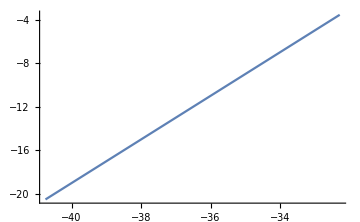
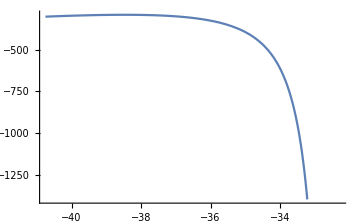
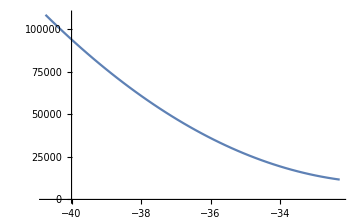
Grid[{-Graphics-,-Graphics-,-Graphics-}]

En lo relativo a Q_4 todos los polinomios involucrados son monótonos, por consiguiente, basta evaluar en los extremos

1+172 Q_Y^2 α^3+(328. Q_Y^4+5.05968×10^-119 Q_z^4) α^5+(108400. Q_Y^6+8.70266×10^-117 Q_Y^2 Q_z^4) α^8

1+172 Q_Y^2 α^3+(57. Q_Y^4+2.57554×10^-90 Q_z^4) α^5+(11653. Q_Y^6+4.42993×10^-88 Q_Y^2 Q_z^4) α^8

```mathematica
Clear[Subscript[Q, 4],Subscript[Q, z],Subscript[Q, Y]];
Qi=-40.75; Qf= -32.28125;Z=Subscript[Q, z]*α;Y=Subscript[Q, Y] α; η=(2 Ho^2 (111054855+11067816 Subscript[Q, 4]+368320 Subscript[Q, 4]^2+4096 Subscript[Q, 4]^3) α)/(mp^2 (1033+32 Subscript[Q, 4])^2);
DiscriminanteDeX=1-16 (61+2 Subscript[Q, 4]) Y^4 α+16 (61869+3960 Subscript[Q, 4]+64 Subscript[Q, 4]^2) Y^6 α^2-2 Z^4 η-172 Y^2 α (-1+2 Z^4 η)//Simplify;

Ho=10^(-42);
mp=2.435*10^(18);

Collect[DiscriminanteDeX,{Y,α}];
Grid[{Plot[61+2 Subscript[Q, 4],{Subscript[Q, 4],Qi,Qf},ImageSize->Medium],Plot[4*(111054855+11067816 Subscript[Q, 4]+368320 Subscript[Q, 4]^2+4096 Subscript[Q, 4]^3)/((1033+32 Subscript[Q, 4])^2),{Subscript[Q, 4],Qi,Qf},ImageSize->Medium],
Plot[16 (61869+3960 Subscript[Q, 4]+64 Subscript[Q, 4]^2),{Subscript[Q, 4],Qi,Qf},ImageSize->Medium]}]

Print["En lo relativo a Q_4 todos los polinomios involucrados son monótonos, por consiguiente, basta evaluar en los extremos"]

Subscript[Q, 4]=Qi; Collect[DiscriminanteDeX,{Y,α}]
Subscript[Q, 4]=Qf-10^(-14); Collect[DiscriminanteDeX,{Y,α}]
```

```mathematica
n=37;
Grid[{RegionPlot3D[1+172 Subscript[Q, Y]^2 α^3+(328. Subscript[Q, Y]^4+5.05968317950491*^-119 Subscript[Q, z]^4) α^5+(108400. Subscript[Q, Y]^6+8.702655068748445*^-117 Subscript[Q, Y]^2 Subscript[Q, z]^4) α^8≥ 0,{Subscript[Q, Y],-10^n,10^n},{Subscript[Q, z],-10^n,10^n},{α,-10^n,10^n},ImageSize->Medium,Mesh->None,PlotStyle->Directive[Opacity[0.5]]],
RegionPlot3D[1+172 Subscript[Q, Y]^2 α^3+(57.00000000000023 Subscript[Q, Y]^4+2.575542677558768*^-90 Subscript[Q, z]^4) α^5+(11653. Subscript[Q, Y]^6+4.4299334054010804*^-88 Subscript[Q, Y]^2 Subscript[Q, z]^4) α^8≥ 0,{Subscript[Q, Y],-10^n,10^n},{Subscript[Q, z],-10^n,10^n},{α,-10^n,10^n},ImageSize->Medium,Mesh->None,PlotStyle->Directive[Opacity[0.5]]]}]
```

Grid[{-Graphics3D-,-Graphics3D-}]

```mathematica
Print[];
For[i=0,i<10,i++,Print["ESTO PARECE SUGERIR QUE EL SISTEMA CON ( ξ=1 ) SE COMPORTA BIEN CON {Q_Y,Q_Z,α} ∈ [-10^n,10^n], ( n≤37 )."]] ;Print[];
```

ESTO PARECE SUGERIR QUE EL SISTEMA CON ( ξ=1 ) SE COMPORTA BIEN CON {Q_Y,Q_Z,α} ∈ [-10^n,10^n], ( n≤37 ).

ESTO PARECE SUGERIR QUE EL SISTEMA CON ( ξ=1 ) SE COMPORTA BIEN CON {Q_Y,Q_Z,α} ∈ [-10^n,10^n], ( n≤37 ).

ESTO PARECE SUGERIR QUE EL SISTEMA CON ( ξ=1 ) SE COMPORTA BIEN CON {Q_Y,Q_Z,α} ∈ [-10^n,10^n], ( n≤37 ).

«7 more identical outputs»

$Aborted

$Aborted

1.19442